```mathematica
Quit
```

# INTSECA

This notebook contains details of using twisted intersection theory to generate the master integrals and the associated canonical system for the single massive exchange diagram in FRW cosmology. (NOT FINISHED YET)

```mathematica
SetDirectory[NotebookDirectory[]];
<<INTSECA.wl
```

INTSECA 1.2.3

## single massive exchange (FRW, g=2e)

### Definitions

```mathematica
dim=4;
nkin=3;
kin={X1,X2,Y};
```

Untwisted hyperplanes:

```mathematica
nBplane=4;
B[1]={1,0,Y,0,X1+Y};
B[2]={0,1,0,Y,X2+Y};
B[3]={1,1,Y,-Y,X1+X2};
B[4]={1,1,-Y,Y,X1+X2};
```

Twisted hyperplanes:

```mathematica
nTplane=6;
T[1]={1,0,0,0,0};
T[2]={0,1,0,0,0};
T[3]={0,0,1,0,0};
T[4]={0,0,1,0,2};
T[5]={0,0,0,1,0};
T[6]={0,0,0,1,2};
(*powers={g-e,g-e,e,e,e,e};*)
powers={e,e,e,e,e,e};
```

two twists, one for mass and the other for FRW

```mathematica
(*Could be better;
T[1]={1,0,0,0,0};
T[2]={0,1,0,0,0};
T[3]={0,0,1,0,0};
T[4]={0,0,0,1,0};
T[5]={0,0,1,0,2};
T[6]={0,0,0,1,2};*)
```

Wavefunction:

let’s deal with the inhomogeneous part: (anti-)time-ordered

```mathematica
psi=⟨1,3,5,6⟩-⟨2,4,5,6⟩;
```

Initialize the intermediate variables for computing

```mathematica
initialize[];
```

### (Overcomplete) basis functions and the associated A matrix

```mathematica
verticesList;
%//Length
```

116

```mathematica
sol=Sol[]
```

{⟨1,2,3,8⟩→-⟨1,2,3,5⟩-⟨1,2,3,7⟩,⟨1,2,4,10⟩→-⟨1,2,4,6⟩-⟨1,2,4,9⟩,⟨1,2,5,10⟩→-⟨1,2,5,6⟩-⟨1,2,5,9⟩,⟨1,2,6,8⟩→⟨1,2,5,6⟩-⟨1,2,6,7⟩,⟨1,2,7,10⟩→⟨1,2,6,7⟩-⟨1,2,7,9⟩,⟨1,2,8,9⟩→-⟨1,2,5,9⟩-⟨1,2,7,9⟩,⟨1,2,8,10⟩→⟨1,2,5,6⟩+⟨1,2,5,9⟩-⟨1,2,6,7⟩+⟨1,2,7,9⟩,⟨1,3,4,6⟩→-⟨1,3,4,5⟩+⟨1,3,7,9⟩+⟨1,3,8,10⟩+⟨1,4,7,9⟩+⟨1,4,8,10⟩,⟨1,3,4,9⟩→-⟨1,3,4,7⟩-⟨1,3,7,9⟩-⟨1,4,7,9⟩,⟨1,3,4,10⟩→-⟨1,3,4,8⟩-⟨1,3,8,10⟩-⟨1,4,8,10⟩,⟨1,3,5,10⟩→-⟨1,3,5,6⟩-⟨1,3,5,9⟩,⟨1,3,6,7⟩→⟨1,3,5,6⟩+⟨1,3,5,9⟩+⟨1,3,7,9⟩-⟨1,3,8,10⟩,⟨1,3,6,8⟩→-⟨1,3,5,9⟩-⟨1,3,7,9⟩+⟨1,3,8,10⟩,⟨1,3,7,10⟩→⟨1,3,5,6⟩+⟨1,3,5,9⟩-⟨1,3,8,10⟩,⟨1,3,8,9⟩→-⟨1,3,5,9⟩-⟨1,3,7,9⟩,⟨1,4,5,10⟩→-⟨1,4,5,6⟩-⟨1,4,5,9⟩,⟨1,4,6,9⟩→-⟨1,4,5,9⟩-⟨1,4,6,8⟩-⟨1,4,7,9⟩+⟨1,4,8,10⟩,⟨1,4,6,10⟩→⟨1,4,5,6⟩+⟨1,4,5,9⟩-⟨1,4,6,7⟩+⟨1,4,7,9⟩-⟨1,4,8,10⟩,⟨1,4,7,10⟩→⟨1,4,6,7⟩-⟨1,4,7,9⟩,⟨1,4,8,9⟩→⟨1,4,6,8⟩-⟨1,4,8,10⟩,⟨1,5,6,9⟩→0,⟨1,5,6,10⟩→0,⟨1,6,7,9⟩→0,⟨1,6,7,10⟩→0,⟨1,6,8,9⟩→0,⟨1,6,8,10⟩→0,⟨2,3,4,6⟩→-⟨2,3,4,5⟩+⟨2,3,7,9⟩+⟨2,3,8,10⟩+⟨2,4,7,9⟩+⟨2,4,8,10⟩,⟨2,3,4,9⟩→-⟨2,3,4,7⟩-⟨2,3,7,9⟩-⟨2,4,7,9⟩,⟨2,3,4,10⟩→-⟨2,3,4,8⟩-⟨2,3,8,10⟩-⟨2,4,8,10⟩,⟨2,3,5,10⟩→-⟨2,3,5,6⟩-⟨2,3,5,7⟩-⟨2,3,5,8⟩-⟨2,3,5,9⟩,⟨2,3,6,7⟩→⟨2,3,5,6⟩+⟨2,3,5,8⟩+⟨2,3,5,9⟩+⟨2,3,7,9⟩-⟨2,3,8,10⟩,⟨2,3,6,8⟩→-⟨2,3,5,8⟩-⟨2,3,5,9⟩-⟨2,3,7,9⟩+⟨2,3,8,10⟩,⟨2,3,7,10⟩→⟨2,3,5,6⟩+⟨2,3,5,7⟩+⟨2,3,5,8⟩+⟨2,3,5,9⟩-⟨2,3,8,10⟩,⟨2,3,8,9⟩→-⟨2,3,5,9⟩-⟨2,3,7,9⟩,⟨2,4,5,10⟩→-⟨2,4,5,6⟩-⟨2,4,5,9⟩,⟨2,4,6,7⟩→⟨2,4,5,6⟩+⟨2,4,5,9⟩+⟨2,4,7,9⟩-⟨2,4,8,10⟩,⟨2,4,6,8⟩→-⟨2,4,5,9⟩-⟨2,4,7,9⟩+⟨2,4,8,10⟩,⟨2,4,7,10⟩→⟨2,4,5,6⟩+⟨2,4,5,9⟩-⟨2,4,8,10⟩,⟨2,4,8,9⟩→-⟨2,4,5,9⟩-⟨2,4,7,9⟩,⟨2,5,6,7⟩→0,⟨2,5,6,8⟩→0,⟨2,5,7,9⟩→0,⟨2,5,7,10⟩→0,⟨2,5,8,9⟩→0,⟨2,5,8,10⟩→0,⟨3,4,5,9⟩→-⟨3,4,5,7⟩-⟨3,5,7,9⟩-⟨4,5,7,9⟩,⟨3,4,5,10⟩→-⟨3,4,5,8⟩+⟨3,5,7,9⟩+⟨4,5,7,9⟩,⟨3,4,6,7⟩→-⟨3,4,5,7⟩,⟨3,4,6,8⟩→-⟨3,4,5,8⟩,⟨3,4,6,9⟩→⟨3,4,5,7⟩+⟨3,5,7,9⟩+⟨4,5,7,9⟩,⟨3,4,6,10⟩→⟨3,4,5,8⟩-⟨3,5,7,9⟩-⟨4,5,7,9⟩,⟨3,5,6,9⟩→-⟨3,5,6,8⟩-⟨3,5,7,9⟩+⟨3,5,8,10⟩,⟨3,5,6,10⟩→-⟨3,5,6,7⟩+⟨3,5,7,9⟩-⟨3,5,8,10⟩,⟨3,5,7,10⟩→⟨3,5,6,7⟩-⟨3,5,7,9⟩,⟨3,5,8,9⟩→⟨3,5,6,8⟩-⟨3,5,8,10⟩,⟨3,6,7,9⟩→-⟨3,5,7,9⟩,⟨3,6,7,10⟩→-⟨3,5,6,7⟩+⟨3,5,7,9⟩,⟨3,6,8,9⟩→-⟨3,5,6,8⟩+⟨3,5,8,10⟩,⟨3,6,8,10⟩→-⟨3,5,8,10⟩,⟨4,5,6,9⟩→-⟨3,5,7,9⟩-⟨3,5,8,10⟩-⟨4,5,6,8⟩-2 ⟨4,5,7,9⟩,⟨4,5,6,10⟩→⟨3,5,7,9⟩+⟨3,5,8,10⟩-⟨4,5,6,7⟩+2 ⟨4,5,7,9⟩,⟨4,5,7,10⟩→⟨4,5,6,7⟩-⟨4,5,7,9⟩,⟨4,5,8,9⟩→⟨3,5,7,9⟩+⟨3,5,8,10⟩+⟨4,5,6,8⟩+⟨4,5,7,9⟩,⟨4,5,8,10⟩→-⟨3,5,7,9⟩-⟨3,5,8,10⟩-⟨4,5,7,9⟩,⟨4,6,7,9⟩→-⟨4,5,7,9⟩,⟨4,6,7,10⟩→-⟨4,5,6,7⟩+⟨4,5,7,9⟩,⟨4,6,8,9⟩→-⟨3,5,7,9⟩-⟨3,5,8,10⟩-⟨4,5,6,8⟩-⟨4,5,7,9⟩,⟨4,6,8,10⟩→⟨3,5,7,9⟩+⟨3,5,8,10⟩+⟨4,5,7,9⟩,⟨5,6,7,9⟩→0,⟨5,6,7,10⟩→0,⟨5,6,8,9⟩→0,⟨5,6,8,10⟩→0}

```mathematica
bdyBasis=BdyBasis[0];
%//Transpose//MatrixForm
```

({3} | {⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,7,9⟩}
{4} | {⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨4,5,7,9⟩}
{1,2} | {⟨1,2,5,6⟩,⟨1,2,5,9⟩,⟨1,2,6,7⟩,⟨1,2,7,9⟩}
{1,3} | {⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨1,3,7,9⟩}
{1,4} | {⟨1,4,5,6⟩,⟨1,4,5,9⟩,⟨1,4,6,7⟩,⟨1,4,6,8⟩,⟨1,4,6,9⟩,⟨1,4,7,9⟩}
{2,3} | {⟨2,3,5,6⟩,⟨2,3,5,7⟩,⟨2,3,5,8⟩,⟨2,3,5,9⟩,⟨2,3,6,7⟩,⟨2,3,7,9⟩}
{2,4} | {⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨2,4,7,9⟩}
{3,4} | {⟨3,4,5,7⟩,⟨3,4,5,8⟩,⟨3,4,5,9⟩}
{1,2,3} | {⟨1,2,3,5⟩,⟨1,2,3,7⟩}
{1,2,4} | {⟨1,2,4,6⟩,⟨1,2,4,9⟩}
{1,3,4} | {⟨1,3,4,5⟩,⟨1,3,4,6⟩,⟨1,3,4,7⟩,⟨1,3,4,8⟩,⟨1,3,4,9⟩}
{2,3,4} | {⟨2,3,4,5⟩,⟨2,3,4,6⟩,⟨2,3,4,7⟩,⟨2,3,4,8⟩,⟨2,3,4,9⟩}
{1,2,3,4} | {⟨1,2,3,4⟩})

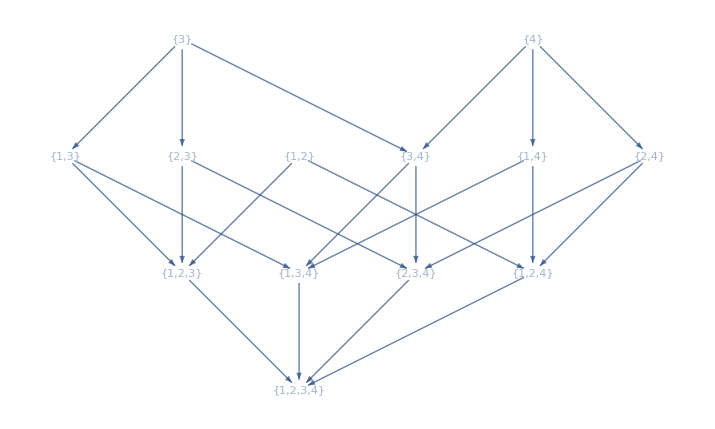

# codimension | 0 | 1 | 2 | 3 | 4
# boundaries | 0 | 2 | 6 | 4 | 1

```mathematica
Bdy=bdyBasis[[1]];
funcTree@Bdy
```

```mathematica
basis=bdyBasis[[2]]//Flatten
```

{⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,7,9⟩,⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨4,5,7,9⟩,⟨1,2,5,6⟩,⟨1,2,5,9⟩,⟨1,2,6,7⟩,⟨1,2,7,9⟩,⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨1,3,7,9⟩,⟨1,4,5,6⟩,⟨1,4,5,9⟩,⟨1,4,6,7⟩,⟨1,4,6,8⟩,⟨1,4,6,9⟩,⟨1,4,7,9⟩,⟨2,3,5,6⟩,⟨2,3,5,7⟩,⟨2,3,5,8⟩,⟨2,3,5,9⟩,⟨2,3,6,7⟩,⟨2,3,7,9⟩,⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨2,4,7,9⟩,⟨3,4,5,7⟩,⟨3,4,5,8⟩,⟨3,4,5,9⟩,⟨1,2,3,5⟩,⟨1,2,3,7⟩,⟨1,2,4,6⟩,⟨1,2,4,9⟩,⟨1,3,4,5⟩,⟨1,3,4,6⟩,⟨1,3,4,7⟩,⟨1,3,4,8⟩,⟨1,3,4,9⟩,⟨2,3,4,5⟩,⟨2,3,4,6⟩,⟨2,3,4,7⟩,⟨2,3,4,8⟩,⟨2,3,4,9⟩,⟨1,2,3,4⟩}

```mathematica
basis//Length
```

50

```mathematica
EchoTiming[A = AMatrix[]];
A[[1]] // MatrixForm
```

10.5135

(e/(X1+X2)+(4 e)/(X1+X2+2 Y) | e/(X1+X2) | (3 e)/(X1+X2)-(3 e)/(X1+X2+2 Y) | -e/(X1+X2)+e/(X1+X2+2 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e/(X1+X2) | e/(X1+X2)-(4 e)/(-X1-X2+2 Y) | -e/(X1+X2)-e/(-X1-X2+2 Y) | (3 e)/(X1+X2)+(3 e)/(-X1-X2+2 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e/(X1+X2) | e/(X1+X2) | (3 e)/(X1+X2) | -e/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e/(X1+X2) | e/(X1+X2) | -e/(X1+X2) | (3 e)/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e/(X1+X2)+e/(-X1-X2+2 Y) | e/(X1+X2)+e/(-X1-X2+2 Y) | e/(X1+X2)-(4 e)/(-X1-X2+2 Y) | e/(X1+X2) | (4 e)/(X1+X2)+(4 e)/(-X1-X2+2 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(3 e)/(X1+X2)+(3 e)/(X1+X2+2 Y) | -(3 e)/(X1+X2)+(3 e)/(X1+X2+2 Y) | e/(X1+X2) | e/(X1+X2)+(4 e)/(X1+X2+2 Y) | -(4 e)/(X1+X2)+(4 e)/(X1+X2+2 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e/(X1+X2) | e/(X1+X2) | e/(X1+X2) | e/(X1+X2) | (4 e)/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 e)/(-X1+Y)+e/(X1+Y) | 0 | e/(-X1+Y)+e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 e)/(-X1+Y)+e/(X1+Y) | 0 | -e/(-X1+Y)-e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | 0 | e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(X1+Y) | 0 | e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e/(X1+Y) | -e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y)+(2 e)/(X1+Y) | e/(-X1+Y)+e/(X1+Y) | e/(-X1+Y)+e/(X1+Y) | -e/(-X1+Y)-e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | e/(-X1+Y) | -e/(X1+Y) | -e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 e)/(-X1+Y)+e/(X1+Y) | -e/(-X1+Y)-e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(X1+Y) | e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y) | -e/(-X1+Y) | 0 | -e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(2 e)/(-2 X1-X2+Y)-(2 e)/(2 X1+X2+Y) | -(2 e)/(-2 X1-X2+Y)-(2 e)/(2 X1+X2+Y) | e/(X1+Y)+(2 e)/(-2 X1-X2+Y) | -e/(-X1+Y)-(2 e)/(2 X1+X2+Y) | -(4 e)/(-2 X1-X2+Y)-(4 e)/(2 X1+X2+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y)+e/(X1+Y)-(6 e)/(-2 X1-X2+Y)+(2 e)/(2 X1+X2+Y) | -(4 e)/(-2 X1-X2+Y)-(4 e)/(2 X1+X2+Y) | e/(X1+Y)+(2 e)/(-2 X1-X2+Y) | -e/(-X1+Y)-(2 e)/(2 X1+X2+Y) | -(2 e)/(-2 X1-X2+Y)-(2 e)/(2 X1+X2+Y) | (2 e)/(-2 X1-X2+Y)+(2 e)/(2 X1+X2+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e/(-X1+Y)+(2 e)/(2 X1+X2+Y) | e/(-X1+Y)+(2 e)/(2 X1+X2+Y) | 0 | e/(-X1+Y)+(2 e)/(2 X1+X2+Y) | e/(-X1+Y)-e/(X1+Y)+(4 e)/(2 X1+X2+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 e)/(2 X1+X2+Y) | -e/(-X1+Y)+e/(X1+Y)+(4 e)/(2 X1+X2+Y) | 0 | e/(-X1+Y)+(2 e)/(2 X1+X2+Y) | -e/(X1+Y)+(2 e)/(2 X1+X2+Y) | -e/(-X1+Y)-(2 e)/(2 X1+X2+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | 0 | e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y) | 0 | 0 | -e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(X1+Y) | 0 | 0 | e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e/(-X1+Y) | e/(-X1+Y) | 0 | 0 | e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y) | -e/(-X1+Y) | 0 | 0 | 0 | -e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e/(X1+2 X2+Y) | -e/(-X1-2 X2+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1-2 X2+Y)+(2 e)/(X1+2 X2+Y) | -e/(X1+2 X2+Y) | (2 e)/(-X1-2 X2+Y)+e/(X1+2 X2+Y) | e/(-X1-2 X2+Y)+e/(X1+2 X2+Y) | e/(-X1-2 X2+Y)+e/(X1+2 X2+Y) | -e/(-X1-2 X2+Y)-e/(X1+2 X2+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-e/(X1+2 X2+Y)+e/(X1+3 Y) | 0 | -e/(-X1+Y)-e/(X1+3 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 e)/(X1+2 X2+Y)+(2 e)/(X1+3 Y) | -e/(-X1+Y)+e/(X1+2 X2+Y)+(3 e)/(X1+3 Y) | -e/(X1+2 X2+Y)+(2 e)/(X1+3 Y) | e/(-X1+Y)-e/(X1+2 X2+Y)+(2 e)/(X1+3 Y) | -e/(-X1+Y)-e/(X1+2 X2+Y) | e/(X1+2 X2+Y)-e/(X1+3 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | e/(-X1-2 X2+Y)-e/(-X1+3 Y) | 0 | e/(X1+Y)+e/(-X1+3 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y)+e/(-X1-2 X2+Y) | e/(X1+Y) | (2 e)/(X1+Y)-(2 e)/(-X1-2 X2+Y)-e/(-X1+3 Y) | e/(X1+Y)-e/(-X1-2 X2+Y)+(2 e)/(-X1+3 Y) | -e/(-X1-2 X2+Y)+e/(-X1+3 Y) | e/(X1+Y)+e/(-X1-2 X2+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | e/(-X1+3 Y) | e/(-X1+Y) | -e/(-X1+3 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(-X1+Y) | e/(-X1+3 Y) | -e/(-X1+Y)-(2 e)/(-X1+3 Y) | e/(-X1+Y)-e/(-X1+3 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y) | 0 | e/(-X1+Y) | -e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | e/(X1+Y) | (2 e)/(X1+Y) | e/(X1+Y) | 0 | e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -e/(-X1+Y) | e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 e)/(-X1+Y)+e/(X1+Y) | -e/(-X1+Y)-e/(X1+Y) | -e/(-X1+Y)-e/(X1+Y) | e/(-X1+Y)+e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -e/(X1+Y) | -e/(X1+Y) | 0 | -e/(X1+Y) | e/(-X1+Y)-e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y)+(2 e)/(X1+Y) | e/(-X1+Y)+e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(-X1+Y) | -e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -e/(X1+Y) | -e/(X1+Y) | 0 | 0 | -e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | e/(X1+Y) | 0 | e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e/(X1+X2) | 0 | 0 | 0 | -e/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 e)/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | e/(X1+X2) | 0 | 0 | 0 | -e/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 e)/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | -e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 e)/(-X1+Y)+e/(X1+Y) | -e/(-X1+Y)-e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(X1+Y) | e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/X1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/X1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/X1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/X1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/X1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/X1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/X1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/X1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -e/(-X1+Y)-e/(X1+Y) | 0 | 0 | 0 | -e/(-X1+Y)-e/(X1+Y) | 0 | 0 | 0 | 0 | e/(X1+X2)+e/(-X1+Y) | e/(-X1+Y)+e/(X1+Y) | -e/(X1+X2)+e/(X1+Y) | -e/(X1+X2)-e/(-X1+Y) | -e/(X1+X2)-e/(-X1+Y) | -e/(-X1+Y)-e/(X1+Y) | 0 | 0 | -e/(X1+X2)+e/(X1+Y) | -e/(X1+X2)-e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 e)/(X1+X2)-(2 e)/(-X1+Y)+(2 e)/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | -e/(X1+Y) | e/(X1+Y) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(-X1+Y) | 0 | 0 | 0 | 0 | e/(-X1+Y) | 0 | -e/(-X1+Y) | 0 | 0 | 0 | 0
0 | 0 | e/(-X1+Y)+e/(X1+Y) | 0 | 0 | 0 | e/(-X1+Y)+e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+X2)-e/(X1+Y) | -e/(-X1+Y)-e/(X1+Y) | 0 | -e/(-X1+Y)-e/(X1+Y) | -e/(X1+X2)-e/(-X1+Y) | -e/(X1+X2)+e/(X1+Y) | -e/(X1+X2)+e/(X1+Y) | e/(-X1+Y)+e/(X1+Y) | -e/(X1+X2)-e/(-X1+Y) | -e/(X1+X2)+e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 e)/(X1+X2)-(2 e)/(-X1+Y)+(2 e)/(X1+Y) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(-X1+Y) | -e/(-X1+Y) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(X1+Y) | 0 | e/(X1+Y) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/X1 | 0 | 0 | 0 | -e/X1 | 0 | 0 | e/X1 | 0 | 0 | e/X1)

```mathematica
EchoTiming[A0 = AMatrix[0]];
A0[[1]] // MatrixPlot
```

12.5439

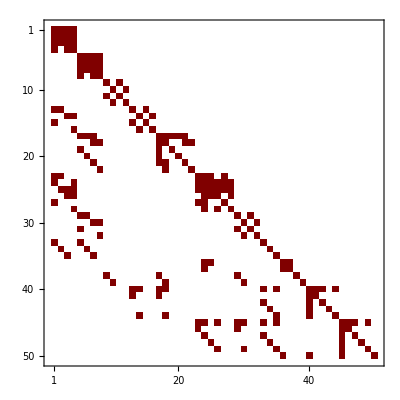

### Basis reduction: filtering

#### start

The stored A-matrix from previous overcomplete set of basis functions:

ClearAll[basis, A0, A];
Get[FileNameJoin[{NotebookDirectory[], "storage", "basis_single-massive-exchange"}]];
Get[FileNameJoin[{NotebookDirectory[], "storage", "A_single-massive-exchange"}]];
Get[FileNameJoin[{NotebookDirectory[], "storage", "A0_single-massive-exchange"}]];

basis // Length
A0[[1]] // Length
A[[1]] // Length

50

50

44

```mathematica
Amatrix=ATotal[A0,twists];
%//MatrixForm
```

(e (Log[X1+X2]-3 Log[Y]+4 Log[X1+X2+2 Y]) | e (-Log[Y]+Log[X1+X2+2 Y]) | e (-Log[X1+X2]+Log[X1+X2+2 Y]) | e (2 Log[X1+X2]-2 Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+X2]-Log[Y]) | e (4 Log[X1+X2]+Log[X1+X2-2 Y]-3 Log[Y]) | e (3 Log[X1+X2]-3 Log[X1+X2-2 Y]) | e (2 Log[X1+X2]-2 Log[X1+X2-2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X1+X2]+Log[Y]) | e (-Log[X1+X2-2 Y]+Log[Y]) | e (Log[X1+X2]+3 Log[X1+X2-2 Y]-2 Log[Y]) | e (-2 Log[X1+X2]+2 Log[X1+X2-2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+X2]-Log[Y]) | 0 | e (-Log[X1+X2]+Log[Y]) | 2 e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X1+X2]+4 Log[X1+X2-2 Y]-3 Log[Y]) | e (Log[X1+X2-2 Y]-Log[Y]) | e (-Log[X1+X2]+Log[X1+X2-2 Y]) | e (2 Log[X1+X2]-2 Log[X1+X2-2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[Y]) | e (4 Log[X1+X2]-3 Log[Y]+Log[X1+X2+2 Y]) | e (3 Log[X1+X2]-3 Log[X1+X2+2 Y]) | e (2 Log[X1+X2]-2 Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[Y]) | e (Log[Y]-Log[X1+X2+2 Y]) | e (Log[X1+X2]-2 Log[Y]+3 Log[X1+X2+2 Y]) | e (-2 Log[X1+X2]+2 Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[Y]) | 0 | e (-Log[X1+X2]+Log[Y]) | 2 e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (2 Log[X1-Y]+2 Log[X2-Y]-4 Log[Y]+Log[X1+Y]+Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X2+Y]) | e (2 Log[X1-Y]-2 Log[Y]+Log[X1+Y]+Log[X2+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | 0 | e (2 Log[X2-Y]-2 Log[Y]+Log[X1+Y]+Log[X2+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y]) | e (-Log[Y]+Log[X2+Y]) | e (Log[X1+Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+Y]-Log[X2+Y]) | e (Log[X1-Y]-Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (2 Log[X1-Y]+Log[X2-Y]-4 Log[Y]+Log[X1+Y]+2 Log[X2+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (Log[X1-Y]-Log[X2-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-Y]+Log[Y]) | e (2 Log[X1-Y]+Log[X2-Y]-2 Log[Y]+Log[X1+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+Y]-Log[X2+Y]) | 0 | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | 0 | e (Log[X2-Y]-2 Log[Y]+Log[X1+Y]+2 Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e (-Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y]) | e (Log[X2-Y]-Log[Y]) | e (Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[2 X1+X2-Y]+Log[X1+Y]) | e (Log[X1-Y]-Log[2 X1+X2-Y]) | e (Log[-2 X1-X2-Y]-Log[2 X1+X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]+Log[-2 X1-X2-Y]+3 Log[2 X1+X2-Y]-4 Log[Y]+Log[X1+Y]) | e (-Log[-2 X1-X2-Y]+Log[2 X1+X2-Y]) | e (-Log[2 X1+X2-Y]+Log[X1+Y]) | e (Log[X1-Y]-Log[2 X1+X2-Y]) | e (Log[-2 X1-X2-Y]-Log[2 X1+X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[-2 X1-X2-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-2 X1-X2-Y]+Log[Y]) | e (2 Log[X1-Y]+Log[-2 X1-X2-Y]-2 Log[Y]+Log[X1+Y]) | 0 | 0 | e (Log[X1-Y]-Log[-2 X1-X2-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[X2-3 Y]+Log[X1+Y]) | 0 | 0 | e (Log[X2-3 Y]-Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-3 Y]+Log[X1+Y]) | 0 | e (3 Log[X2-3 Y]+Log[X2-Y]-3 Log[Y]+Log[X1+Y]) | e (Log[X2-3 Y]-Log[Y]) | e (Log[X2-3 Y]-Log[X2-Y]) | e (-Log[X2-3 Y]+Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2+Y]) | e (-Log[X2+Y]+Log[X2+3 Y]) | e (-Log[X2+Y]+Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2+Y]) | e (Log[X2+Y]-Log[X2+3 Y]) | e (-Log[Y]+Log[X2+Y]) | e (Log[X1-Y]-3 Log[Y]+3 Log[X2+Y]+Log[X2+3 Y]) | e (2 Log[X2+Y]-2 Log[X2+3 Y]) | e (Log[X2+Y]-Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (Log[-2 X1-X2-Y]-Log[X2+3 Y]) | e (Log[X2-Y]-Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[-2 X1-X2-Y]-Log[Y]) | e (-Log[-2 X1-X2-Y]+Log[X2+3 Y]) | e (-Log[X2-Y]+Log[Y]) | e (Log[Y]-Log[X2+3 Y]) | e (Log[-2 X1-X2-Y]+Log[X2-Y]-2 Log[Y]+2 Log[X2+3 Y]) | e (-Log[X2-Y]+Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y]) | e (Log[X2-Y]-Log[Y]) | 0 | e (-Log[X2-Y]+Log[Y]) | e (Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X2-Y]+Log[X1+2 X2+Y]) | e (-Log[X2-Y]+Log[X1+2 X2-Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (2 Log[X2-Y]+2 Log[X1+2 X2-Y]-4 Log[Y]+Log[X2+Y]+Log[X1+2 X2+Y]) | e (Log[X2-Y]-Log[X1+2 X2+Y]) | e (Log[X2-Y]-Log[X1+2 X2-Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (-Log[X1+2 X2-Y]+Log[X1+2 X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X1+2 X2+Y]+Log[X1+3 Y]) | 0 | 0 | e (Log[X1-Y]-Log[X1+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+2 X2+Y]+Log[X1+3 Y]) | e (Log[X1-Y]-3 Log[Y]+Log[X1+2 X2+Y]+3 Log[X1+3 Y]) | e (-Log[Y]+Log[X1+3 Y]) | e (-Log[X1-Y]+Log[X1+3 Y]) | e (-Log[X1+2 X2+Y]+Log[X1+3 Y]) | e (Log[X1-Y]-Log[X1+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | e (-Log[X1+2 X2-Y]+Log[X1+Y]) | e (-Log[X1-3 Y]+Log[X1+Y]) | e (-Log[X1-3 Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-2 Log[X1+2 X2-Y]+2 Log[X1+Y]) | e (-Log[Y]+Log[X1+Y]) | e (Log[X1-3 Y]+Log[X1+2 X2-Y]-3 Log[Y]+3 Log[X1+Y]) | e (-2 Log[X1-3 Y]+2 Log[X1+Y]) | e (Log[X1+2 X2-Y]-Log[X1+Y]) | e (-Log[X1-3 Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (Log[X1-3 Y]-Log[X2+Y]) | e (Log[X1-3 Y]-Log[X1-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X2+Y]) | e (-Log[X1-Y]+Log[Y]) | e (-Log[X1-3 Y]+Log[Y]) | e (2 Log[X1-3 Y]+Log[X1-Y]-2 Log[Y]+Log[X2+Y]) | 0 | e (Log[X1-3 Y]-Log[X1-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X2-Y]+Log[X1+2 X2+Y]) | 0 | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+2 X2+Y]) | e (Log[X2-Y]-Log[X1+2 X2+Y]) | 0 | 0 | e (2 Log[X2-Y]-2 Log[Y]+Log[X2+Y]+Log[X1+2 X2+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e (Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y]) | 0 | e (-Log[X1-Y]+Log[Y]) | e (-Log[Y]+Log[X2+Y]) | e (Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2-Y]) | e (-Log[X2-Y]+Log[X1+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]+2 Log[X2-Y]-4 Log[Y]+2 Log[X1+Y]+Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+Y]-Log[X2+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X2+Y]) | e (Log[X1-Y]-2 Log[Y]+2 Log[X1+Y]+Log[X2+Y]) | 0 | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2-Y]) | 0 | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y]) | 0 | e (Log[X1-Y]+2 Log[X2-Y]-2 Log[Y]+Log[X2+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y]) | e (-Log[Y]+Log[X2+Y]) | e (Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+X2]-Log[Y]) | 0 | 0 | e Log[Y] | e (-Log[X1+X2]+Log[Y]) | 0 | 0 | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (2 Log[X1+X2]-Log[Y]) | 0 | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | e Log[X1+X2] | e Log[Y] | e Log[Y] | 0 | -e Log[X1+X2] | -e Log[Y] | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[Y] | e (2 Log[X1+X2]-2 Log[Y]) | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (Log[X1+X2]-Log[Y]) | -e Log[Y] | 0 | 0 | e (-Log[X1+X2]+Log[Y]) | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[Y] | 0 | e (2 Log[X1+X2]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2]-Log[Y]) | 0 | 0 | 0 | e (-Log[X2]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2]-Log[Y]) | e (-Log[Y]+Log[X1+Y]) | e (Log[X1-Y]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2]+2 Log[X1-Y]-2 Log[Y]+Log[X1+Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2]+Log[Y]) | 0 | 0 | 0 | e (Log[X2]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y]) | 0 | 0 | e (-Log[X2]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y]) | e (Log[X2]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[X2-Y]) | 0 | e (Log[X2-Y]-Log[Y]) | e (Log[X2-Y]-Log[Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]+2 Log[X2-Y]-2 Log[Y]+Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[Y]) | 0 | 0 | e (-Log[Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X2+Y]) | e (Log[X1]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X1-Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | e (-Log[X1+X2]+Log[X1-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X1+Y]) | 0 | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | e (Log[X1+X2]+3 Log[X1-Y]-4 Log[Y]+2 Log[X1+Y]) | e (-Log[X1+X2]+Log[X1-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | e (Log[X1+X2]-Log[X2+Y]) | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X2+Y]) | e (Log[X1+X2]+2 Log[X2-Y]-4 Log[Y]+3 Log[X2+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-Y]+Log[Y]) | -e Log[Y] | 0 | 0 | e (Log[X2-Y]-Log[Y]) | 0 | 0 | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y]) | e (-Log[X2-Y]+Log[Y]) | e (Log[X2-Y]-Log[Y]+Log[X1+Y]) | 0 | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X2+Y] | -e Log[Y] | e Log[X2+Y] | -e Log[Y] | 0 | e Log[Y] | 0 | e Log[X2+Y] | e Log[Y] | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | -e Log[X1-Y] | -e Log[X2+Y] | -e Log[Y] | e (Log[X1-Y]-2 Log[Y]+Log[X2+Y]) | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y]) | 0 | e Log[Y] | 0 | e (-Log[Y]+Log[X1+Y]) | 0 | 0 | e (Log[X2-Y]-Log[Y]) | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y]) | e (-Log[X2-Y]+Log[Y]) | e Log[Y] | 0 | e (Log[X2-Y]-Log[Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X1+Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | e (-Log[X1+X2]+Log[X1+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]+2 Log[X1-Y]-4 Log[Y]+3 Log[X1+Y]) | e (-Log[X1+X2]+Log[X1+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | e (-Log[X1-Y]+Log[X1+Y]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X2-Y]) | 0 | 0 | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | e (Log[X1+X2]-Log[X2-Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X2-Y]) | e (Log[X1+X2]+3 Log[X2-Y]-4 Log[Y]+2 Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y]) | 0 | 0 | e (Log[Y]-Log[X2+Y]) | -e Log[Y] | 0 | 0 | e (-Log[Y]+Log[X2+Y]) | e Log[Y] | e (-Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y]) | e (Log[Y]-Log[X2+Y]) | e (Log[X1-Y]-Log[Y]+Log[X2+Y]) | 0 | e Log[Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X2-Y] | 0 | -e Log[X1+Y] | -e Log[Y] | e Log[X2-Y] | -e Log[Y] | e Log[X2-Y] | e Log[Y] | -e Log[X2-Y] | e Log[Y] | 0 | e (Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X1+Y] | -e Log[X2-Y] | -e Log[Y] | e (Log[X2-Y]-2 Log[Y]+Log[X1+Y]) | -e Log[Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y]) | 0 | e Log[Y] | 0 | e (Log[X1-Y]-Log[Y]) | 0 | -e Log[Y] | 0 | 0 | e (-Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y]) | e (Log[Y]-Log[X2+Y]) | e Log[Y] | 0 | e (Log[X1-Y]-Log[Y]+Log[X2+Y]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[Y]) | 0 | e (Log[X2]-Log[Y]) | 0 | e (-Log[X1]+Log[Y]) | e (-Log[X2]+Log[Y]) | 0 | 0 | 0 | e (Log[X1]-Log[Y]) | e (Log[X2]-Log[Y]) | 0 | 0 | 0 | e (Log[X1]+Log[X2]))

```mathematica
Amatrix//Letter
%//Length
```

{X1,X2,X1+X2,X1-3 Y,X2-3 Y,X1+X2-2 Y,X1-Y,-2 X1-X2-Y,X2-Y,2 X1+X2-Y,X1+2 X2-Y,Y,X1+Y,X2+Y,X1+2 X2+Y,X1+X2+2 Y,X1+3 Y,X2+3 Y}

18

```mathematica
Coefficient[Amatrix,e]//MatrixForm
```

(Log[X1+X2]-3 Log[Y]+4 Log[X1+X2+2 Y] | -Log[Y]+Log[X1+X2+2 Y] | -Log[X1+X2]+Log[X1+X2+2 Y] | 2 Log[X1+X2]-2 Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[X1+X2]-Log[Y] | 4 Log[X1+X2]+Log[X1+X2-2 Y]-3 Log[Y] | 3 Log[X1+X2]-3 Log[X1+X2-2 Y] | 2 Log[X1+X2]-2 Log[X1+X2-2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+X2]+Log[Y] | -Log[X1+X2-2 Y]+Log[Y] | Log[X1+X2]+3 Log[X1+X2-2 Y]-2 Log[Y] | -2 Log[X1+X2]+2 Log[X1+X2-2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[X1+X2]-Log[Y] | 0 | -Log[X1+X2]+Log[Y] | 2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X1+X2]+4 Log[X1+X2-2 Y]-3 Log[Y] | Log[X1+X2-2 Y]-Log[Y] | -Log[X1+X2]+Log[X1+X2-2 Y] | 2 Log[X1+X2]-2 Log[X1+X2-2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X1+X2]-Log[Y] | 4 Log[X1+X2]-3 Log[Y]+Log[X1+X2+2 Y] | 3 Log[X1+X2]-3 Log[X1+X2+2 Y] | 2 Log[X1+X2]-2 Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[X1+X2]+Log[Y] | Log[Y]-Log[X1+X2+2 Y] | Log[X1+X2]-2 Log[Y]+3 Log[X1+X2+2 Y] | -2 Log[X1+X2]+2 Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X1+X2]-Log[Y] | 0 | -Log[X1+X2]+Log[Y] | 2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 Log[X1-Y]+2 Log[X2-Y]-4 Log[Y]+Log[X1+Y]+Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X2+Y] | 2 Log[X1-Y]-2 Log[Y]+Log[X1+Y]+Log[X2+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | 0 | 2 Log[X2-Y]-2 Log[Y]+Log[X1+Y]+Log[X2+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X1+Y] | -Log[Y]+Log[X2+Y] | Log[X1+Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[X1+Y]-Log[X2+Y] | Log[X1-Y]-Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 Log[X1-Y]+Log[X2-Y]-4 Log[Y]+Log[X1+Y]+2 Log[X2+Y] | -Log[X2-Y]+Log[X2+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Log[X1-Y]-Log[X2-Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2-Y]+Log[Y] | 2 Log[X1-Y]+Log[X2-Y]-2 Log[Y]+Log[X1+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[X1+Y]-Log[X2+Y] | 0 | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | 0 | Log[X2-Y]-2 Log[Y]+Log[X1+Y]+2 Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -Log[X2-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X1+Y] | Log[X2-Y]-Log[Y] | Log[X2-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[2 X1+X2-Y]+Log[X1+Y] | Log[X1-Y]-Log[2 X1+X2-Y] | Log[-2 X1-X2-Y]-Log[2 X1+X2-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]+Log[-2 X1-X2-Y]+3 Log[2 X1+X2-Y]-4 Log[Y]+Log[X1+Y] | -Log[-2 X1-X2-Y]+Log[2 X1+X2-Y] | -Log[2 X1+X2-Y]+Log[X1+Y] | Log[X1-Y]-Log[2 X1+X2-Y] | Log[-2 X1-X2-Y]-Log[2 X1+X2-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[-2 X1-X2-Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-2 X1-X2-Y]+Log[Y] | 2 Log[X1-Y]+Log[-2 X1-X2-Y]-2 Log[Y]+Log[X1+Y] | 0 | 0 | Log[X1-Y]-Log[-2 X1-X2-Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[X2-3 Y]+Log[X1+Y] | 0 | 0 | Log[X2-3 Y]-Log[X2-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2-3 Y]+Log[X1+Y] | 0 | 3 Log[X2-3 Y]+Log[X2-Y]-3 Log[Y]+Log[X1+Y] | Log[X2-3 Y]-Log[Y] | Log[X2-3 Y]-Log[X2-Y] | -Log[X2-3 Y]+Log[X2-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[X2+Y] | -Log[X2+Y]+Log[X2+3 Y] | -Log[X2+Y]+Log[X2+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[X2+Y] | Log[X2+Y]-Log[X2+3 Y] | -Log[Y]+Log[X2+Y] | Log[X1-Y]-3 Log[Y]+3 Log[X2+Y]+Log[X2+3 Y] | 2 Log[X2+Y]-2 Log[X2+3 Y] | Log[X2+Y]-Log[X2+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | Log[-2 X1-X2-Y]-Log[X2+3 Y] | Log[X2-Y]-Log[X2+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-2 X1-X2-Y]-Log[Y] | -Log[-2 X1-X2-Y]+Log[X2+3 Y] | -Log[X2-Y]+Log[Y] | Log[Y]-Log[X2+3 Y] | Log[-2 X1-X2-Y]+Log[X2-Y]-2 Log[Y]+2 Log[X2+3 Y] | -Log[X2-Y]+Log[X2+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X1+Y] | Log[X2-Y]-Log[Y] | 0 | -Log[X2-Y]+Log[Y] | Log[X2-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X2-Y]+Log[X1+2 X2+Y] | -Log[X2-Y]+Log[X1+2 X2-Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 Log[X2-Y]+2 Log[X1+2 X2-Y]-4 Log[Y]+Log[X2+Y]+Log[X1+2 X2+Y] | Log[X2-Y]-Log[X1+2 X2+Y] | Log[X2-Y]-Log[X1+2 X2-Y] | Log[X2-Y]-Log[X2+Y] | -Log[X1+2 X2-Y]+Log[X1+2 X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+2 X2+Y]+Log[X1+3 Y] | 0 | 0 | Log[X1-Y]-Log[X1+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1+2 X2+Y]+Log[X1+3 Y] | Log[X1-Y]-3 Log[Y]+Log[X1+2 X2+Y]+3 Log[X1+3 Y] | -Log[Y]+Log[X1+3 Y] | -Log[X1-Y]+Log[X1+3 Y] | -Log[X1+2 X2+Y]+Log[X1+3 Y] | Log[X1-Y]-Log[X1+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -Log[X1+2 X2-Y]+Log[X1+Y] | -Log[X1-3 Y]+Log[X1+Y] | -Log[X1-3 Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 Log[X1+2 X2-Y]+2 Log[X1+Y] | -Log[Y]+Log[X1+Y] | Log[X1-3 Y]+Log[X1+2 X2-Y]-3 Log[Y]+3 Log[X1+Y] | -2 Log[X1-3 Y]+2 Log[X1+Y] | Log[X1+2 X2-Y]-Log[X1+Y] | -Log[X1-3 Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Log[X1-3 Y]-Log[X2+Y] | Log[X1-3 Y]-Log[X1-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X2+Y] | -Log[X1-Y]+Log[Y] | -Log[X1-3 Y]+Log[Y] | 2 Log[X1-3 Y]+Log[X1-Y]-2 Log[Y]+Log[X2+Y] | 0 | Log[X1-3 Y]-Log[X1-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X2-Y]+Log[X1+2 X2+Y] | 0 | 0 | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+2 X2+Y] | Log[X2-Y]-Log[X1+2 X2+Y] | 0 | 0 | 2 Log[X2-Y]-2 Log[Y]+Log[X2+Y]+Log[X1+2 X2+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | Log[X1-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[Y] | 0 | -Log[X1-Y]+Log[Y] | -Log[Y]+Log[X2+Y] | Log[X1-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X1-Y]-Log[X2-Y] | -Log[X2-Y]+Log[X1+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]+2 Log[X2-Y]-4 Log[Y]+2 Log[X1+Y]+Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | Log[X1+Y]-Log[X2+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X2+Y] | Log[X1-Y]-2 Log[Y]+2 Log[X1+Y]+Log[X2+Y] | 0 | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X1-Y]-Log[X2-Y] | 0 | 0 | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[Y] | 0 | Log[X1-Y]+2 Log[X2-Y]-2 Log[Y]+Log[X2+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[Y] | -Log[Y]+Log[X2+Y] | Log[X1-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[X1+X2]-Log[Y] | 0 | 0 | Log[Y] | -Log[X1+X2]+Log[Y] | 0 | 0 | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 Log[X1+X2]-Log[Y] | 0 | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Log[X1+X2] | Log[Y] | Log[Y] | 0 | -Log[X1+X2] | -Log[Y] | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y] | 2 Log[X1+X2]-2 Log[Y] | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Log[X1+X2]-Log[Y] | -Log[Y] | 0 | 0 | -Log[X1+X2]+Log[Y] | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y] | 0 | 2 Log[X1+X2]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2]-Log[Y] | 0 | 0 | 0 | -Log[X2]+Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2]-Log[Y] | -Log[Y]+Log[X1+Y] | Log[X1-Y]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2]+2 Log[X1-Y]-2 Log[Y]+Log[X1+Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2]+Log[Y] | 0 | 0 | 0 | Log[X2]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X1+Y] | 0 | 0 | -Log[X2]+Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X1+Y] | Log[X2]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1]+Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1]-Log[X2-Y] | 0 | Log[X2-Y]-Log[Y] | Log[X2-Y]-Log[Y] | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1]+Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1]+2 Log[X2-Y]-2 Log[Y]+Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1]+Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1]-Log[Y] | 0 | 0 | -Log[Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1]+Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X2+Y] | Log[X1]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1+X2]-Log[X1-Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | -Log[X1+X2]+Log[X1-Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[X1+Y] | 0 | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | Log[X1+X2]+3 Log[X1-Y]-4 Log[Y]+2 Log[X1+Y] | -Log[X1+X2]+Log[X1-Y] | Log[X1-Y]-Log[X1+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1+X2]+Log[X2+Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0 | Log[X1+X2]-Log[X2+Y] | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | -Log[X1+X2]+Log[X2+Y] | Log[X1+X2]+2 Log[X2-Y]-4 Log[Y]+3 Log[X2+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2-Y]+Log[Y] | -Log[Y] | 0 | 0 | Log[X2-Y]-Log[Y] | 0 | 0 | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X1+Y] | -Log[X2-Y]+Log[Y] | Log[X2-Y]-Log[Y]+Log[X1+Y] | 0 | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2+Y] | -Log[Y] | Log[X2+Y] | -Log[Y] | 0 | Log[Y] | 0 | Log[X2+Y] | Log[Y] | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y] | -Log[X2+Y] | -Log[Y] | Log[X1-Y]-2 Log[Y]+Log[X2+Y] | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X1+Y] | 0 | Log[Y] | 0 | -Log[Y]+Log[X1+Y] | 0 | 0 | Log[X2-Y]-Log[Y] | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | Log[Y]-Log[X1+Y] | -Log[X2-Y]+Log[Y] | Log[Y] | 0 | Log[X2-Y]-Log[Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1+X2]-Log[X1+Y] | Log[X1-Y]-Log[X1+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | -Log[X1+X2]+Log[X1+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | Log[X1-Y]-Log[X1+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1+X2]+2 Log[X1-Y]-4 Log[Y]+3 Log[X1+Y] | -Log[X1+X2]+Log[X1+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | -Log[X1-Y]+Log[X1+Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1+X2]+Log[X2-Y] | 0 | 0 | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | Log[X1+X2]-Log[X2-Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1+X2]+Log[X2-Y] | Log[X1+X2]+3 Log[X2-Y]-4 Log[Y]+2 Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[Y] | 0 | 0 | Log[Y]-Log[X2+Y] | -Log[Y] | 0 | 0 | -Log[Y]+Log[X2+Y] | Log[Y] | -Log[X1-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[Y] | Log[Y]-Log[X2+Y] | Log[X1-Y]-Log[Y]+Log[X2+Y] | 0 | Log[Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2-Y] | 0 | -Log[X1+Y] | -Log[Y] | Log[X2-Y] | -Log[Y] | Log[X2-Y] | Log[Y] | -Log[X2-Y] | Log[Y] | 0 | Log[X2-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1+Y] | -Log[X2-Y] | -Log[Y] | Log[X2-Y]-2 Log[Y]+Log[X1+Y] | -Log[Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[Y] | 0 | Log[Y] | 0 | Log[X1-Y]-Log[Y] | 0 | -Log[Y] | 0 | 0 | -Log[X1-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[Y] | Log[Y]-Log[X2+Y] | Log[Y] | 0 | Log[X1-Y]-Log[Y]+Log[X2+Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1]+Log[Y] | 0 | Log[X2]-Log[Y] | 0 | -Log[X1]+Log[Y] | -Log[X2]+Log[Y] | 0 | 0 | 0 | Log[X1]-Log[Y] | Log[X2]-Log[Y] | 0 | 0 | 0 | Log[X1]+Log[X2])

```mathematica
need=Position[basis,#]&/@{⟨1,3,5,6⟩,⟨2,4,5,6⟩,⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨3,5,7,9⟩,⟨4,5,7,9⟩,⟨1,3,7,9⟩,⟨2,4,7,9⟩}//Flatten
```

{13,29,1,2,3,5,6,7,14,15,30,31,4,8,16,32}

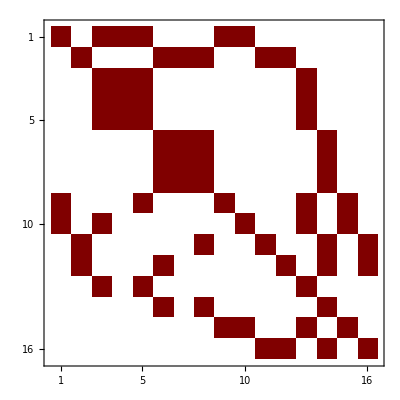

```mathematica
AmatrixNeed=Amatrix[[need,need]];
%//MatrixPlot
```

```mathematica
Coefficient[AmatrixNeed,e]//MatrixForm
%//MatrixPlot
```

(2 Log[X1-Y]+Log[X2-Y]-4 Log[Y]+Log[X1+Y]+2 Log[X2+Y] | 0 | Log[X1+Y]-Log[X2+Y] | Log[X1-Y]-Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | -Log[X2-Y]+Log[X2+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | Log[X1-Y]+2 Log[X2-Y]-4 Log[Y]+2 Log[X1+Y]+Log[X2+Y] | 0 | 0 | 0 | Log[X1-Y]-Log[X2-Y] | -Log[X2-Y]+Log[X1+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | Log[X2-Y]-Log[X2+Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0
0 | 0 | Log[X1+X2]-3 Log[Y]+4 Log[X1+X2+2 Y] | -Log[Y]+Log[X1+X2+2 Y] | -Log[X1+X2]+Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 Log[X1+X2]-2 Log[X1+X2+2 Y] | 0 | 0 | 0
0 | 0 | Log[X1+X2]-Log[Y] | 4 Log[X1+X2]+Log[X1+X2-2 Y]-3 Log[Y] | 3 Log[X1+X2]-3 Log[X1+X2-2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 Log[X1+X2]-2 Log[X1+X2-2 Y] | 0 | 0 | 0
0 | 0 | -Log[X1+X2]+Log[Y] | -Log[X1+X2-2 Y]+Log[Y] | Log[X1+X2]+3 Log[X1+X2-2 Y]-2 Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 Log[X1+X2]+2 Log[X1+X2-2 Y] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | Log[X1+X2]+4 Log[X1+X2-2 Y]-3 Log[Y] | Log[X1+X2-2 Y]-Log[Y] | -Log[X1+X2]+Log[X1+X2-2 Y] | 0 | 0 | 0 | 0 | 0 | 2 Log[X1+X2]-2 Log[X1+X2-2 Y] | 0 | 0
0 | 0 | 0 | 0 | 0 | Log[X1+X2]-Log[Y] | 4 Log[X1+X2]-3 Log[Y]+Log[X1+X2+2 Y] | 3 Log[X1+X2]-3 Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | 2 Log[X1+X2]-2 Log[X1+X2+2 Y] | 0 | 0
0 | 0 | 0 | 0 | 0 | -Log[X1+X2]+Log[Y] | Log[Y]-Log[X1+X2+2 Y] | Log[X1+X2]-2 Log[Y]+3 Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | -2 Log[X1+X2]+2 Log[X1+X2+2 Y] | 0 | 0
-Log[X2-Y]+Log[Y] | 0 | 0 | 0 | Log[X1-Y]-Log[X2-Y] | 0 | 0 | 0 | 2 Log[X1-Y]+Log[X2-Y]-2 Log[Y]+Log[X1+Y] | 0 | 0 | 0 | Log[X1-Y]-Log[X1+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0
-Log[Y]+Log[X1+Y] | 0 | Log[X1+Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2-Y]-2 Log[Y]+Log[X1+Y]+2 Log[X2+Y] | 0 | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0
0 | Log[Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | Log[X1+Y]-Log[X2+Y] | 0 | 0 | Log[X1-Y]-2 Log[Y]+2 Log[X1+Y]+Log[X2+Y] | 0 | 0 | -Log[X1-Y]+Log[X1+Y] | 0 | -Log[X1-Y]+Log[X1+Y]
0 | Log[X1-Y]-Log[Y] | 0 | 0 | 0 | Log[X1-Y]-Log[X2-Y] | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]+2 Log[X2-Y]-2 Log[Y]+Log[X2+Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0 | -Log[X2-Y]+Log[X2+Y]
0 | 0 | Log[X1+X2]-Log[Y] | 0 | -Log[X1+X2]+Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 Log[X1+X2] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | Log[X1+X2]-Log[Y] | 0 | -Log[X1+X2]+Log[Y] | 0 | 0 | 0 | 0 | 0 | 2 Log[X1+X2] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X1+Y] | Log[X2-Y]-Log[Y] | 0 | 0 | -Log[X2-Y]+Log[X1+Y] | 0 | Log[X2-Y]+Log[X1+Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[Y] | -Log[Y]+Log[X2+Y] | 0 | Log[X1-Y]-Log[X2+Y] | 0 | Log[X1-Y]+Log[X2+Y])

-Graphics-

```mathematica
Coefficient[AmatrixNeed,g]//MatrixForm
%//MatrixPlot
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

-Graphics-

```mathematica
basisNeed=basis[[need]]
```

{⟨1,3,5,6⟩,⟨2,4,5,6⟩,⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨3,5,7,9⟩,⟨4,5,7,9⟩,⟨1,3,7,9⟩,⟨2,4,7,9⟩}

```mathematica
Coefficient[Amatrix,e]
```

{{Log[X1+X2]-3 Log[Y]+4 Log[X1+X2+2 Y],-Log[Y]+Log[X1+X2+2 Y],-Log[X1+X2]+Log[X1+X2+2 Y],2 Log[X1+X2]-2 Log[X1+X2+2 Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{Log[X1+X2]-Log[Y],4 Log[X1+X2]+Log[X1+X2-2 Y]-3 Log[Y],3 Log[X1+X2]-3 Log[X1+X2-2 Y],2 Log[X1+X2]-2 Log[X1+X2-2 Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-Log[X1+X2]+Log[Y],-Log[X1+X2-2 Y]+Log[Y],Log[X1+X2]+3 Log[X1+X2-2 Y]-2 Log[Y],-2 Log[X1+X2]+2 Log[X1+X2-2 Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{Log[X1+X2]-Log[Y],0,-Log[X1+X2]+Log[Y],2 Log[X1+X2],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,Log[X1+X2]+4 Log[X1+X2-2 Y]-3 Log[Y],Log[X1+X2-2 Y]-Log[Y],-Log[X1+X2]+Log[X1+X2-2 Y],2 Log[X1+X2]-2 Log[X1+X2-2 Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,Log[X1+X2]-Log[Y],4 Log[X1+X2]-3 Log[Y]+Log[X1+X2+2 Y],3 Log[X1+X2]-3 Log[X1+X2+2 Y],2 Log[X1+X2]-2 Log[X1+X2+2 Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-Log[X1+X2]+Log[Y],Log[Y]-Log[X1+X2+2 Y],Log[X1+X2]-2 Log[Y]+3 Log[X1+X2+2 Y],-2 Log[X1+X2]+2 Log[X1+X2+2 Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,Log[X1+X2]-Log[Y],0,-Log[X1+X2]+Log[Y],2 Log[X1+X2],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2 Log[X1-Y]+2 Log[X2-Y]-4 Log[Y]+Log[X1+Y]+Log[X2+Y],Log[X2-Y]-Log[X2+Y],-Log[X1-Y]+Log[X1+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,Log[Y]-Log[X2+Y],2 Log[X1-Y]-2 Log[Y]+Log[X1+Y]+Log[X2+Y],0,Log[X1-Y]-Log[X1+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-Log[Y]+Log[X1+Y],0,2 Log[X2-Y]-2 Log[Y]+Log[X1+Y]+Log[X2+Y],-Log[X2-Y]+Log[X2+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,Log[Y]-Log[X1+Y],-Log[Y]+Log[X2+Y],Log[X1+Y]+Log[X2+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{Log[X1+Y]-Log[X2+Y],Log[X1-Y]-Log[X2+Y],Log[X2-Y]-Log[X2+Y],0,0,0,0,0,0,0,0,0,2 Log[X1-Y]+Log[X2-Y]-4 Log[Y]+Log[X1+Y]+2 Log[X2+Y],-Log[X2-Y]+Log[X2+Y],-Log[X1-Y]+Log[X1+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,Log[X1-Y]-Log[X2-Y],Log[X1-Y]-Log[X1+Y],0,0,0,0,0,0,0,0,-Log[X2-Y]+Log[Y],2 Log[X1-Y]+Log[X2-Y]-2 Log[Y]+Log[X1+Y],0,Log[X1-Y]-Log[X1+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{Log[X1+Y]-Log[X2+Y],0,0,-Log[X2-Y]+Log[X2+Y],0,0,0,0,0,0,0,0,-Log[Y]+Log[X1+Y],0,Log[X2-Y]-2 Log[Y]+Log[X1+Y]+2 Log[X2+Y],Log[X2-Y]-Log[X2+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-Log[X2-Y]+Log[X1+Y],0,0,0,0,0,0,0,0,0,Log[Y]-Log[X1+Y],Log[X2-Y]-Log[Y],Log[X2-Y]+Log[X1+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-Log[2 X1+X2-Y]+Log[X1+Y],Log[X1-Y]-Log[2 X1+X2-Y],Log[-2 X1-X2-Y]-Log[2 X1+X2-Y],0,0,0,0,0,0,0,0,0,Log[X1-Y]+Log[-2 X1-X2-Y]+3 Log[2 X1+X2-Y]-4 Log[Y]+Log[X1+Y],-Log[-2 X1-X2-Y]+Log[2 X1+X2-Y],-Log[2 X1+X2-Y]+Log[X1+Y],Log[X1-Y]-Log[2 X1+X2-Y],Log[-2 X1-X2-Y]-Log[2 X1+X2-Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,Log[X1-Y]-Log[-2 X1-X2-Y],Log[X1-Y]-Log[X1+Y],0,0,0,0,0,0,0,0,-Log[-2 X1-X2-Y]+Log[Y],2 Log[X1-Y]+Log[-2 X1-X2-Y]-2 Log[Y]+Log[X1+Y],0,0,Log[X1-Y]-Log[-2 X1-X2-Y],Log[X1-Y]-Log[X1+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-Log[X2-3 Y]+Log[X1+Y],0,0,Log[X2-3 Y]-Log[X2-Y],0,0,0,0,0,0,0,0,-Log[X2-3 Y]+Log[X1+Y],0,3 Log[X2-3 Y]+Log[X2-Y]-3 Log[Y]+Log[X1+Y],Log[X2-3 Y]-Log[Y],Log[X2-3 Y]-Log[X2-Y],-Log[X2-3 Y]+Log[X2-Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,Log[X1-Y]-Log[X2+Y],-Log[X2+Y]+Log[X2+3 Y],-Log[X2+Y]+Log[X2+3 Y],0,0,0,0,0,0,0,0,Log[X1-Y]-Log[X2+Y],Log[X2+Y]-Log[X2+3 Y],-Log[Y]+Log[X2+Y],Log[X1-Y]-3 Log[Y]+3 Log[X2+Y]+Log[X2+3 Y],2 Log[X2+Y]-2 Log[X2+3 Y],Log[X2+Y]-Log[X2+3 Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,Log[-2 X1-X2-Y]-Log[X2+3 Y],Log[X2-Y]-Log[X2+3 Y],0,0,0,0,0,0,0,0,Log[-2 X1-X2-Y]-Log[Y],-Log[-2 X1-X2-Y]+Log[X2+3 Y],-Log[X2-Y]+Log[Y],Log[Y]-Log[X2+3 Y],Log[-2 X1-X2-Y]+Log[X2-Y]-2 Log[Y]+2 Log[X2+3 Y],-Log[X2-Y]+Log[X2+3 Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-Log[X2-Y]+Log[X1+Y],0,0,0,0,0,0,0,0,0,Log[Y]-Log[X1+Y],Log[X2-Y]-Log[Y],0,-Log[X2-Y]+Log[Y],Log[X2-Y]+Log[X1+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-Log[X2-Y]+Log[X1+2 X2+Y],-Log[X2-Y]+Log[X1+2 X2-Y],-Log[X2-Y]+Log[X2+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 Log[X2-Y]+2 Log[X1+2 X2-Y]-4 Log[Y]+Log[X2+Y]+Log[X1+2 X2+Y],Log[X2-Y]-Log[X1+2 X2+Y],Log[X2-Y]-Log[X1+2 X2-Y],Log[X2-Y]-Log[X2+Y],-Log[X1+2 X2-Y]+Log[X1+2 X2+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-Log[X1+2 X2+Y]+Log[X1+3 Y],0,0,Log[X1-Y]-Log[X1+3 Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-Log[X1+2 X2+Y]+Log[X1+3 Y],Log[X1-Y]-3 Log[Y]+Log[X1+2 X2+Y]+3 Log[X1+3 Y],-Log[Y]+Log[X1+3 Y],-Log[X1-Y]+Log[X1+3 Y],-Log[X1+2 X2+Y]+Log[X1+3 Y],Log[X1-Y]-Log[X1+3 Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-Log[X1+2 X2-Y]+Log[X1+Y],-Log[X1-3 Y]+Log[X1+Y],-Log[X1-3 Y]+Log[X1+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2 Log[X1+2 X2-Y]+2 Log[X1+Y],-Log[Y]+Log[X1+Y],Log[X1-3 Y]+Log[X1+2 X2-Y]-3 Log[Y]+3 Log[X1+Y],-2 Log[X1-3 Y]+2 Log[X1+Y],Log[X1+2 X2-Y]-Log[X1+Y],-Log[X1-3 Y]+Log[X1+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,Log[X1-3 Y]-Log[X2+Y],Log[X1-3 Y]-Log[X1-Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Log[Y]-Log[X2+Y],-Log[X1-Y]+Log[Y],-Log[X1-3 Y]+Log[Y],2 Log[X1-3 Y]+Log[X1-Y]-2 Log[Y]+Log[X2+Y],0,Log[X1-3 Y]-Log[X1-Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-Log[X2-Y]+Log[X1+2 X2+Y],0,0,Log[X2-Y]-Log[X2+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-Log[Y]+Log[X1+2 X2+Y],Log[X2-Y]-Log[X1+2 X2+Y],0,0,2 Log[X2-Y]-2 Log[Y]+Log[X2+Y]+Log[X1+2 X2+Y],-Log[X2-Y]+Log[X2+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,Log[X1-Y]-Log[X2+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Log[X1-Y]-Log[Y],0,-Log[X1-Y]+Log[Y],-Log[Y]+Log[X2+Y],Log[X1-Y]+Log[X2+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,Log[X1-Y]-Log[X2-Y],-Log[X2-Y]+Log[X1+Y],-Log[X2-Y]+Log[X2+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Log[X1-Y]+2 Log[X2-Y]-4 Log[Y]+2 Log[X1+Y]+Log[X2+Y],Log[X2-Y]-Log[X2+Y],Log[X1-Y]-Log[X1+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,Log[X1+Y]-Log[X2+Y],-Log[X1-Y]+Log[X1+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Log[Y]-Log[X2+Y],Log[X1-Y]-2 Log[Y]+2 Log[X1+Y]+Log[X2+Y],0,-Log[X1-Y]+Log[X1+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,Log[X1-Y]-Log[X2-Y],0,0,Log[X2-Y]-Log[X2+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Log[X1-Y]-Log[Y],0,Log[X1-Y]+2 Log[X2-Y]-2 Log[Y]+Log[X2+Y],-Log[X2-Y]+Log[X2+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,Log[X1-Y]-Log[X2+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-Log[X1-Y]+Log[Y],-Log[Y]+Log[X2+Y],Log[X1-Y]+Log[X2+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{Log[X1+X2]-Log[Y],0,0,Log[Y],-Log[X1+X2]+Log[Y],0,0,-Log[Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2 Log[X1+X2]-Log[Y],0,Log[Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,Log[X1+X2],Log[Y],Log[Y],0,-Log[X1+X2],-Log[Y],-Log[Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-Log[Y],2 Log[X1+X2]-2 Log[Y],-Log[Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,Log[X1+X2]-Log[Y],-Log[Y],0,0,-Log[X1+X2]+Log[Y],Log[Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Log[Y],0,2 Log[X1+X2]-Log[Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,Log[X2]-Log[Y],0,0,0,-Log[X2]+Log[Y],0,0,0,0,0,0,0,0,0,Log[X2]-Log[Y],-Log[Y]+Log[X1+Y],Log[X1-Y]-Log[Y],0,0,0,0,0,0,0,0,0,0,Log[X2]+2 Log[X1-Y]-2 Log[Y]+Log[X1+Y],Log[X1-Y]-Log[X1+Y],0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-Log[X2]+Log[Y],0,0,0,Log[X2]-Log[Y],0,0,0,0,0,0,0,0,Log[Y]-Log[X1+Y],0,0,-Log[X2]+Log[Y],0,0,0,0,0,0,0,0,Log[Y]-Log[X1+Y],Log[X2]+Log[X1+Y],0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-Log[X1]+Log[Y],0,0,0,0,0,0,0,Log[X1]-Log[X2-Y],0,Log[X2-Y]-Log[Y],Log[X2-Y]-Log[Y],Log[X2-Y]-Log[X2+Y],0,0,0,0,0,0,0,-Log[X1]+Log[Y],0,0,0,0,0,0,0,0,Log[X1]+2 Log[X2-Y]-2 Log[Y]+Log[X2+Y],Log[X2-Y]-Log[X2+Y],0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-Log[X1]+Log[Y],0,0,0,0,0,0,0,Log[X1]-Log[Y],0,0,-Log[Y]+Log[X2+Y],0,0,0,0,0,0,0,0,-Log[X1]+Log[Y],0,0,0,0,0,0,0,Log[Y]-Log[X2+Y],Log[X1]+Log[X2+Y],0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,Log[X1+X2]-Log[X1-Y],-Log[X1-Y]+Log[X1+Y],0,0,-Log[X1+X2]+Log[X1-Y],Log[X1-Y]-Log[X1+Y],0,0,0,0,0,0,0,0,0,0,0,0,0,0,-Log[X1-Y]+Log[X1+Y],0,-Log[X1-Y]+Log[X1+Y],0,0,0,0,Log[X1+X2]+3 Log[X1-Y]-4 Log[Y]+2 Log[X1+Y],-Log[X1+X2]+Log[X1-Y],Log[X1-Y]-Log[X1+Y],0,Log[X1-Y]-Log[X1+Y],0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-Log[X1+X2]+Log[X2+Y],0,Log[X2-Y]-Log[X2+Y],0,Log[X1+X2]-Log[X2+Y],0,-Log[X2-Y]+Log[X2+Y],0,-Log[X2-Y]+Log[X2+Y],0,0,0,0,0,0,0,0,0,0,0,-Log[X2-Y]+Log[X2+Y],0,-Log[X2-Y]+Log[X2+Y],0,0,0,0,-Log[X1+X2]+Log[X2+Y],Log[X1+X2]+2 Log[X2-Y]-4 Log[Y]+3 Log[X2+Y],-Log[X2-Y]+Log[X2+Y],0,-Log[X2-Y]+Log[X2+Y],0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-Log[X2-Y]+Log[Y],-Log[Y],0,0,Log[X2-Y]-Log[Y],0,0,Log[Y],0,0,0,0,0,0,0,0,0,0,Log[X2-Y]-Log[X1+Y],0,0,0,0,0,0,Log[Y]-Log[X1+Y],-Log[X2-Y]+Log[Y],Log[X2-Y]-Log[Y]+Log[X1+Y],0,Log[Y],0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-Log[X2+Y],-Log[Y],Log[X2+Y],-Log[Y],0,Log[Y],0,Log[X2+Y],Log[Y],Log[Y],0,0,0,0,0,0,0,0,0,0,0,-Log[X1-Y]+Log[X2+Y],0,0,0,0,0,-Log[X1-Y],-Log[X2+Y],-Log[Y],Log[X1-Y]-2 Log[Y]+Log[X2+Y],-Log[Y],0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,Log[Y]-Log[X1+Y],0,Log[Y],0,-Log[Y]+Log[X1+Y],0,0,Log[X2-Y]-Log[Y],-Log[Y],0,0,0,0,0,0,0,0,0,0,0,0,Log[X2-Y]-Log[X1+Y],0,0,0,0,Log[Y]-Log[X1+Y],-Log[X2-Y]+Log[Y],Log[Y],0,Log[X2-Y]-Log[Y]+Log[X1+Y],0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Log[X1+X2]-Log[X1+Y],Log[X1-Y]-Log[X1+Y],0,Log[X1-Y]-Log[X1+Y],0,0,-Log[X1+X2]+Log[X1+Y],-Log[X1-Y]+Log[X1+Y],0,0,Log[X1-Y]-Log[X1+Y],0,Log[X1-Y]-Log[X1+Y],0,0,0,0,0,0,0,0,0,Log[X1+X2]+2 Log[X1-Y]-4 Log[Y]+3 Log[X1+Y],-Log[X1+X2]+Log[X1+Y],-Log[X1-Y]+Log[X1+Y],0,-Log[X1-Y]+Log[X1+Y],0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-Log[X1+X2]+Log[X2-Y],0,0,0,-Log[X2-Y]+Log[X2+Y],0,Log[X1+X2]-Log[X2-Y],0,Log[X2-Y]-Log[X2+Y],0,Log[X2-Y]-Log[X2+Y],0,Log[X2-Y]-Log[X2+Y],0,0,0,0,0,0,0,0,0,-Log[X1+X2]+Log[X2-Y],Log[X1+X2]+3 Log[X2-Y]-4 Log[Y]+2 Log[X2+Y],Log[X2-Y]-Log[X2+Y],0,Log[X2-Y]-Log[X2+Y],0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-Log[X1-Y]+Log[Y],0,0,Log[Y]-Log[X2+Y],-Log[Y],0,0,-Log[Y]+Log[X2+Y],Log[Y],-Log[X1-Y]+Log[X2+Y],0,0,0,0,0,0,0,0,0,0,0,-Log[X1-Y]+Log[Y],Log[Y]-Log[X2+Y],Log[X1-Y]-Log[Y]+Log[X2+Y],0,Log[Y],0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-Log[X2-Y],0,-Log[X1+Y],-Log[Y],Log[X2-Y],-Log[Y],Log[X2-Y],Log[Y],-Log[X2-Y],Log[Y],0,Log[X2-Y]-Log[X1+Y],0,0,0,0,0,0,0,0,0,0,-Log[X1+Y],-Log[X2-Y],-Log[Y],Log[X2-Y]-2 Log[Y]+Log[X1+Y],-Log[Y],0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-Log[X1-Y]+Log[Y],0,Log[Y],0,Log[X1-Y]-Log[Y],0,-Log[Y],0,0,-Log[X1-Y]+Log[X2+Y],0,0,0,0,0,0,0,0,0,-Log[X1-Y]+Log[Y],Log[Y]-Log[X2+Y],Log[Y],0,Log[X1-Y]-Log[Y]+Log[X2+Y],0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-Log[X1]+Log[Y],0,Log[X2]-Log[Y],0,-Log[X1]+Log[Y],-Log[X2]+Log[Y],0,0,0,Log[X1]-Log[Y],Log[X2]-Log[Y],0,0,0,Log[X1]+Log[X2]}}

#### level 0

```mathematica
dRep=Thread[(d/@basisNeed)->Coefficient[AmatrixNeed,e].basisNeed];
```

```mathematica
l0={Log[X1+Y],Log[X2+Y],Log[Y]};(*old letters*)
```

```mathematica
Basis={psi};
```

```mathematica
BasisCount={1};
```

#### level 1

all letters appeared until level 1:

```mathematica
d1=psi/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l1=Cases[%,_Log,Infinity]//Union;
Complement[l1,l0]
```

{Log[X1-Y],Log[X2-Y]}

only add the basis for new letters:

```mathematica
lv2=Coefficient[d1,#]&/@Complement[l1,l0]
%//Length
```

{2 ⟨1,3,5,6⟩-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨4,5,6,7⟩,⟨1,3,5,6⟩-⟨1,3,5,9⟩-2 ⟨2,4,5,6⟩-⟨2,4,5,9⟩+⟨3,5,6,9⟩+⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩}

2

```mathematica
Basis=Join[Basis,lv2];
```

then add the basis for old letters if linearly-independent:

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basisNeed;
sol=Solve[eqn==0,Cases[eqn,_c,Infinity]//Union](*//First*);
Return[If[sol=!={},True,False]]]
```

```mathematica
lv2Old=Coefficient[d1,#]&/@l0//Flatten
```

{⟨1,3,5,6⟩+⟨1,3,6,7⟩-2 ⟨2,4,5,6⟩+⟨2,4,6,7⟩+⟨3,5,6,7⟩-⟨4,5,6,8⟩,2 ⟨1,3,5,6⟩+⟨1,3,5,9⟩-⟨2,4,5,6⟩+⟨2,4,5,9⟩-⟨3,5,6,7⟩-⟨3,5,6,8⟩-⟨3,5,6,9⟩-⟨4,5,6,9⟩,-4 ⟨1,3,5,6⟩+4 ⟨2,4,5,6⟩}

```mathematica
Do[If[!CheckDependent[lv2Old,i,Basis],Basis=Join[Basis,{lv2Old[[i]]}];],{i,Length[lv2Old]}]
```

```mathematica
Basis//Length
```

4

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,3}

#### level 2

```mathematica
d2=Basis[[(BasisCount[[;;-2]]//Total)+1;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l2=Cases[%,_Log,Infinity]//Union;
Complement[l2,l1]
```

{Log[X1+X2],Log[X1+X2-2 Y],Log[X1+X2+2 Y]}

```mathematica
Coefficient[d2,#]&/@Complement[l2,l1];(*new letters*)
(Sort[{#,-#}]&/@Flatten[%])//Union ;(*this seems to be a key step: from 5x4 to 4*)
%//MatrixForm
lv3=%[[All;;,1]]//DeleteCases[0]
```

(0 | 0
⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩-4 ⟨4,5,6,8⟩-3 ⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩ | -⟨3,5,6,7⟩+⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩+⟨4,5,6,7⟩+4 ⟨4,5,6,8⟩+3 ⟨4,5,6,9⟩+2 ⟨4,5,7,9⟩
-4 ⟨3,5,6,7⟩-⟨3,5,6,8⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩-3 ⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩ | 4 ⟨3,5,6,7⟩+⟨3,5,6,8⟩+⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩-⟨4,5,6,8⟩+3 ⟨4,5,6,9⟩+2 ⟨4,5,7,9⟩
⟨3,5,6,7⟩+4 ⟨3,5,6,8⟩+3 ⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩ | -⟨3,5,6,7⟩-4 ⟨3,5,6,8⟩-3 ⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩+⟨4,5,6,7⟩-⟨4,5,6,9⟩+2 ⟨4,5,7,9⟩
-⟨3,5,6,8⟩+3 ⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩+4 ⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩ | ⟨3,5,6,8⟩-3 ⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩-4 ⟨4,5,6,7⟩-⟨4,5,6,8⟩-⟨4,5,6,9⟩+2 ⟨4,5,7,9⟩)

{⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩-4 ⟨4,5,6,8⟩-3 ⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩,-4 ⟨3,5,6,7⟩-⟨3,5,6,8⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩-3 ⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩,⟨3,5,6,7⟩+4 ⟨3,5,6,8⟩+3 ⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩,-⟨3,5,6,8⟩+3 ⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩+4 ⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩}

```mathematica
Do[If[! CheckDependent[lv3, i, Basis], Basis = Join[Basis, {lv3[[i]]}];], {i, Length[lv3]}];
Basis//Length
```

7

```mathematica
lv3Old = Coefficient[d2, #] & /@Join[ l0,l1] // Flatten//DeleteCases[0];
```

```mathematica
lv3Old//Length
```

24

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,vars,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basisNeed;
vars=Union@Cases[eqn,_c,Infinity];
sol=Quiet@Solve[Thread[eqn==0],vars];
sol=!={}]
```

```mathematica
Table[CheckDependent[lv3Old, i, Basis],{i,1,Length[lv3Old]}]
```

{True,False,True,False,True,False,True,True,True,True,False,True,False,True,False,True,True,True,True,False,True,False,True,False}

```mathematica
Do[If[! CheckDependent[lv3Old, i, Basis], Basis = Join[Basis, {lv3Old[[i]]}];], {i, Length[lv3Old]}]
```

```mathematica
Basis//Length
```

8

```mathematica
Position[lv3Old,#]&/@Basis[[{8}]]
```

{{{2},{20}}}

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,3,4}

#### close at level 3

```mathematica
d3 = Basis[[(BasisCount[[;; -2]] // Total) + 1 ;;]] /. AngleBracket[a___] -> d[AngleBracket[a]] /. dRep;
l3 = Cases[%, _Log, Infinity] // Union;
Complement[l3, l2]
```

{}

```mathematica
lv4Old = Coefficient[d3, #] & /@ Join[ l0, l1, l2] // Flatten // DeleteCases[0];
```

```mathematica
lv4Old // Length
```

32

```mathematica
Do[If[! CheckDependent[lv4Old, i, Basis], Basis = Join[Basis, {lv4Old[[i]]}];], {i, Length[lv4Old]}]
```

```mathematica
Basis // Length
```

8

#### summary: all physical basis

```mathematica
letters={l0,l1,l2}//Flatten//Union
%//Length
```

{Log[X1+X2],Log[X1+X2-2 Y],Log[X1-Y],Log[X2-Y],Log[Y],Log[X1+Y],Log[X2+Y],Log[X1+X2+2 Y]}

8

8 = 1 + (2+1) + (3+1)
7 = 2 + 2 + 3

```mathematica
Basis//MatrixForm
Basis//Length
```

(⟨1,3,5,6⟩-⟨2,4,5,6⟩
2 ⟨1,3,5,6⟩-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨4,5,6,7⟩
⟨1,3,5,6⟩-⟨1,3,5,9⟩-2 ⟨2,4,5,6⟩-⟨2,4,5,9⟩+⟨3,5,6,9⟩+⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩
⟨1,3,5,6⟩+⟨1,3,6,7⟩-2 ⟨2,4,5,6⟩+⟨2,4,6,7⟩+⟨3,5,6,7⟩-⟨4,5,6,8⟩
⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩-4 ⟨4,5,6,8⟩-3 ⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩
-4 ⟨3,5,6,7⟩-⟨3,5,6,8⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩-3 ⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩
⟨3,5,6,7⟩+4 ⟨3,5,6,8⟩+3 ⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩
⟨1,3,5,6⟩-⟨1,3,5,9⟩+⟨1,3,6,7⟩+⟨1,3,7,9⟩-4 ⟨2,4,5,6⟩-2 ⟨2,4,5,9⟩+2 ⟨2,4,6,7⟩-⟨2,4,7,9⟩+⟨3,5,6,7⟩+⟨3,5,7,9⟩-2 ⟨4,5,6,8⟩-⟨4,5,6,9⟩-⟨4,5,7,9⟩)

8

see how this 6d subspace is embedded in the previous 50d space:

```mathematica
BasisIndex=Basis/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])];
%//MatrixForm
```

(φ_1-φ_2
2 φ_1-φ_2+φ_4-φ_6-φ_10-φ_12
φ_1-2 φ_2+φ_5+φ_6+φ_7+φ_8-φ_9-φ_11
φ_1-2 φ_2+φ_3-φ_7+φ_10+φ_12
φ_3-φ_5-φ_6-4 φ_7-3 φ_8+2 φ_13-2 φ_14
-4 φ_3-φ_4-φ_5+φ_7-3 φ_8+2 φ_13-2 φ_14
φ_3+4 φ_4+3 φ_5-φ_6+φ_8+2 φ_13-2 φ_14
φ_1-4 φ_2+φ_3-2 φ_7-φ_8-φ_9+φ_10-2 φ_11+2 φ_12+φ_13-φ_14+φ_15-φ_16)

### Impose symmetry in the basisNeed:

thanks to FRW, we got 2 more basis. Hopefully, this will prevent the X1+X2 from vanishing

```mathematica
basisNeed
toBracket=Thread[(Subscript[φ,#]&/@Range[%//Length])->%]
```

{⟨1,3,5,6⟩,⟨2,4,5,6⟩,⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨3,5,7,9⟩,⟨4,5,7,9⟩,⟨1,3,7,9⟩,⟨2,4,7,9⟩}

{φ_1→⟨1,3,5,6⟩,φ_2→⟨2,4,5,6⟩,φ_3→⟨3,5,6,7⟩,φ_4→⟨3,5,6,8⟩,φ_5→⟨3,5,6,9⟩,φ_6→⟨4,5,6,7⟩,φ_7→⟨4,5,6,8⟩,φ_8→⟨4,5,6,9⟩,φ_9→⟨1,3,5,9⟩,φ_10→⟨1,3,6,7⟩,φ_11→⟨2,4,5,9⟩,φ_12→⟨2,4,6,7⟩,φ_13→⟨3,5,7,9⟩,φ_14→⟨4,5,7,9⟩,φ_15→⟨1,3,7,9⟩,φ_16→⟨2,4,7,9⟩}

```mathematica
symForBasis={⟨4,5,7,9⟩->-⟨3,5,7,9⟩,⟨3,5,6,7⟩->⟨4,5,6,9⟩,⟨4,5,6,7⟩->⟨3,5,6,9⟩,⟨4,5,6,8⟩->-⟨3,5,6,8⟩-⟨3,5,6,9⟩-⟨4,5,6,9⟩}/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])]
```

{φ_14→-φ_13,φ_3→φ_8,φ_6→φ_5,φ_7→-φ_4-φ_5-φ_8}

```mathematica
BasisSym=BasisIndex/.symForBasis//Simplify;
%//MatrixForm
```

(φ_1-φ_2
2 φ_1-φ_2+φ_4-φ_5-φ_10-φ_12
φ_1-2 φ_2-φ_4+φ_5-φ_9-φ_11
φ_1-2 φ_2+φ_4+φ_5+2 φ_8+φ_10+φ_12
2 (2 φ_4+φ_5+φ_8+2 φ_13)
-2 (φ_4+φ_5+4 φ_8-2 φ_13)
2 (2 φ_4+φ_5+φ_8+2 φ_13)
φ_1-4 φ_2+2 φ_4+2 φ_5+2 φ_8-φ_9+φ_10-2 φ_11+2 φ_12+2 φ_13+φ_15-φ_16)

```mathematica
Table[Coefficient[BasisSym[[i]],Subscript[φ,j]],{i,1,8},{j,1,16}]
```

{{1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,-1,0,1,-1,0,0,0,0,-1,0,-1,0,0,0,0},{1,-2,0,-1,1,0,0,0,-1,0,-1,0,0,0,0,0},{1,-2,0,1,1,0,0,2,0,1,0,1,0,0,0,0},{0,0,0,4,2,0,0,2,0,0,0,0,4,0,0,0},{0,0,0,-2,-2,0,0,-8,0,0,0,0,4,0,0,0},{0,0,0,4,2,0,0,2,0,0,0,0,4,0,0,0},{1,-4,0,2,2,0,0,2,-1,1,-2,2,2,0,1,-1}}

```mathematica
%//MatrixRank
```

7

only remove one basis

### reduction history version2: start with 16 basis

#### level 0

```mathematica
dRep=Thread[(d/@basisNeed)->AmatrixNeed.basisNeed];
```

```mathematica
l0={Log[X1+Y],Log[X2+Y]};(*old letters*)
```

```mathematica
Basis={psi};
```

```mathematica
BasisCount={1};
```

#### level 1

all letters appeared until level 1:

```mathematica
d1=psi/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l1=Cases[%,_Log,Infinity]//Union;
Complement[l1,l0]
```

{Log[X1-Y],Log[X2-Y]}

only add the basis for new letters:

```mathematica
lv2=Coefficient[d1,#]&/@Complement[l1,l0]
%//Length
```

{-e ⟨1,3,6,7⟩-e ⟨2,4,5,6⟩-e ⟨2,4,6,7⟩+e ⟨3,5,6,8⟩-e ⟨4,5,6,7⟩,e ⟨1,3,5,6⟩-e ⟨1,3,5,9⟩-e ⟨2,4,5,9⟩+e ⟨3,5,6,9⟩+e ⟨4,5,6,7⟩+e ⟨4,5,6,8⟩+e ⟨4,5,6,9⟩}

2

```mathematica
Basis=Join[Basis,Coefficient[lv2,e]];
```

then add the basis for old letters if linearly-independent:

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basis;
sol=Solve[eqn==0,Cases[eqn,_c,Infinity]//Union](*//First*);
Return[If[sol=!={},True,False]]]
```

```mathematica
lv2Old=Coefficient[d1,#]&/@l0//Flatten
lv2Old=Coefficient[lv2Old,e];
```

{e ⟨1,3,5,6⟩+e ⟨1,3,6,7⟩+e ⟨2,4,6,7⟩+e ⟨3,5,6,7⟩-e ⟨4,5,6,8⟩,e ⟨1,3,5,9⟩-e ⟨2,4,5,6⟩+e ⟨2,4,5,9⟩-e ⟨3,5,6,7⟩-e ⟨3,5,6,8⟩-e ⟨3,5,6,9⟩-e ⟨4,5,6,9⟩}

```mathematica
Do[If[!CheckDependent[lv2Old,i,Basis],Basis=Join[Basis,{lv2Old[[i]]}];],{i,Length[lv2Old]}]
```

```mathematica
Basis//Length
```

4

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,3}

#### level 2

```mathematica
d2=Basis[[(BasisCount[[;;-2]]//Total)+1;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l2=Cases[%,_Log,Infinity]//Union;
Complement[l2,l1]
```

{Log[X1+X2],Log[X1+X2-2 Y],Log[X1+X2+2 Y]}

```mathematica
Coefficient[d2,#]&/@Complement[l2,l1];(*new letters*)
(Sort[{#,-#}]&/@Flatten[%])//Union ;(*this seems to be a key step: from 5x4 to 4*)
%//MatrixForm
lv3=%[[All;;,1]]//DeleteCases[0]
```

(0 | 0
e ⟨3,5,6,7⟩-e ⟨3,5,6,9⟩+2 e ⟨3,5,7,9⟩-e ⟨4,5,6,7⟩+e ⟨4,5,6,9⟩-2 e ⟨4,5,7,9⟩ | -e ⟨3,5,6,7⟩+e ⟨3,5,6,9⟩-2 e ⟨3,5,7,9⟩+e ⟨4,5,6,7⟩-e ⟨4,5,6,9⟩+2 e ⟨4,5,7,9⟩
-e ⟨3,5,6,8⟩-e ⟨3,5,6,9⟩+2 e ⟨3,5,7,9⟩+e ⟨4,5,6,8⟩+e ⟨4,5,6,9⟩-2 e ⟨4,5,7,9⟩ | e ⟨3,5,6,8⟩+e ⟨3,5,6,9⟩-2 e ⟨3,5,7,9⟩-e ⟨4,5,6,8⟩-e ⟨4,5,6,9⟩+2 e ⟨4,5,7,9⟩)

{e ⟨3,5,6,7⟩-e ⟨3,5,6,9⟩+2 e ⟨3,5,7,9⟩-e ⟨4,5,6,7⟩+e ⟨4,5,6,9⟩-2 e ⟨4,5,7,9⟩,-e ⟨3,5,6,8⟩-e ⟨3,5,6,9⟩+2 e ⟨3,5,7,9⟩+e ⟨4,5,6,8⟩+e ⟨4,5,6,9⟩-2 e ⟨4,5,7,9⟩}

```mathematica
Basis=Join[Basis,Coefficient[lv3,e]];
Basis//Length
```

6

```mathematica
Basis
```

{⟨1,3,5,6⟩-⟨2,4,5,6⟩,-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨4,5,6,7⟩,⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩+⟨3,5,6,9⟩+⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩,⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+⟨3,5,6,7⟩-⟨4,5,6,8⟩,⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩,-⟨3,5,6,8⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩}

```mathematica
(*AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]*)
```

{1,3,2}

```mathematica
lv3Old = Coefficient[d2, #] & /@Join[ l0,l1] // Flatten//DeleteCases[0]
```

{2 e ⟨1,3,5,6⟩-g ⟨1,3,5,6⟩+2 e ⟨1,3,6,7⟩-g ⟨1,3,6,7⟩+e ⟨2,4,6,7⟩+2 e ⟨3,5,6,7⟩-g ⟨3,5,6,7⟩-e ⟨4,5,6,8⟩,e ⟨1,3,5,6⟩-e ⟨1,3,5,9⟩+e ⟨1,3,6,7⟩+e ⟨1,3,7,9⟩-e ⟨2,4,7,9⟩+e ⟨3,5,6,7⟩+e ⟨3,5,7,9⟩+2 e ⟨4,5,6,9⟩-g ⟨4,5,6,9⟩-e ⟨4,5,7,9⟩,-e ⟨1,3,5,6⟩+g ⟨1,3,5,6⟩-e ⟨1,3,6,7⟩+g ⟨1,3,6,7⟩-e ⟨3,5,6,7⟩+g ⟨3,5,6,7⟩,e ⟨1,3,7,9⟩-e ⟨2,4,5,6⟩+e ⟨2,4,5,9⟩-e ⟨2,4,6,7⟩-e ⟨2,4,7,9⟩-e ⟨3,5,6,7⟩-e ⟨3,5,7,9⟩-e ⟨4,5,6,9⟩+e ⟨4,5,7,9⟩,e ⟨1,3,5,9⟩-e ⟨2,4,5,6⟩+2 e ⟨2,4,5,9⟩-g ⟨2,4,5,9⟩-e ⟨3,5,6,7⟩-e ⟨3,5,6,8⟩-e ⟨3,5,6,9⟩-e ⟨4,5,6,9⟩,e ⟨1,3,5,9⟩-e ⟨1,3,7,9⟩+e ⟨2,4,6,7⟩+e ⟨2,4,7,9⟩-e ⟨3,5,6,8⟩-e ⟨3,5,6,9⟩+e ⟨3,5,7,9⟩-e ⟨4,5,7,9⟩,-e ⟨1,3,6,7⟩-e ⟨1,3,7,9⟩-e ⟨2,4,5,9⟩+e ⟨2,4,7,9⟩+e ⟨3,5,6,8⟩+e ⟨3,5,6,9⟩-e ⟨3,5,7,9⟩+e ⟨4,5,7,9⟩,-e ⟨1,3,6,7⟩-e ⟨2,4,5,6⟩-e ⟨2,4,6,7⟩+e ⟨3,5,6,8⟩-e ⟨4,5,6,7⟩,-e ⟨1,3,6,7⟩-e ⟨1,3,7,9⟩-e ⟨2,4,5,9⟩+e ⟨2,4,7,9⟩+e ⟨3,5,7,9⟩-e ⟨4,5,6,7⟩+g ⟨4,5,6,7⟩+e ⟨4,5,6,8⟩+e ⟨4,5,6,9⟩-e ⟨4,5,7,9⟩,-e ⟨1,3,5,6⟩+g ⟨1,3,5,6⟩-e ⟨3,5,6,9⟩+g ⟨3,5,6,9⟩,e ⟨1,3,5,6⟩-e ⟨1,3,5,9⟩+e ⟨1,3,6,7⟩+e ⟨1,3,7,9⟩-e ⟨2,4,7,9⟩+e ⟨3,5,6,9⟩-e ⟨3,5,7,9⟩+2 e ⟨4,5,6,7⟩-g ⟨4,5,6,7⟩+e ⟨4,5,7,9⟩,2 e ⟨1,3,5,6⟩-g ⟨1,3,5,6⟩+2 e ⟨1,3,6,7⟩-g ⟨1,3,6,7⟩+e ⟨2,4,6,7⟩+2 e ⟨3,5,6,7⟩-g ⟨3,5,6,7⟩-e ⟨4,5,6,8⟩,e ⟨1,3,5,6⟩-e ⟨1,3,5,9⟩+e ⟨1,3,6,7⟩+e ⟨1,3,7,9⟩-e ⟨2,4,7,9⟩+e ⟨3,5,6,7⟩+e ⟨3,5,7,9⟩+2 e ⟨4,5,6,9⟩-g ⟨4,5,6,9⟩-e ⟨4,5,7,9⟩,-e ⟨1,3,5,6⟩+g ⟨1,3,5,6⟩-e ⟨1,3,6,7⟩+g ⟨1,3,6,7⟩-e ⟨3,5,6,7⟩+g ⟨3,5,6,7⟩,e ⟨1,3,7,9⟩-e ⟨2,4,5,6⟩+e ⟨2,4,5,9⟩-e ⟨2,4,6,7⟩-e ⟨2,4,7,9⟩-e ⟨3,5,6,7⟩-e ⟨3,5,7,9⟩-e ⟨4,5,6,9⟩+e ⟨4,5,7,9⟩,e ⟨1,3,5,9⟩-e ⟨2,4,5,6⟩+2 e ⟨2,4,5,9⟩-g ⟨2,4,5,9⟩-e ⟨3,5,6,7⟩-e ⟨3,5,6,8⟩-e ⟨3,5,6,9⟩-e ⟨4,5,6,9⟩,e ⟨1,3,5,9⟩-e ⟨1,3,7,9⟩+e ⟨2,4,6,7⟩+e ⟨2,4,7,9⟩-e ⟨3,5,6,8⟩-e ⟨3,5,6,9⟩+e ⟨3,5,7,9⟩-e ⟨4,5,7,9⟩}

note that there is twist g here.

```mathematica
Do[If[! CheckDependent[lv3Old, i, Basis], Basis = Join[Basis, {lv3Old[[i]]}];], {i, Length[lv3Old]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

#### close at level 3

```mathematica
d3=Basis[[(BasisCount[[;;-2]]//Total)+1;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l3=Cases[%,_Log,Infinity]//Union;
Complement[l3,l2]
```

{}

#### summary: all physical basis

```mathematica
letters={l0,l1,l2}//Flatten//Union
%//Length
```

{Log[X1+X2],Log[X1+X2-2 Y],Log[X1-Y],Log[X2-Y],Log[X1+Y],Log[X2+Y],Log[X1+X2+2 Y]}

7

6 = 1 + (2+1) + 1
7 = 2 + 2 + 3

```mathematica
Basis//MatrixForm
Basis//Length
```

(⟨1,3,5,6⟩-⟨2,4,5,6⟩
-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨4,5,6,7⟩
⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩+⟨3,5,6,9⟩+⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩
⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+⟨3,5,6,7⟩-⟨4,5,6,8⟩
⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩
-⟨3,5,6,8⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩)

6

see how this 6d subspace is embedded in the previous 50d space:

```mathematica
Basis/.Thread[basis->(Subscript[φ,#]&/@Range[basis//Length])]//MatrixForm
```

(φ_13-φ_29
φ_2-φ_5-φ_15-φ_29-φ_31
φ_3+φ_5+φ_6+φ_7+φ_13-φ_14-φ_30
φ_1-φ_6+φ_13+φ_15+φ_31
φ_1-φ_3+2 φ_4-φ_5+φ_7-2 φ_8
-φ_2-φ_3+2 φ_4+φ_6+φ_7-2 φ_8)

### reduction history version

#### level 0

```mathematica
dRep=Thread[(d/@basis)->Amatrix.basis];
```

```mathematica
l0={Log[X1+Y],Log[X2+Y]};(*old letters*)
```

```mathematica
Basis={psi};
```

```mathematica
BasisCount={1};
```

#### level 1

all letters appeared until level 1:

```mathematica
d1=psi/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l1=Cases[%,_Log,Infinity]//Union;
Complement[l1,l0]
```

{Log[X1-Y],Log[X2-Y]}

only add the basis for new letters:

```mathematica
lv2=Coefficient[d1,#]&/@Complement[l1,l0]
%//Length
```

{-e ⟨1,3,6,7⟩-e ⟨2,4,5,6⟩-e ⟨2,4,6,7⟩+e ⟨3,5,6,8⟩-e ⟨4,5,6,7⟩,e ⟨1,3,5,6⟩-e ⟨1,3,5,9⟩-e ⟨2,4,5,9⟩+e ⟨3,5,6,9⟩+e ⟨4,5,6,7⟩+e ⟨4,5,6,8⟩+e ⟨4,5,6,9⟩}

2

```mathematica
Basis=Join[Basis,Coefficient[lv2,e]];
```

then add the basis for old letters if linearly-independent:

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basis;
sol=Solve[eqn==0,Cases[eqn,_c,Infinity]//Union](*//First*);
Return[If[sol=!={},True,False]]]
```

```mathematica
lv2Old=Coefficient[d1,#]&/@l0//Flatten
lv2Old=Coefficient[lv2Old,e];
```

{e ⟨1,3,5,6⟩+e ⟨1,3,6,7⟩+e ⟨2,4,6,7⟩+e ⟨3,5,6,7⟩-e ⟨4,5,6,8⟩,e ⟨1,3,5,9⟩-e ⟨2,4,5,6⟩+e ⟨2,4,5,9⟩-e ⟨3,5,6,7⟩-e ⟨3,5,6,8⟩-e ⟨3,5,6,9⟩-e ⟨4,5,6,9⟩}

```mathematica
Do[If[!CheckDependent[lv2Old,i,Basis],Basis=Join[Basis,{lv2Old[[i]]}];],{i,Length[lv2Old]}]
```

```mathematica
Basis//Length
```

4

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,3}

#### level 2

```mathematica
d2=Basis[[(BasisCount[[;;-2]]//Total)+1;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l2=Cases[%,_Log,Infinity]//Union;
Complement[l2,l1]
```

{Log[X1+X2],Log[X1+X2-2 Y],Log[X1+X2+2 Y]}

```mathematica
Coefficient[d2,#]&/@Complement[l2,l1];(*new letters*)
(Sort[{#,-#}]&/@Flatten[%])//Union ;(*this seems to be a key step: from 5x4 to 4*)
%//MatrixForm
lv3=%[[All;;,1]]//DeleteCases[0]
```

(0 | 0
e ⟨3,5,6,7⟩-e ⟨3,5,6,9⟩+2 e ⟨3,5,7,9⟩-e ⟨4,5,6,7⟩+e ⟨4,5,6,9⟩-2 e ⟨4,5,7,9⟩ | -e ⟨3,5,6,7⟩+e ⟨3,5,6,9⟩-2 e ⟨3,5,7,9⟩+e ⟨4,5,6,7⟩-e ⟨4,5,6,9⟩+2 e ⟨4,5,7,9⟩
-e ⟨3,5,6,8⟩-e ⟨3,5,6,9⟩+2 e ⟨3,5,7,9⟩+e ⟨4,5,6,8⟩+e ⟨4,5,6,9⟩-2 e ⟨4,5,7,9⟩ | e ⟨3,5,6,8⟩+e ⟨3,5,6,9⟩-2 e ⟨3,5,7,9⟩-e ⟨4,5,6,8⟩-e ⟨4,5,6,9⟩+2 e ⟨4,5,7,9⟩)

{e ⟨3,5,6,7⟩-e ⟨3,5,6,9⟩+2 e ⟨3,5,7,9⟩-e ⟨4,5,6,7⟩+e ⟨4,5,6,9⟩-2 e ⟨4,5,7,9⟩,-e ⟨3,5,6,8⟩-e ⟨3,5,6,9⟩+2 e ⟨3,5,7,9⟩+e ⟨4,5,6,8⟩+e ⟨4,5,6,9⟩-2 e ⟨4,5,7,9⟩}

```mathematica
Basis=Join[Basis,Coefficient[lv3,e]];
Basis//Length
```

6

```mathematica
Basis
```

{⟨1,3,5,6⟩-⟨2,4,5,6⟩,-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨4,5,6,7⟩,⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩+⟨3,5,6,9⟩+⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩,⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+⟨3,5,6,7⟩-⟨4,5,6,8⟩,⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩,-⟨3,5,6,8⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩}

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,3,2}

lv3Old = Coefficient[d2, #] & /@ l1 // Flatten

{0, -e ⟨1, 3, 6, 7⟩ - e ⟨1, 3, 7, 9⟩ + e ⟨2, 4, 5, 9⟩ - e ⟨2, 4, 7, 9⟩ + e ⟨3, 5, 6, 8⟩ + e ⟨3, 5, 6, 9⟩ - e ⟨3, 5, 7, 9⟩ - e ⟨4, 5, 7, 9⟩, -e ⟨1, 3, 6, 7⟩ + e ⟨2, 4, 5, 6⟩ + e ⟨2, 4, 6, 7⟩ + e ⟨3, 5, 6, 8⟩ + e ⟨4, 5, 6, 7⟩, -e ⟨1, 3, 6, 7⟩ - e ⟨1, 3, 7, 9⟩ + e ⟨2, 4, 5, 9⟩ - e ⟨2, 4, 7, 9⟩ + e ⟨3, 5, 7, 9⟩ + e ⟨4, 5, 6, 7⟩ - g ⟨4, 5, 6, 7⟩ - e ⟨4, 5, 6, 8⟩ - e ⟨4, 5, 6, 9⟩ + e ⟨4, 5, 7, 9⟩, -e ⟨1, 3, 5, 6⟩ + g ⟨1, 3, 5, 6⟩ - e ⟨3, 5, 6, 9⟩ + g ⟨3, 5, 6, 9⟩, e ⟨1, 3, 5, 6⟩ - e ⟨1, 3, 5, 9⟩ + e ⟨1, 3, 6, 7⟩ + e ⟨1, 3, 7, 9⟩ + e ⟨2, 4, 7, 9⟩ + e ⟨3, 5, 6, 9⟩ - e ⟨3, 5, 7, 9⟩ - 2 e ⟨4, 5, 6, 7⟩ + g ⟨4, 5, 6, 7⟩ - e ⟨4, 5, 7, 9⟩, 2 e ⟨1, 3, 5, 6⟩ - g ⟨1, 3, 5, 6⟩ + 2 e ⟨1, 3, 6, 7⟩ - g ⟨1, 3, 6, 7⟩ - e ⟨2, 4, 6, 7⟩ + 2 e ⟨3, 5, 6, 7⟩ - g ⟨3, 5, 6, 7⟩ + e ⟨4, 5, 6, 8⟩, e ⟨1, 3, 5, 6⟩ - e ⟨1, 3, 5, 9⟩ + e ⟨1, 3, 6, 7⟩ + e ⟨1, 3, 7, 9⟩ + e ⟨2, 4, 7, 9⟩ + e ⟨3, 5, 6, 7⟩ + e ⟨3, 5, 7, 9⟩ - 2 e ⟨4, 5, 6, 9⟩ + g ⟨4, 5, 6, 9⟩ + e ⟨4, 5, 7, 9⟩, -e ⟨1, 3, 5, 6⟩ + g ⟨1, 3, 5, 6⟩ - e ⟨1, 3, 6, 7⟩ + g ⟨1, 3, 6, 7⟩ - e ⟨3, 5, 6, 7⟩ + g ⟨3, 5, 6, 7⟩, e ⟨1, 3, 7, 9⟩ + e ⟨2, 4, 5, 6⟩ - e ⟨2, 4, 5, 9⟩ + e ⟨2, 4, 6, 7⟩ + e ⟨2, 4, 7, 9⟩ - e ⟨3, 5, 6, 7⟩ - e ⟨3, 5, 7, 9⟩ + e ⟨4, 5, 6, 9⟩ - e ⟨4, 5, 7, 9⟩, e ⟨1, 3, 5, 9⟩ + e ⟨2, 4, 5, 6⟩ - 2 e ⟨2, 4, 5, 9⟩ + g ⟨2, 4, 5, 9⟩ - e ⟨3, 5, 6, 7⟩ - e ⟨3, 5, 6, 8⟩ - e ⟨3, 5, 6, 9⟩ + e ⟨4, 5, 6, 9⟩, e ⟨1, 3, 5, 9⟩ - e ⟨1, 3, 7, 9⟩ - e ⟨2, 4, 6, 7⟩ - e ⟨2, 4, 7, 9⟩ - e ⟨3, 5, 6, 8⟩ - e ⟨3, 5, 6, 9⟩ + e ⟨3, 5, 7, 9⟩ + e ⟨4, 5, 7, 9⟩}

note that there is twist g here.

lv3Old = Coefficient[lv3Old /. g -> 0, e] // DeleteCases[0]

{-⟨1, 3, 6, 7⟩ - ⟨1, 3, 7, 9⟩ + ⟨2, 4, 5, 9⟩ - ⟨2, 4, 7, 9⟩ + ⟨3, 5, 6, 8⟩ + ⟨3, 5, 6, 9⟩ - ⟨3, 5, 7, 9⟩ - ⟨4, 5, 7, 9⟩, -⟨1, 3, 6, 7⟩ + ⟨2, 4, 5, 6⟩ + ⟨2, 4, 6, 7⟩ + ⟨3, 5, 6, 8⟩ + ⟨4, 5, 6, 7⟩, -⟨1, 3, 6, 7⟩ - ⟨1, 3, 7, 9⟩ + ⟨2, 4, 5, 9⟩ - ⟨2, 4, 7, 9⟩ + ⟨3, 5, 7, 9⟩ + ⟨4, 5, 6, 7⟩ - ⟨4, 5, 6, 8⟩ - ⟨4, 5, 6, 9⟩ + ⟨4, 5, 7, 9⟩, -⟨1, 3, 5, 6⟩ - ⟨3, 5, 6, 9⟩, ⟨1, 3, 5, 6⟩ - ⟨1, 3, 5, 9⟩ + ⟨1, 3, 6, 7⟩ + ⟨1, 3, 7, 9⟩ + ⟨2, 4, 7, 9⟩ + ⟨3, 5, 6, 9⟩ - ⟨3, 5, 7, 9⟩ - 2 ⟨4, 5, 6, 7⟩ - ⟨4, 5, 7, 9⟩, 2 ⟨1, 3, 5, 6⟩ + 2 ⟨1, 3, 6, 7⟩ - ⟨2, 4, 6, 7⟩ + 2 ⟨3, 5, 6, 7⟩ + ⟨4, 5, 6, 8⟩, ⟨1, 3, 5, 6⟩ - ⟨1, 3, 5, 9⟩ + ⟨1, 3, 6, 7⟩ + ⟨1, 3, 7, 9⟩ + ⟨2, 4, 7, 9⟩ + ⟨3, 5, 6, 7⟩ + ⟨3, 5, 7, 9⟩ - 2 ⟨4, 5, 6, 9⟩ + ⟨4, 5, 7, 9⟩, -⟨1, 3, 5, 6⟩ - ⟨1, 3, 6, 7⟩ - ⟨3, 5, 6, 7⟩, ⟨1, 3, 7, 9⟩ + ⟨2, 4, 5, 6⟩ - ⟨2, 4, 5, 9⟩ + ⟨2, 4, 6, 7⟩ + ⟨2, 4, 7, 9⟩ - ⟨3, 5, 6, 7⟩ - ⟨3, 5, 7, 9⟩ + ⟨4, 5, 6, 9⟩ - ⟨4, 5, 7, 9⟩, ⟨1, 3, 5, 9⟩ + ⟨2, 4, 5, 6⟩ - 2 ⟨2, 4, 5, 9⟩ - ⟨3, 5, 6, 7⟩ - ⟨3, 5, 6, 8⟩ - ⟨3, 5, 6, 9⟩ + ⟨4, 5, 6, 9⟩, ⟨1, 3, 5, 9⟩ - ⟨1, 3, 7, 9⟩ - ⟨2, 4, 6, 7⟩ - ⟨2, 4, 7, 9⟩ - ⟨3, 5, 6, 8⟩ - ⟨3, 5, 6, 9⟩ + ⟨3, 5, 7, 9⟩ + ⟨4, 5, 7, 9⟩}

Do[If[! CheckDependent[lv3Old, i, Basis], Basis = Join[Basis, {lv3Old[[i]]}];], {i, Length[lv3Old]}]

Solve::svars: "Equations may not give solutions for all "solve" variables."

Solve::svars: "Equations may not give solutions for all "solve" variables."

Solve::svars: "Equations may not give solutions for all "solve" variables."

General::stop: "Further output of Solve::svars will be suppressed during this calculation."

#### close at level 3

```mathematica
d3=Basis[[(BasisCount[[;;-2]]//Total)+1;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l3=Cases[%,_Log,Infinity]//Union;
Complement[l3,l2]
```

{}

#### summary: all physical basis

```mathematica
letters={l0,l1,l2}//Flatten//Union
%//Length
```

{Log[X1+X2],Log[X1+X2-2 Y],Log[X1-Y],Log[X2-Y],Log[X1+Y],Log[X2+Y],Log[X1+X2+2 Y]}

7

6 = 1 + (2+1) + 1
7 = 2 + 2 + 3

```mathematica
Basis//MatrixForm
Basis//Length
```

(⟨1,3,5,6⟩-⟨2,4,5,6⟩
-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨4,5,6,7⟩
⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩+⟨3,5,6,9⟩+⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩
⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+⟨3,5,6,7⟩-⟨4,5,6,8⟩
⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩
-⟨3,5,6,8⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩)

6

see how this 6d subspace is embedded in the previous 50d space:

```mathematica
Basis/.Thread[basis->(Subscript[φ,#]&/@Range[basis//Length])]//MatrixForm
```

(φ_13-φ_29
φ_2-φ_5-φ_15-φ_29-φ_31
φ_3+φ_5+φ_6+φ_7+φ_13-φ_14-φ_30
φ_1-φ_6+φ_13+φ_15+φ_31
φ_1-φ_3+2 φ_4-φ_5+φ_7-2 φ_8
-φ_2-φ_3+2 φ_4+φ_6+φ_7-2 φ_8)

### A matrix (associated to physical basis)

```mathematica
Umatrix=Table[Coefficient[Basis[[i]],basisNeed[[j]]],{i,1,Length[Basis]},{j,1,Length[basisNeed]}];
Uinv=Simplify[PseudoInverse[Umatrix]];
```

```mathematica
Amatrix8=Umatrix.AmatrixNeed.Uinv//Simplify;
%//MatrixForm
```

(-4 e Log[Y]+6 e Log[X2+Y] | e (Log[X1-Y]-Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (Log[X1+Y]-Log[X2+Y]) | 0 | 0 | 0 | 0
18 e (-Log[X1+X2-2 Y]+Log[X2+Y]) | e (6 Log[X1+X2-2 Y]+2 Log[X1-Y]-3 (Log[Y]+Log[X2+Y])) | 3 e (Log[X2-Y]-Log[X2+Y]) | e (6 Log[X1+X2-2 Y]-Log[Y]+Log[X1+Y]-6 Log[X2+Y]) | e (-Log[X1+X2-2 Y]+Log[X2-Y]) | e (Log[X1+X2-2 Y]-Log[X2+Y]) | e (Log[X1+X2]-Log[X1+X2-2 Y]) | e (-Log[X2-Y]+Log[X2+Y])
6 e (3 Log[X1+X2-2 Y]-3 Log[X1-Y]-Log[Y]+Log[X2+Y]) | e (-6 Log[X1+X2-2 Y]+6 Log[X1-Y]+Log[Y]-Log[X2+Y]) | e (3 Log[X1-Y]+2 Log[X2-Y]-2 Log[Y]-Log[X2+Y]) | e (-6 Log[X1+X2-2 Y]+6 Log[X1-Y]+Log[Y]-Log[X2+Y]) | e (-Log[X1+X2]+Log[X1+X2-2 Y]) | e (-Log[X1+X2-2 Y]+Log[X1-Y]) | e (Log[X1+X2-2 Y]-Log[X1-Y]) | e (-Log[X1-Y]+Log[X1+Y])
0 | e (Log[X1-Y]-Log[Y]) | 0 | e (-3 Log[Y]+2 Log[X1+Y]+3 Log[X2+Y]) | e (Log[X1+X2]-Log[X2-Y]) | e (Log[X2+Y]-Log[X1+X2+2 Y]) | 0 | e (Log[X2-Y]-Log[X2+Y])
18 e (-Log[X1+X2-2 Y]+Log[Y]) | 6 e (Log[X1+X2-2 Y]-Log[Y]) | 0 | 6 e (Log[X1+X2-2 Y]-Log[Y]) | e (4 Log[X1+X2]-Log[X1+X2-2 Y]-Log[Y]) | e (Log[X1+X2-2 Y]-Log[X1+X2+2 Y]) | e (-Log[X1+X2-2 Y]+Log[Y]) | 0
0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[Y]) | -2 e (Log[Y]-2 Log[X1+X2+2 Y]) | e (-Log[X1+X2]+Log[Y]) | 0
18 e (-Log[X1+X2-2 Y]+Log[Y]) | 6 e (Log[X1+X2-2 Y]-Log[Y]) | 0 | 6 e (Log[X1+X2-2 Y]-Log[Y]) | e (-Log[X1+X2-2 Y]+Log[Y]) | e (Log[X1+X2-2 Y]-Log[X1+X2+2 Y]) | e (4 Log[X1+X2]-Log[X1+X2-2 Y]-Log[Y]) | 0
18 e (-Log[X1-Y]+Log[Y]) | 6 e (Log[X1-Y]-Log[Y]) | 3 e (Log[X1-Y]-Log[Y]) | 3 e (2 Log[X1-Y]-3 Log[Y]+Log[X2+Y]) | 2 e (Log[X1+X2]-Log[X2-Y]) | e (Log[X1-Y]-Log[Y]+Log[X2+Y]-Log[X1+X2+2 Y]) | e (-Log[X1-Y]+Log[Y]) | -e (Log[X1-Y]-2 Log[X2-Y]-2 Log[X1+Y]+Log[X2+Y]))

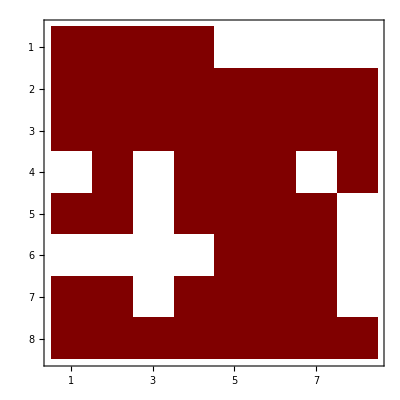

```mathematica
Amatrix8//MatrixPlot
```

the matrix is not upper triangular...
we need to orthogonalize the new basis appearing at each level.

#### check flatness

```mathematica
kin
```

{X1,X2,Y}

```mathematica
Amatrix//Dimensions
```

{50,50}

```mathematica
Amatrix[[1,1]]
```

e (Log[X1+X2]+4 Log[X1+X2+2 Y])

```mathematica
Table[A0[[i]].A0[[j]]-A0[[j]].A0[[i]]//Simplify,{i,1,Length[kin]},{j,i+1,Length[kin]}]//Flatten//DeleteCases[0]//Simplify
```

{}

```mathematica
Amatrix;
Table[D[%,kin[[i]]].D[%,kin[[j]]]-D[%,kin[[j]]].D[%,kin[[i]]]//Simplify,{i,1,Length[kin]},{j,i+1,Length[kin]}]//Flatten//DeleteCases[0]//Simplify
```

{}

```mathematica
AmatrixNeed;
Table[D[%,kin[[i]]].D[%,kin[[j]]]-D[%,kin[[j]]].D[%,kin[[i]]]//Simplify,{i,1,Length[kin]},{j,i+1,Length[kin]}]//Flatten//DeleteCases[0]//Simplify
```

{}

```mathematica
AmatrixNeed//MatrixForm
```

(e (2 Log[X1-Y]+Log[X2-Y]-4 Log[Y]+Log[X1+Y]+2 Log[X2+Y]) | 0 | e (Log[X1+Y]-Log[X2+Y]) | e (Log[X1-Y]-Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | e (-Log[X2-Y]+Log[X2+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0
0 | e (Log[X1-Y]+2 Log[X2-Y]-4 Log[Y]+2 Log[X1+Y]+Log[X2+Y]) | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2-Y]) | e (-Log[X2-Y]+Log[X1+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | e (Log[X2-Y]-Log[X2+Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0
0 | 0 | e (Log[X1+X2]-3 Log[Y]+4 Log[X1+X2+2 Y]) | e (-Log[Y]+Log[X1+X2+2 Y]) | e (-Log[X1+X2]+Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (2 Log[X1+X2]-2 Log[X1+X2+2 Y]) | 0 | 0 | 0
0 | 0 | e (Log[X1+X2]-Log[Y]) | e (4 Log[X1+X2]+Log[X1+X2-2 Y]-3 Log[Y]) | e (3 Log[X1+X2]-3 Log[X1+X2-2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (2 Log[X1+X2]-2 Log[X1+X2-2 Y]) | 0 | 0 | 0
0 | 0 | e (-Log[X1+X2]+Log[Y]) | e (-Log[X1+X2-2 Y]+Log[Y]) | e (Log[X1+X2]+3 Log[X1+X2-2 Y]-2 Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-2 Log[X1+X2]+2 Log[X1+X2-2 Y]) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]+4 Log[X1+X2-2 Y]-3 Log[Y]) | e (Log[X1+X2-2 Y]-Log[Y]) | e (-Log[X1+X2]+Log[X1+X2-2 Y]) | 0 | 0 | 0 | 0 | 0 | e (2 Log[X1+X2]-2 Log[X1+X2-2 Y]) | 0 | 0
0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[Y]) | e (4 Log[X1+X2]-3 Log[Y]+Log[X1+X2+2 Y]) | e (3 Log[X1+X2]-3 Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | e (2 Log[X1+X2]-2 Log[X1+X2+2 Y]) | 0 | 0
0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[Y]) | e (Log[Y]-Log[X1+X2+2 Y]) | e (Log[X1+X2]-2 Log[Y]+3 Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | e (-2 Log[X1+X2]+2 Log[X1+X2+2 Y]) | 0 | 0
e (-Log[X2-Y]+Log[Y]) | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2-Y]) | 0 | 0 | 0 | e (2 Log[X1-Y]+Log[X2-Y]-2 Log[Y]+Log[X1+Y]) | 0 | 0 | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0
e (-Log[Y]+Log[X1+Y]) | 0 | e (Log[X1+Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-2 Log[Y]+Log[X1+Y]+2 Log[X2+Y]) | 0 | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0
0 | e (Log[Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | e (Log[X1+Y]-Log[X2+Y]) | 0 | 0 | e (Log[X1-Y]-2 Log[Y]+2 Log[X1+Y]+Log[X2+Y]) | 0 | 0 | e (-Log[X1-Y]+Log[X1+Y]) | 0 | e (-Log[X1-Y]+Log[X1+Y])
0 | e (Log[X1-Y]-Log[Y]) | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]+2 Log[X2-Y]-2 Log[Y]+Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | e (-Log[X2-Y]+Log[X2+Y])
0 | 0 | e (Log[X1+X2]-Log[Y]) | 0 | e (-Log[X1+X2]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 e Log[X1+X2] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[Y]) | 0 | e (-Log[X1+X2]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 2 e Log[X1+X2] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y]) | e (Log[X2-Y]-Log[Y]) | 0 | 0 | e (-Log[X2-Y]+Log[X1+Y]) | 0 | e (Log[X2-Y]+Log[X1+Y]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y]) | e (-Log[Y]+Log[X2+Y]) | 0 | e (Log[X1-Y]-Log[X2+Y]) | 0 | e (Log[X1-Y]+Log[X2+Y]))

```mathematica
Amatrix8;
Table[D[%,kin[[i]]].D[%,kin[[j]]]-D[%,kin[[j]]].D[%,kin[[i]]]//Simplify,{i,1,Length[kin]},{j,i+1,Length[kin]}]//Flatten//DeleteCases[0]//Simplify
```

{}

#### recover A matrix in kinematic flow

here we use Hayden’s basis

```mathematica
basisKinematic={⟨1,2,3⟩-⟨1,2,6⟩-⟨1,3,4⟩+⟨1,3,5⟩+⟨1,3,6⟩-⟨1,4,5⟩-⟨2,3,5⟩+⟨2,4,5⟩-⟨2,4,6⟩+⟨3,4,6⟩,-⟨2,3,5⟩+⟨2,3,7⟩+⟨2,4,5⟩-⟨2,4,6⟩-⟨2,6,7⟩+⟨3,4,6⟩-⟨3,4,7⟩+⟨3,5,7⟩+⟨3,6,7⟩-⟨4,5,7⟩,-⟨1,2,6⟩+⟨1,2,9⟩-⟨1,4,5⟩+⟨1,4,9⟩-⟨1,5,9⟩-⟨1,6,9⟩+⟨2,4,5⟩-⟨2,4,6⟩+⟨2,5,9⟩+⟨4,6,9⟩,⟨1,3,5⟩-⟨1,3,8⟩-⟨1,4,5⟩+⟨1,4,8⟩-⟨3,5,8⟩+⟨4,5,8⟩,-⟨1,3,4⟩+⟨1,3,8⟩-⟨1,4,8⟩+⟨3,4,8⟩,⟨1,3,6⟩-⟨1,3,8⟩+⟨1,6,8⟩+⟨3,4,6⟩-⟨3,4,8⟩-⟨4,6,8⟩,⟨2,4,5⟩-⟨2,4,6⟩+⟨2,5,9⟩-⟨2,6,7⟩-⟨2,7,9⟩-⟨4,5,7⟩+⟨4,6,9⟩-⟨4,7,9⟩+⟨5,7,9⟩+⟨6,7,9⟩,⟨3,5,7⟩-⟨3,5,8⟩+⟨3,7,8⟩-⟨4,5,7⟩+⟨4,5,8⟩-⟨4,7,8⟩,-⟨3,4,7⟩+⟨3,4,8⟩-⟨3,7,8⟩+⟨4,7,8⟩,⟨3,4,6⟩-⟨3,4,8⟩+⟨3,6,7⟩+⟨3,7,8⟩-⟨4,6,8⟩-⟨6,7,8⟩,-⟨1,4,5⟩+⟨1,4,8⟩-⟨1,5,9⟩+⟨1,8,9⟩+⟨4,5,8⟩-⟨5,8,9⟩,-⟨1,4,8⟩+⟨1,4,9⟩-⟨1,8,9⟩+⟨4,8,9⟩,⟨1,6,8⟩-⟨1,6,9⟩+⟨1,8,9⟩-⟨4,6,8⟩+⟨4,6,9⟩-⟨4,8,9⟩,-⟨4,5,7⟩+⟨4,5,8⟩-⟨4,7,8⟩+⟨5,7,9⟩-⟨5,8,9⟩+⟨7,8,9⟩,⟨4,7,8⟩-⟨4,7,9⟩+⟨4,8,9⟩-⟨7,8,9⟩,-⟨4,6,8⟩+⟨4,6,9⟩-⟨4,8,9⟩-⟨6,7,8⟩+⟨6,7,9⟩+⟨7,8,9⟩};
```

we should do a composition : 16x26 times 26x16 to obtain this 16x16 U matrix, as we need to use the 26d quotient space.

```mathematica
UmatrixK0=Table[Coefficient[basisKinematic[[i]]/.sol,basis[[j]]],{i,1,Length[basisKinematic]},{j,1,Length[basis]}];
UK0inv=Simplify[PseudoInverse[UmatrixK0]];
```

```mathematica
UmatrixK0//Dimensions
UK0inv//Dimensions
```

{16,50}

{50,16}

```mathematica
UmatrixK//Dimensions
```

{16,6}

```mathematica
UmatrixK=UmatrixK0.Uinv;
UKinv=Simplify[Inverse[UmatrixK]];
```

Inverse::matsq: Argument {{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},«6»} at position 1 is not a non-empty square matrix.

```mathematica
AmatrixK=UmatrixK.Amatrix16.UKinv//Simplify;
%//MatrixForm
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}.Amatrix16.Inverse[{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}]

```mathematica
AmatrixK//MatrixPlot
```

MatrixPlot::mat0: Argument {{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},«6»}.Amatrix16.Inverse[{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},«4»,{0,0,0,0,0,0},{0,0,0,0,0,0},«6»}] at position 1 is not a matrix.

MatrixPlot[{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}.Amatrix16.Inverse[{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}]]

matches the known result (difference due to a change of order in basisKinematic)

```mathematica
(*-Graphics-*)
```

### ODE for ψ

Translate A-matrix to ODE of the correlator:

```mathematica
ClearAll[A]
```

```mathematica
log[a_ b_]:=log[a]+log[b];
log[a__^b__]:=b log[a];
log[a_]:=Log[a];
dlkin[a_]:= Table[D[log[a],y[i]]dy[i],{i,KinDim}]//Total;

initiate[]:=(
ClearAll[dA,M,MI,MIFirstRowCoeff];
dA[0]:=A; 
dA[i_]:=dA[i]= D[dA[i-1],y[kN]]+dA[i-1].A(*//Simplify*);
dAI[i_]:=dAI[i]=dA[i].IVec//Simplify;
M[Ddeg_]:=M[Ddeg]=dA[Ddeg-1]+( Table[a[i]dA[i-1],{i,1,Ddeg-1}]//Total)+a[0]IdentityMatrix[Adim];
MI[Ddeg_]:=M[Ddeg].IVec;
MIFirstRowCoeff[Ddeg_]:= Coefficient[MI[Ddeg][[1]],#]&/@IVec;
(*MIGeneralCoeff[Ddeg_,ψ_]:=Coefficient[MI[Ddeg].Overlap[ψ],#]&/@IVec;*)
)
```

```mathematica
initiate[];
```

ODE for X_1:

```mathematica
kN=1; 
dim=3;
KinDim=Length[kin];
dlog[a_]:=D[Log[a],y[kN]] ;
```

```mathematica
A=AmatrixK/.Thread[{X1,X2,X3,Y12,Y23}->(y/@Range[KinDim])]/.Log[a_]:>dlog[a];
Adim=A//Length;
```

```mathematica
Ddeg=5;
EchoTiming[aSol=Solve[MIFirstRowCoeff[Ddeg]==0,Table[a[i],{i,0,Ddeg-1}]]//FullSimplify]
aSoldS=aSol/.e->0//FullSimplify
```

1.29945

{{a[0]→-((2 (-1+e)^2 e (2+e (-7+6 e)))/((y[1]+y[2]+y[3]) (y[1]-y[4]) (y[1]+y[4]) (y[1]+y[2]-y[5]) (y[1]+y[2]+y[5]))),a[1]→(2 (-1+e)^2 ((18+e (-37+20 e)) y[1]+(-2+e) ((-7+8 e) y[2]+(-3+2 e) y[3])))/((y[1]+y[2]+y[3]) (y[1]-y[4]) (y[1]+y[4]) (y[1]+y[2]-y[5]) (y[1]+y[2]+y[5])),a[2]→((108+e (-248+(193-51 e) e)) y[1]^2-(-3+e) (-2+e) (-8+7 e) y[2]^2-2 (-3+e) (-2+e) (-3+2 e) y[2] y[3]-2 (-2+e) y[1] ((38+e (-59+23 e)) y[2]+(-3+2 e) (-5+3 e) y[3])+(-2+3 e) (2 (-1+e) (-1+2 e) y[4]^2+(-3+e) (-2+e) y[5]^2))/((y[1]+y[2]+y[3]) (y[1]-y[4]) (y[1]+y[4]) (y[1]+y[2]-y[5]) (y[1]+y[2]+y[5])),a[3]→((74+e (-95+31 e)) y[1]^3+(-4+e) (-3+e) y[2]^3+(-4+e) (-3+e) y[2]^2 y[3]+(-2+e) y[1]^2 ((-73+47 e) y[2]+(-27+13 e) y[3])+y[3] (-2 (-1+e) (-3+2 e) y[4]^2-(-4+e) (-3+e) y[5]^2)+y[2] (-2 (-1+e) (-7+8 e) y[4]^2-(-4+e) (-3+e) y[5]^2)+y[1] ((-3+e) (-28+17 e) y[2]^2+10 (-3+e) (-2+e) y[2] y[3]-2 (-1+e) (-7+8 e) y[4]^2-(-3+e) (-8+7 e) y[5]^2))/((y[1]+y[2]+y[3]) (y[1]-y[4]) (y[1]+y[4]) (y[1]+y[2]-y[5]) (y[1]+y[2]+y[5])),a[4]→(2-3 e)/(y[1]+y[2]+y[3])+(-4+e)/(-y[1]+y[4])+(4-e)/(y[1]+y[4])+(3-2 e)/(y[1]+y[2]-y[5])+(3-2 e)/(y[1]+y[2]+y[5])}}

{{a[0]→0,a[1]→(4 (9 y[1]+7 y[2]+3 y[3]))/((y[1]+y[2]+y[3]) (y[1]^2-y[4]^2) ((y[1]+y[2])^2-y[5]^2)),a[2]→(4 (27 y[1]^2+12 y[2]^2+9 y[2] y[3]+y[1] (38 y[2]+15 y[3])-y[4]^2-3 y[5]^2))/((y[1]+y[2]+y[3]) (y[1]^2-y[4]^2) ((y[1]+y[2])^2-y[5]^2)),a[3]→(2 (37 y[1]^3+6 y[2]^3+6 y[2]^2 y[3]+y[1]^2 (73 y[2]+27 y[3])-7 y[2] y[4]^2-3 y[3] y[4]^2-6 (y[2]+y[3]) y[5]^2+y[1] (6 y[2] (7 y[2]+5 y[3])-7 y[4]^2-12 y[5]^2)))/((y[1]+y[2]+y[3]) (y[1]-y[4]) (y[1]+y[4]) (y[1]+y[2]-y[5]) (y[1]+y[2]+y[5])),a[4]→2/(y[1]+y[2]+y[3])+4/(y[1]-y[4])+4/(y[1]+y[4])+3/(y[1]+y[2]-y[5])+3/(y[1]+y[2]+y[5])}}

## single massive exchange (FRW, g free)

### Definitions

```mathematica
dim=4;
nkin=3;
kin={X1,X2,Y};
```

Untwisted hyperplanes:

```mathematica
nBplane=4;
B[1]={1,0,Y,0,X1+Y};
B[2]={0,1,0,Y,X2+Y};
B[3]={1,1,Y,-Y,X1+X2};
B[4]={1,1,-Y,Y,X1+X2};
```

Twisted hyperplanes:

```mathematica
nTplane=6;
T[1]={1,0,0,0,0};
T[2]={0,1,0,0,0};
T[3]={0,0,1,0,0};
T[4]={0,0,1,0,2};
T[5]={0,0,0,1,0};
T[6]={0,0,0,1,2};
(*powers={g-e,g-e,e,e,e,e};*)
powers={g-e,g-e,e,e,e,e};
twists={g,e}
```

{g,e}

two twists, one for mass and the other for FRW

```mathematica
(*Could be better;
T[1]={1,0,0,0,0};
T[2]={0,1,0,0,0};
T[3]={0,0,1,0,0};
T[4]={0,0,0,1,0};
T[5]={0,0,1,0,2};
T[6]={0,0,0,1,2};*)
```

Wavefunction:

let’s deal with the inhomogeneous part: (anti-)time-ordered

```mathematica
psi=⟨1,3,5,6⟩-⟨2,4,5,6⟩;
```

Initialize the intermediate variables for computing

```mathematica
initialize[];
```

### (Overcomplete) basis functions and the associated A matrix

```mathematica
verticesList;
%//Length
```

116

```mathematica
sol=Sol[]
```

{⟨1,2,3,8⟩→((e-g) ⟨1,2,3,5⟩)/e-⟨1,2,3,7⟩,⟨1,2,4,10⟩→((e-g) ⟨1,2,4,6⟩)/e-⟨1,2,4,9⟩,⟨1,2,5,10⟩→((e-g) ⟨1,2,5,6⟩)/e-⟨1,2,5,9⟩,⟨1,2,6,8⟩→(-1+g/e) ⟨1,2,5,6⟩-⟨1,2,6,7⟩,⟨1,2,7,10⟩→(-1+g/e) ⟨1,2,6,7⟩-⟨1,2,7,9⟩,⟨1,2,8,9⟩→((e-g) ⟨1,2,5,9⟩)/e-⟨1,2,7,9⟩,⟨1,2,8,10⟩→((e-g)^2 ⟨1,2,5,6⟩-e (e-g) ⟨1,2,5,9⟩+e (e-g) ⟨1,2,6,7⟩+e^2 ⟨1,2,7,9⟩)/e^2,⟨1,3,4,9⟩→1/(2 e^2)(g^2 ⟨1,3,5,6⟩+e^2 (⟨1,3,4,5⟩+⟨1,3,4,6⟩-2 ⟨1,3,4,7⟩+⟨1,3,5,6⟩-⟨1,3,5,9⟩+⟨1,3,6,7⟩-⟨1,4,5,9⟩-⟨1,4,6,8⟩-⟨1,4,6,9⟩)+e g (-⟨1,3,4,5⟩-⟨1,3,4,6⟩-2 ⟨1,3,5,6⟩+⟨1,3,5,9⟩-⟨1,3,6,7⟩+⟨1,4,5,9⟩+⟨1,4,6,8⟩+⟨1,4,6,9⟩)),⟨1,3,4,10⟩→-1/(2 e^2)(g^2 ⟨1,3,5,6⟩+e g (⟨1,3,4,5⟩+⟨1,3,4,6⟩-2 ⟨1,3,5,6⟩+⟨1,3,5,9⟩-⟨1,3,6,7⟩+⟨1,4,5,9⟩+⟨1,4,6,8⟩+⟨1,4,6,9⟩)-e^2 (⟨1,3,4,5⟩+⟨1,3,4,6⟩-2 ⟨1,3,4,8⟩-⟨1,3,5,6⟩+⟨1,3,5,9⟩-⟨1,3,6,7⟩+⟨1,4,5,9⟩+⟨1,4,6,8⟩+⟨1,4,6,9⟩)),⟨1,3,5,10⟩→((e-g) ⟨1,3,5,6⟩)/e-⟨1,3,5,9⟩,⟨1,3,6,8⟩→(-1+g/e) ⟨1,3,5,6⟩-⟨1,3,6,7⟩,⟨1,3,7,10⟩→(-1+g/e) ⟨1,3,6,7⟩-⟨1,3,7,9⟩,⟨1,3,8,9⟩→((e-g) ⟨1,3,5,9⟩)/e-⟨1,3,7,9⟩,⟨1,3,8,10⟩→((e-g)^2 ⟨1,3,5,6⟩-e (e-g) ⟨1,3,5,9⟩+e (e-g) ⟨1,3,6,7⟩+e^2 ⟨1,3,7,9⟩)/e^2,⟨1,4,5,10⟩→((e-g) ⟨1,4,5,6⟩)/e-⟨1,4,5,9⟩,⟨1,4,6,10⟩→(g ⟨1,4,5,6⟩-e (⟨1,4,5,6⟩+⟨1,4,6,7⟩+⟨1,4,6,8⟩+⟨1,4,6,9⟩))/e,⟨1,4,7,9⟩→1/(2 e^2)(-g^2 ⟨1,3,5,6⟩+e g (⟨1,3,4,5⟩+⟨1,3,4,6⟩+2 ⟨1,3,5,6⟩-⟨1,3,5,9⟩+⟨1,3,6,7⟩-⟨1,4,5,9⟩-⟨1,4,6,8⟩-⟨1,4,6,9⟩)+e^2 (-⟨1,3,4,5⟩-⟨1,3,4,6⟩-⟨1,3,5,6⟩+⟨1,3,5,9⟩-⟨1,3,6,7⟩-2 ⟨1,3,7,9⟩+⟨1,4,5,9⟩+⟨1,4,6,8⟩+⟨1,4,6,9⟩)),⟨1,4,7,10⟩→1/(2 e^2)(g^2 ⟨1,3,5,6⟩+e^2 (⟨1,3,4,5⟩+⟨1,3,4,6⟩+⟨1,3,5,6⟩-⟨1,3,5,9⟩+⟨1,3,6,7⟩+2 ⟨1,3,7,9⟩-⟨1,4,5,9⟩-2 ⟨1,4,6,7⟩-⟨1,4,6,8⟩-⟨1,4,6,9⟩)+e g (-⟨1,3,4,5⟩-⟨1,3,4,6⟩-2 ⟨1,3,5,6⟩+⟨1,3,5,9⟩-⟨1,3,6,7⟩+⟨1,4,5,9⟩+2 ⟨1,4,6,7⟩+⟨1,4,6,8⟩+⟨1,4,6,9⟩)),⟨1,4,8,9⟩→1/(2 e^2)(g^2 ⟨1,3,5,6⟩-e g (⟨1,3,4,5⟩+⟨1,3,4,6⟩+2 ⟨1,3,5,6⟩-⟨1,3,5,9⟩+⟨1,3,6,7⟩+⟨1,4,5,9⟩-⟨1,4,6,8⟩+⟨1,4,6,9⟩)+e^2 (⟨1,3,4,5⟩+⟨1,3,4,6⟩+⟨1,3,5,6⟩-⟨1,3,5,9⟩+⟨1,3,6,7⟩+2 ⟨1,3,7,9⟩+⟨1,4,5,9⟩-⟨1,4,6,8⟩+⟨1,4,6,9⟩)),⟨1,4,8,10⟩→-1/(2 e^2)(g^2 ⟨1,3,5,6⟩-e g (⟨1,3,4,5⟩+⟨1,3,4,6⟩+2 ⟨1,3,5,6⟩-⟨1,3,5,9⟩+⟨1,3,6,7⟩+⟨1,4,5,9⟩+⟨1,4,6,8⟩+⟨1,4,6,9⟩)+e^2 (⟨1,3,4,5⟩+⟨1,3,4,6⟩+⟨1,3,5,6⟩-⟨1,3,5,9⟩+⟨1,3,6,7⟩+2 ⟨1,3,7,9⟩+⟨1,4,5,9⟩+⟨1,4,6,8⟩+⟨1,4,6,9⟩)),⟨1,5,6,9⟩→0,⟨1,5,6,10⟩→0,⟨1,6,7,9⟩→0,⟨1,6,7,10⟩→0,⟨1,6,8,9⟩→0,⟨1,6,8,10⟩→0,⟨2,3,4,9⟩→1/(2 e^2)(g^2 (⟨2,3,5,6⟩+⟨2,4,5,6⟩)+e^2 (⟨2,3,4,5⟩+⟨2,3,4,6⟩-2 ⟨2,3,4,7⟩+⟨2,3,5,6⟩-⟨2,3,5,8⟩-⟨2,3,5,9⟩+⟨2,3,6,7⟩+⟨2,4,5,6⟩-⟨2,4,5,9⟩+⟨2,4,6,7⟩)-e g (⟨2,3,4,5⟩+⟨2,3,4,6⟩+2 ⟨2,3,5,6⟩-⟨2,3,5,8⟩-⟨2,3,5,9⟩+⟨2,3,6,7⟩+2 ⟨2,4,5,6⟩-⟨2,4,5,9⟩+⟨2,4,6,7⟩)),⟨2,3,4,10⟩→-1/(2 e^2)(g^2 (⟨2,3,5,6⟩+⟨2,4,5,6⟩)+e g (⟨2,3,4,5⟩+⟨2,3,4,6⟩-2 ⟨2,3,5,6⟩+⟨2,3,5,8⟩+⟨2,3,5,9⟩-⟨2,3,6,7⟩-2 ⟨2,4,5,6⟩+⟨2,4,5,9⟩-⟨2,4,6,7⟩)-e^2 (⟨2,3,4,5⟩+⟨2,3,4,6⟩-2 ⟨2,3,4,8⟩-⟨2,3,5,6⟩+⟨2,3,5,8⟩+⟨2,3,5,9⟩-⟨2,3,6,7⟩-⟨2,4,5,6⟩+⟨2,4,5,9⟩-⟨2,4,6,7⟩)),⟨2,3,5,10⟩→((e-g) ⟨2,3,5,6⟩)/e-⟨2,3,5,7⟩-⟨2,3,5,8⟩-⟨2,3,5,9⟩,⟨2,3,6,8⟩→(-1+g/e) ⟨2,3,5,6⟩-⟨2,3,6,7⟩,⟨2,3,7,10⟩→(g (⟨2,3,5,7⟩+⟨2,3,6,7⟩)-e (⟨2,3,5,7⟩+⟨2,3,6,7⟩+⟨2,3,7,9⟩))/e,⟨2,3,8,9⟩→((e-g) ⟨2,3,5,9⟩)/e-⟨2,3,7,9⟩,⟨2,3,8,10⟩→((e-g)^2 ⟨2,3,5,6⟩-e (e-g) ⟨2,3,5,8⟩-e (e-g) ⟨2,3,5,9⟩+e (e-g) ⟨2,3,6,7⟩+e^2 ⟨2,3,7,9⟩)/e^2,⟨2,4,5,10⟩→((e-g) ⟨2,4,5,6⟩)/e-⟨2,4,5,9⟩,⟨2,4,6,8⟩→(-1+g/e) ⟨2,4,5,6⟩-⟨2,4,6,7⟩,⟨2,4,7,9⟩→-1/(2 e^2)(g^2 (⟨2,3,5,6⟩+⟨2,4,5,6⟩)+e^2 (⟨2,3,4,5⟩+⟨2,3,4,6⟩+⟨2,3,5,6⟩-⟨2,3,5,8⟩-⟨2,3,5,9⟩+⟨2,3,6,7⟩+2 ⟨2,3,7,9⟩+⟨2,4,5,6⟩-⟨2,4,5,9⟩+⟨2,4,6,7⟩)-e g (⟨2,3,4,5⟩+⟨2,3,4,6⟩+2 ⟨2,3,5,6⟩-⟨2,3,5,8⟩-⟨2,3,5,9⟩+⟨2,3,6,7⟩+2 ⟨2,4,5,6⟩-⟨2,4,5,9⟩+⟨2,4,6,7⟩)),⟨2,4,7,10⟩→1/(2 e^2)(g^2 (⟨2,3,5,6⟩+⟨2,4,5,6⟩)+e^2 (⟨2,3,4,5⟩+⟨2,3,4,6⟩+⟨2,3,5,6⟩-⟨2,3,5,8⟩-⟨2,3,5,9⟩+⟨2,3,6,7⟩+2 ⟨2,3,7,9⟩+⟨2,4,5,6⟩-⟨2,4,5,9⟩-⟨2,4,6,7⟩)+e g (-⟨2,3,4,5⟩-⟨2,3,4,6⟩-2 ⟨2,3,5,6⟩+⟨2,3,5,8⟩+⟨2,3,5,9⟩-⟨2,3,6,7⟩-2 ⟨2,4,5,6⟩+⟨2,4,5,9⟩+⟨2,4,6,7⟩)),⟨2,4,8,9⟩→1/(2 e^2)(g^2 (⟨2,3,5,6⟩+⟨2,4,5,6⟩)+e^2 (⟨2,3,4,5⟩+⟨2,3,4,6⟩+⟨2,3,5,6⟩-⟨2,3,5,8⟩-⟨2,3,5,9⟩+⟨2,3,6,7⟩+2 ⟨2,3,7,9⟩+⟨2,4,5,6⟩+⟨2,4,5,9⟩+⟨2,4,6,7⟩)-e g (⟨2,3,4,5⟩+⟨2,3,4,6⟩+2 ⟨2,3,5,6⟩-⟨2,3,5,8⟩-⟨2,3,5,9⟩+⟨2,3,6,7⟩+2 ⟨2,4,5,6⟩+⟨2,4,5,9⟩+⟨2,4,6,7⟩)),⟨2,4,8,10⟩→1/(2 e^2)(g^2 (-⟨2,3,5,6⟩+⟨2,4,5,6⟩)+e g (⟨2,3,4,5⟩+⟨2,3,4,6⟩+2 ⟨2,3,5,6⟩-⟨2,3,5,8⟩-⟨2,3,5,9⟩+⟨2,3,6,7⟩-2 ⟨2,4,5,6⟩+⟨2,4,5,9⟩-⟨2,4,6,7⟩)-e^2 (⟨2,3,4,5⟩+⟨2,3,4,6⟩+⟨2,3,5,6⟩-⟨2,3,5,8⟩-⟨2,3,5,9⟩+⟨2,3,6,7⟩+2 ⟨2,3,7,9⟩-⟨2,4,5,6⟩+⟨2,4,5,9⟩-⟨2,4,6,7⟩)),⟨2,5,6,7⟩→0,⟨2,5,6,8⟩→0,⟨2,5,7,9⟩→0,⟨2,5,7,10⟩→0,⟨2,5,8,9⟩→0,⟨2,5,8,10⟩→0,⟨3,4,5,9⟩→(g (⟨3,5,6,8⟩+⟨3,5,6,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩)-e (2 ⟨3,4,5,7⟩+⟨3,5,6,8⟩+⟨3,5,6,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩))/(2 e),⟨3,4,5,10⟩→(-g (⟨3,5,6,8⟩+⟨3,5,6,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩)+e (-2 ⟨3,4,5,8⟩+⟨3,5,6,8⟩+⟨3,5,6,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩))/(2 e),⟨3,4,6,7⟩→-⟨3,4,5,7⟩,⟨3,4,6,8⟩→-⟨3,4,5,8⟩,⟨3,4,6,9⟩→(-g (⟨3,5,6,8⟩+⟨3,5,6,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩)+e (2 ⟨3,4,5,7⟩+⟨3,5,6,8⟩+⟨3,5,6,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩))/(2 e),⟨3,4,6,10⟩→(e (2 ⟨3,4,5,8⟩-⟨3,5,6,8⟩-⟨3,5,6,9⟩-⟨4,5,6,8⟩-⟨4,5,6,9⟩)+g (⟨3,5,6,8⟩+⟨3,5,6,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩))/(2 e),⟨3,5,6,10⟩→-⟨3,5,6,7⟩-⟨3,5,6,8⟩-⟨3,5,6,9⟩,⟨3,5,7,10⟩→(-1+g/e) ⟨3,5,6,7⟩-⟨3,5,7,9⟩,⟨3,5,8,9⟩→((e-g) ⟨3,5,6,9⟩)/e-⟨3,5,7,9⟩,⟨3,5,8,10⟩→(-((e-g) ⟨3,5,6,8⟩)-(e-g) ⟨3,5,6,9⟩+e ⟨3,5,7,9⟩)/e,⟨3,6,7,9⟩→-⟨3,5,7,9⟩,⟨3,6,7,10⟩→((e-g) ⟨3,5,6,7⟩)/e+⟨3,5,7,9⟩,⟨3,6,8,9⟩→(-1+g/e) ⟨3,5,6,9⟩+⟨3,5,7,9⟩,⟨3,6,8,10⟩→((e-g) ⟨3,5,6,8⟩+(e-g) ⟨3,5,6,9⟩-e ⟨3,5,7,9⟩)/e,⟨4,5,6,10⟩→-⟨4,5,6,7⟩-⟨4,5,6,8⟩-⟨4,5,6,9⟩,⟨4,5,7,9⟩→(-g (⟨3,5,6,8⟩+⟨3,5,6,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩)+e (⟨3,5,6,8⟩+⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩))/(2 e),⟨4,5,7,10⟩→(g (⟨3,5,6,8⟩+⟨3,5,6,9⟩+2 ⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩)-e (⟨3,5,6,8⟩+⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩+2 ⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩))/(2 e),⟨4,5,8,9⟩→(g (⟨3,5,6,8⟩+⟨3,5,6,9⟩+⟨4,5,6,8⟩-⟨4,5,6,9⟩)-e (⟨3,5,6,8⟩+⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩-⟨4,5,6,9⟩))/(2 e),⟨4,5,8,10⟩→(e (⟨3,5,6,8⟩+⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩-⟨4,5,6,8⟩-⟨4,5,6,9⟩)+g (-⟨3,5,6,8⟩-⟨3,5,6,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩))/(2 e),⟨4,6,7,9⟩→(g (⟨3,5,6,8⟩+⟨3,5,6,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩)-e (⟨3,5,6,8⟩+⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩))/(2 e),⟨4,6,7,10⟩→(-g (⟨3,5,6,8⟩+⟨3,5,6,9⟩+2 ⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩)+e (⟨3,5,6,8⟩+⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩+2 ⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩))/(2 e),⟨4,6,8,9⟩→(-g (⟨3,5,6,8⟩+⟨3,5,6,9⟩+⟨4,5,6,8⟩-⟨4,5,6,9⟩)+e (⟨3,5,6,8⟩+⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩-⟨4,5,6,9⟩))/(2 e),⟨4,6,8,10⟩→(g (⟨3,5,6,8⟩+⟨3,5,6,9⟩-⟨4,5,6,8⟩-⟨4,5,6,9⟩)+e (-⟨3,5,6,8⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩))/(2 e),⟨5,6,7,9⟩→0,⟨5,6,7,10⟩→0,⟨5,6,8,9⟩→0,⟨5,6,8,10⟩→0}

```mathematica
bdyBasis=BdyBasis[0];
%//Transpose//MatrixForm
```

({3} | {⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,7,9⟩}
{4} | {⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨4,5,7,9⟩}
{1,2} | {⟨1,2,5,6⟩,⟨1,2,5,9⟩,⟨1,2,6,7⟩,⟨1,2,7,9⟩}
{1,3} | {⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨1,3,7,9⟩}
{1,4} | {⟨1,4,5,6⟩,⟨1,4,5,9⟩,⟨1,4,6,7⟩,⟨1,4,6,8⟩,⟨1,4,6,9⟩,⟨1,4,7,9⟩}
{2,3} | {⟨2,3,5,6⟩,⟨2,3,5,7⟩,⟨2,3,5,8⟩,⟨2,3,5,9⟩,⟨2,3,6,7⟩,⟨2,3,7,9⟩}
{2,4} | {⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨2,4,7,9⟩}
{3,4} | {⟨3,4,5,7⟩,⟨3,4,5,8⟩,⟨3,4,5,9⟩}
{1,2,3} | {⟨1,2,3,5⟩,⟨1,2,3,7⟩}
{1,2,4} | {⟨1,2,4,6⟩,⟨1,2,4,9⟩}
{1,3,4} | {⟨1,3,4,5⟩,⟨1,3,4,6⟩,⟨1,3,4,7⟩,⟨1,3,4,8⟩,⟨1,3,4,9⟩}
{2,3,4} | {⟨2,3,4,5⟩,⟨2,3,4,6⟩,⟨2,3,4,7⟩,⟨2,3,4,8⟩,⟨2,3,4,9⟩}
{1,2,3,4} | {⟨1,2,3,4⟩})

```mathematica
Bdy=bdyBasis[[1]];
funcTree@Bdy
```

-Graphics-

# codimension | 0 | 1 | 2 | 3 | 4
# boundaries | 0 | 2 | 6 | 4 | 1

```mathematica
basis=bdyBasis[[2]]//Flatten
```

{⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,7,9⟩,⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨4,5,7,9⟩,⟨1,2,5,6⟩,⟨1,2,5,9⟩,⟨1,2,6,7⟩,⟨1,2,7,9⟩,⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨1,3,7,9⟩,⟨1,4,5,6⟩,⟨1,4,5,9⟩,⟨1,4,6,7⟩,⟨1,4,6,8⟩,⟨1,4,6,9⟩,⟨1,4,7,9⟩,⟨2,3,5,6⟩,⟨2,3,5,7⟩,⟨2,3,5,8⟩,⟨2,3,5,9⟩,⟨2,3,6,7⟩,⟨2,3,7,9⟩,⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨2,4,7,9⟩,⟨3,4,5,7⟩,⟨3,4,5,8⟩,⟨3,4,5,9⟩,⟨1,2,3,5⟩,⟨1,2,3,7⟩,⟨1,2,4,6⟩,⟨1,2,4,9⟩,⟨1,3,4,5⟩,⟨1,3,4,6⟩,⟨1,3,4,7⟩,⟨1,3,4,8⟩,⟨1,3,4,9⟩,⟨2,3,4,5⟩,⟨2,3,4,6⟩,⟨2,3,4,7⟩,⟨2,3,4,8⟩,⟨2,3,4,9⟩,⟨1,2,3,4⟩}

```mathematica
basis//Length
```

50

```mathematica
EchoTiming[A = AMatrix[]];
A[[1]] // MatrixForm
```

14.7167

(e/(X1+X2)+(2 g)/(X1+X2+2 Y) | e/(X1+X2+2 Y) | -e/(X1+X2)+e/(X1+X2+2 Y) | (2 e)/(X1+X2)-(2 e)/(X1+X2+2 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e/(X1+X2) | (2 g)/(X1+X2)-e/(-X1-X2+2 Y) | -(e-2 g)/(X1+X2)+(-e+2 g)/(-X1-X2+2 Y) | (2 e)/(X1+X2)+(2 e)/(-X1-X2+2 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-e/(X1+X2) | e/(-X1-X2+2 Y) | e/(X1+X2)+(e-2 g)/(-X1-X2+2 Y) | -(2 e)/(X1+X2)-(2 e)/(-X1-X2+2 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-e+g)/(X1+X2) | 0 | (e-g)/(X1+X2) | -(2 (e-g))/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (e-g)/(X1+X2)+(e-g)/(-X1-X2+2 Y) | (e-g)/(X1+X2)+(e-g)/(-X1-X2+2 Y) | -(2 e)/(X1+X2)-(2 e)/(-X1-X2+2 Y) | e/(X1+X2)-(2 g)/(-X1-X2+2 Y) | (e-g)/(X1+X2)-g/(-X1-X2+2 Y) | -g/(X1+X2)-g/(-X1-X2+2 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (e-g)/(X1+X2)+(-e+g)/(X1+X2+2 Y) | (e-g)/(X1+X2)+(-e+g)/(X1+X2+2 Y) | -(2 e)/(X1+X2)+(2 e)/(X1+X2+2 Y) | e/(X1+X2) | (e+g)/(X1+X2)+g/(X1+X2+2 Y) | g/(X1+X2)-g/(X1+X2+2 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(e-g)/(X1+X2)+(e-g)/(X1+X2+2 Y) | -(e-g)/(X1+X2)+(e-g)/(X1+X2+2 Y) | (2 e)/(X1+X2)-(2 e)/(X1+X2+2 Y) | -e/(X1+X2) | -(e-g)/(X1+X2)-g/(X1+X2+2 Y) | g/(X1+X2)+g/(X1+X2+2 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -g/(-X1+Y)+e/(X1+Y) | 0 | e/(-X1+Y)+e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -g/(-X1+Y)+e/(X1+Y) | 0 | -e/(-X1+Y)-e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (-e+g)/(X1+Y) | 0 | (-e+g)/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (e-g)/(X1+Y) | 0 | (-e+g)/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e/(X1+Y) | -e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -g/(-X1+Y)+e/(X1+Y) | 0 | e/(-X1+Y)+e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (e-g)/(-X1+Y) | -e/(-X1+Y)-e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -g/(-X1+Y)+e/(X1+Y) | 0 | -e/(-X1+Y)-e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-e+g)/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-e+g)/(X1+Y) | 0 | (-e+g)/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (-e+g)/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (e-g)/(X1+Y) | 0 | (-e+g)/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e/(X1+Y)+(2 e)/(-2 X1-X2+Y) | -e/(-X1+Y)+(2 e)/(-2 X1-X2+Y) | (2 e)/(-2 X1-X2+Y)+(2 e)/(2 X1+X2+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y)+e/(X1+Y)+(2 (e-2 g))/(-2 X1-X2+Y)+(2 e)/(2 X1+X2+Y) | -(2 e)/(-2 X1-X2+Y)-(2 e)/(2 X1+X2+Y) | e/(X1+Y)+(2 e)/(-2 X1-X2+Y) | -e/(-X1+Y)+(2 e)/(-2 X1-X2+Y) | (2 e)/(-2 X1-X2+Y)+(2 e)/(2 X1+X2+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (-e+g)/(2 (-X1+Y))+(-e+g)/(2 (X1+Y)) | (-e+g)/(2 (-X1+Y))+(-e+g)/(2 (X1+Y)) | e/(-X1+Y)+e/(X1+Y) | 0 | (-e+g)/(2 (-X1+Y))+(-e+g)/(2 (X1+Y)) | (e-g)/(2 (-X1+Y))+(-e+g)/(2 (X1+Y))+(2 (e-g))/(2 X1+X2+Y) | 0 | 0 | 0 | 0 | (e^2-2 e g+g^2)/(2 e (-X1+Y))+(e^2-2 e g+g^2)/(2 e (X1+Y)) | (-e+g)/(2 (-X1+Y))+(-e+g)/(2 (X1+Y)) | (e-g)/(2 (-X1+Y))+(e-g)/(2 (X1+Y)) | e/(-X1+Y)+e/(X1+Y) | (2 (e-g))/(2 X1+X2+Y) | (-e-g)/(2 (-X1+Y))+(e+g)/(2 (X1+Y))-(2 (e-g))/(2 X1+X2+Y) | 0 | (-e+g)/(2 (-X1+Y))+(-e+g)/(2 (X1+Y)) | (e-g)/(2 (-X1+Y))+(-e+g)/(2 (X1+Y))+(2 (e-g))/(2 X1+X2+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (e-g)/(2 (-X1+Y))+(e-g)/(2 (X1+Y)) | (e-g)/(2 (-X1+Y))+(e-g)/(2 (X1+Y)) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (-e+g)/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-e+g)/(X1+Y) | 0 | (-e+g)/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (e-g)/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (e-g)/(-X1+Y) | 0 | 0 | (e-g)/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(2 (e-g))/(2 X1+X2+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 (e-g))/(2 X1+X2+Y) | (2 (e-g))/(2 X1+X2+Y) | 0 | 0 | -(2 (e-g))/(2 X1+X2+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e/(X1+2 X2+Y) | -e/(-X1-2 X2+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -g/(-X1-2 X2+Y)+e/(X1+2 X2+Y) | -e/(X1+2 X2+Y) | e/(-X1-2 X2+Y) | 0 | e/(-X1-2 X2+Y)+e/(X1+2 X2+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(e-g)/(X1+2 X2+Y)+(-e+g)/(X1+3 Y) | 0 | 0 | -e/(-X1+Y)-e/(X1+3 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (e-g)/(X1+2 X2+Y)+(-e+g)/(X1+3 Y) | -e/(-X1+Y)+(-e+g)/(X1+2 X2+Y)+(e+g)/(X1+3 Y) | e/(X1+3 Y) | e/(-X1+Y)+e/(X1+3 Y) | (e-g)/(X1+2 X2+Y)+(-e+g)/(X1+3 Y) | -e/(-X1+Y)-e/(X1+3 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (-e+g)/(X1+Y)+(-e+g)/(-X1-2 X2+Y) | (-e+g)/(X1+Y)+(-e+g)/(-X1+3 Y) | e/(X1+Y)+e/(-X1+3 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-e g+g^2)/(e (X1+Y))+(-e g+g^2)/(e (-X1-2 X2+Y)) | e/(X1+Y) | (e+g)/(X1+Y)+(e-g)/(-X1-2 X2+Y)-e/(-X1+3 Y) | g/(X1+Y)+g/(-X1+3 Y) | (e-g)/(X1+Y)+(e-g)/(-X1-2 X2+Y) | e/(X1+Y)+e/(-X1+3 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (e-g)/(-X1+3 Y) | e/(-X1+Y)-e/(-X1+3 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(-X1+Y) | e/(-X1+3 Y) | -e/(-X1+Y)-g/(-X1+3 Y) | 0 | e/(-X1+Y)-e/(-X1+3 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-e+g)/(X1+2 X2+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-e+g)/(X1+2 X2+Y) | (e-g)/(X1+2 X2+Y) | 0 | 0 | (-e+g)/(X1+2 X2+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (e-g)/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (e-g)/(-X1+Y) | 0 | (-e+g)/(-X1+Y) | 0 | (e-g)/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -e/(-X1+Y) | e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y)+g/(X1+Y) | 0 | -e/(-X1+Y)-e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (e-g)/(2 (-X1+Y))+(e-g)/(2 (X1+Y)) | (e-g)/(2 (-X1+Y))+(e-g)/(2 (X1+Y)) | -e/(-X1+Y)-e/(X1+Y) | 0 | (e-g)/(2 (-X1+Y))+(e-g)/(2 (X1+Y)) | (e-g)/(2 (-X1+Y))+(-e+g)/(2 (X1+Y)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-e^2+2 e g-g^2)/(2 e (-X1+Y))+(-e^2+2 e g-g^2)/(2 e (X1+Y)) | 0 | (e-g)/(2 (-X1+Y))+(e-g)/(2 (X1+Y)) | (e-g)/(2 (-X1+Y))+(e-g)/(2 (X1+Y)) | (-e+g)/(2 (-X1+Y))+(-e+g)/(2 (X1+Y)) | -e/(-X1+Y)-e/(X1+Y) | (-e^2+2 e g-g^2)/(2 e (-X1+Y))+(-e^2+2 e g-g^2)/(2 e (X1+Y)) | (-e-g)/(2 (-X1+Y))+(e+g)/(2 (X1+Y)) | (-e+g)/(2 (-X1+Y))+(-e+g)/(2 (X1+Y)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-e+g)/(2 (-X1+Y))+(-e+g)/(2 (X1+Y)) | (-e+g)/(2 (-X1+Y))+(-e+g)/(2 (X1+Y)) | 0 | 0 | 0
0 | 0 | 0 | 0 | (e-g)/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (e-g)/(-X1+Y) | 0 | (e-g)/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-e+g)/(X1+X2) | 0 | 0 | 0 | (e-g)/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 (e-g))/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (-e+g)/(X1+X2) | 0 | 0 | 0 | (e-g)/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 (e-g))/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | -e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -g/(-X1+Y)+e/(X1+Y) | -e/(-X1+Y)-e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (e-g)/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (e-g)/(X1+Y) | (-e+g)/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (e-g)/X1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-e+g)/X1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (e-g)/X1 | 0 | 0 | 0 | 0 | 0 | 0 | (-e+g)/X1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (e-g)/X1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-e+g)/X1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (e-g)/X1 | 0 | 0 | 0 | 0 | 0 | 0 | (-e+g)/X1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (-e+g)/(2 (-X1+Y))+(-e+g)/(2 (X1+Y)) | (-e+g)/(2 (-X1+Y))+(-e+g)/(2 (X1+Y)) | 0 | 0 | (-e+g)/(2 (-X1+Y))+(-e+g)/(2 (X1+Y)) | (-e+g)/(2 (-X1+Y))+(-e+g)/(2 (X1+Y)) | 0 | 0 | 0 | 0 | -(e-g)/(X1+X2)+(-3 e^2+4 e g-g^2)/(2 e (-X1+Y))+(-e^2+2 e g-g^2)/(2 e (X1+Y)) | (3 e-g)/(2 (-X1+Y))+(3 e-g)/(2 (X1+Y)) | (-e+g)/(2 (-X1+Y))+(-e+g)/(2 (X1+Y)) | 0 | (e-g)/(X1+X2)+(e-g)/(-X1+Y) | (-e-g)/(2 (-X1+Y))+(-e-g)/(2 (X1+Y)) | 0 | (e-g)/(2 (-X1+Y))+(e-g)/(2 (X1+Y)) | (e-g)/(2 (-X1+Y))+(e-g)/(2 (X1+Y)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(e-g)/(X1+X2)+(-3 e-g)/(2 (-X1+Y))+(3 e+g)/(2 (X1+Y)) | (e-g)/(X1+X2)+(e-g)/(2 (-X1+Y))+(-e+g)/(2 (X1+Y)) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (e-g)/(X1+X2) | 0 | 0 | 0 | (-e+g)/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (e-g)/(X1+X2) | (-e+g)/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (e-g)/(X1+Y) | 0 | 0 | 0 | 0 | 0 | (e-g)/(X1+Y) | 0 | (-e+g)/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-e+g)/(-X1+Y) | 0 | 0 | 0 | 0 | (-e+g)/(-X1+Y) | 0 | 0 | (e-g)/(-X1+Y) | 0 | 0 | 0 | 0 | 0
0 | (e-g)/(2 (-X1+Y))+(e-g)/(2 (X1+Y)) | (e-g)/(2 (-X1+Y))+(e-g)/(2 (X1+Y)) | 0 | 0 | (e-g)/(2 (-X1+Y))+(e-g)/(2 (X1+Y)) | (e-g)/(2 (-X1+Y))+(e-g)/(2 (X1+Y)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(e-g)/(X1+X2)+(e^2-2 e g+g^2)/(2 e (-X1+Y))+(3 e^2-4 e g+g^2)/(2 e (X1+Y)) | -e/(-X1+Y)-e/(X1+Y) | (-e+g)/(2 (-X1+Y))+(-e+g)/(2 (X1+Y)) | (-3 e+g)/(2 (-X1+Y))+(-3 e+g)/(2 (X1+Y)) | (e-g)/(2 (-X1+Y))+(e-g)/(2 (X1+Y)) | 0 | (e-g)/(X1+X2)+(e^2-2 e g+g^2)/(2 e (-X1+Y))+(-e^2+g^2)/(2 e (X1+Y)) | (e+g)/(2 (-X1+Y))+(e+g)/(2 (X1+Y)) | (e-g)/(2 (-X1+Y))+(e-g)/(2 (X1+Y)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(e-g)/(X1+X2)+(-3 e-g)/(2 (-X1+Y))+(3 e+g)/(2 (X1+Y)) | (e-g)/(X1+X2)+(e-g)/(2 (-X1+Y))+(-e+g)/(2 (X1+Y)) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (e-g)/(X1+X2) | 0 | 0 | 0 | 0 | 0 | (-e+g)/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (e-g)/(X1+X2) | (-e+g)/(X1+X2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-e+g)/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-e+g)/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-e+g)/(-X1+Y) | 0 | (e-g)/(-X1+Y) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (e-g)/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (e-g)/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (e-g)/(X1+Y) | 0 | 0 | (-e+g)/(X1+Y) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (e-g)/X1 | 0 | 0 | 0 | (e-g)/X1 | 0 | 0 | 0 | (-e+g)/X1 | 0 | 0 | 0 | (-e+g)/X1)

```mathematica
EchoTiming[A0 = AMatrix[0]];
A0[[1]] // MatrixPlot
```

13.3956

-Graphics-

### Basis reduction: filtering

#### start

The stored A-matrix from previous overcomplete set of basis functions:

ClearAll[basis, A0, A];
Get[FileNameJoin[{NotebookDirectory[], "storage", "basis_single-massive-exchange"}]];
Get[FileNameJoin[{NotebookDirectory[], "storage", "A_single-massive-exchange"}]];
Get[FileNameJoin[{NotebookDirectory[], "storage", "A0_single-massive-exchange"}]];

basis // Length
A0[[1]] // Length
A[[1]] // Length

50

50

44

```mathematica
Amatrix=ATotal[A0,twists];
%//MatrixForm
```

(2 e Log[X1+X2+2 Y]+2 g Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 e Log[X1+X2]+2 g Log[X1+X2] | e (2 Log[X1+X2]-2 Log[X1+X2-2 Y])+g (2 Log[X1+X2]-2 Log[X1+X2-2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 e Log[X1+X2-2 Y]+2 g Log[X1+X2-2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+X2]-Log[Y])+g (Log[X1+X2]-Log[Y]) | 0 | e (-Log[X1+X2]+Log[Y])+g (-Log[X1+X2]+Log[Y]) | 2 e Log[X1+X2]+2 g Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 e Log[X1+X2-2 Y]+2 g Log[X1+X2-2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 e Log[X1+X2]+2 g Log[X1+X2] | e (2 Log[X1+X2]-2 Log[X1+X2+2 Y])+g (2 Log[X1+X2]-2 Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 e Log[X1+X2+2 Y]+2 g Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[Y])+g (Log[X1+X2]-Log[Y]) | 0 | e (-Log[X1+X2]+Log[Y])+g (-Log[X1+X2]+Log[Y]) | 2 e Log[X1+X2]+2 g Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]+Log[X2-Y])+g (Log[X1-Y]+Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X2+Y])+g (Log[Y]-Log[X2+Y]) | e (Log[X1-Y]+Log[X2+Y])+g (Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y])+g (-Log[Y]+Log[X1+Y]) | 0 | e (Log[X2-Y]+Log[X1+Y])+g (Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y])+g (Log[Y]-Log[X1+Y]) | e (-Log[Y]+Log[X2+Y])+g (-Log[Y]+Log[X2+Y]) | e (Log[X1+Y]+Log[X2+Y])+g (Log[X1+Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]+Log[X2+Y])+g (Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (Log[X1-Y]-Log[X2-Y])+g (Log[X1-Y]-Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-Y]+Log[Y])+g (-Log[X2-Y]+Log[Y]) | e (Log[X1-Y]+Log[X2-Y])+g (Log[X1-Y]+Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+Y]-Log[X2+Y])+g (Log[X1+Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y])+g (-Log[Y]+Log[X1+Y]) | 0 | e (Log[X1+Y]+Log[X2+Y])+g (Log[X1+Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e (-Log[X2-Y]+Log[X1+Y])+g (-Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y])+g (Log[Y]-Log[X1+Y]) | e (Log[X2-Y]-Log[Y])+g (Log[X2-Y]-Log[Y]) | e (Log[X2-Y]+Log[X1+Y])+g (Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 e Log[2 X1+X2-Y]+2 g Log[2 X1+X2-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[-2 X1-X2-Y])+g (Log[X1-Y]-Log[-2 X1-X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-2 X1-X2-Y]+Log[Y])+g (-Log[-2 X1-X2-Y]+Log[Y]) | e (Log[X1-Y]+Log[-2 X1-X2-Y])+g (Log[X1-Y]+Log[-2 X1-X2-Y]) | 0 | 0 | e (Log[X1-Y]-Log[-2 X1-X2-Y])+g (Log[X1-Y]-Log[-2 X1-X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[X2-3 Y]+Log[X1+Y])+g (-Log[X2-3 Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-3 Y]+Log[X1+Y])+g (-Log[X2-3 Y]+Log[X1+Y]) | 0 | e (Log[X2-3 Y]+Log[X1+Y])+g (Log[X2-3 Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2+Y])+g (Log[X1-Y]-Log[X2+Y]) | e (-Log[X2+Y]+Log[X2+3 Y])+g (-Log[X2+Y]+Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2+Y])+g (Log[X1-Y]-Log[X2+Y]) | e (Log[X2+Y]-Log[X2+3 Y])+g (Log[X2+Y]-Log[X2+3 Y]) | 0 | e (Log[X1-Y]+Log[X2+Y])+g (Log[X1-Y]+Log[X2+Y]) | e (Log[X2+Y]-Log[X2+3 Y])+g (Log[X2+Y]-Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (Log[-2 X1-X2-Y]-Log[X2+3 Y])+g (Log[-2 X1-X2-Y]-Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[-2 X1-X2-Y]-Log[Y])+g (Log[-2 X1-X2-Y]-Log[Y]) | e (-Log[-2 X1-X2-Y]+Log[X2+3 Y])+g (-Log[-2 X1-X2-Y]+Log[X2+3 Y]) | 0 | 0 | e (Log[-2 X1-X2-Y]+Log[X2+3 Y])+g (Log[-2 X1-X2-Y]+Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-Y]+Log[X1+Y])+g (-Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y])+g (Log[Y]-Log[X1+Y]) | e (Log[X2-Y]-Log[Y])+g (Log[X2-Y]-Log[Y]) | 0 | e (-Log[X2-Y]+Log[Y])+g (-Log[X2-Y]+Log[Y]) | e (Log[X2-Y]+Log[X1+Y])+g (Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]+Log[X1+2 X2-Y])+g (Log[X2-Y]+Log[X1+2 X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X1+2 X2+Y]+Log[X1+3 Y])+g (-Log[X1+2 X2+Y]+Log[X1+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+2 X2+Y]+Log[X1+3 Y])+g (-Log[X1+2 X2+Y]+Log[X1+3 Y]) | e (Log[X1+2 X2+Y]+Log[X1+3 Y])+g (Log[X1+2 X2+Y]+Log[X1+3 Y]) | 0 | 0 | e (-Log[X1+2 X2+Y]+Log[X1+3 Y])+g (-Log[X1+2 X2+Y]+Log[X1+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | e (-Log[X1+2 X2-Y]+Log[X1+Y])+g (-Log[X1+2 X2-Y]+Log[X1+Y]) | e (-Log[X1-3 Y]+Log[X1+Y])+g (-Log[X1-3 Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+2 X2-Y]-Log[X1+Y])+g (Log[X1+2 X2-Y]-Log[X1+Y]) | 0 | e (Log[X1+2 X2-Y]+Log[X1+Y])+g (Log[X1+2 X2-Y]+Log[X1+Y]) | e (-Log[X1-3 Y]+Log[X1+Y])+g (-Log[X1-3 Y]+Log[X1+Y]) | e (Log[X1+2 X2-Y]-Log[X1+Y])+g (Log[X1+2 X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (Log[X1-3 Y]-Log[X2+Y])+g (Log[X1-3 Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X2+Y])+g (Log[Y]-Log[X2+Y]) | 0 | 0 | e (Log[X1-3 Y]+Log[X2+Y])+g (Log[X1-3 Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X2-Y]+Log[X1+2 X2+Y])+g (-Log[X2-Y]+Log[X1+2 X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+2 X2+Y])+g (-Log[Y]+Log[X1+2 X2+Y]) | e (Log[X2-Y]-Log[X1+2 X2+Y])+g (Log[X2-Y]-Log[X1+2 X2+Y]) | 0 | 0 | e (Log[X2-Y]+Log[X1+2 X2+Y])+g (Log[X2-Y]+Log[X1+2 X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e (Log[X1-Y]-Log[X2+Y])+g (Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y])+g (Log[X1-Y]-Log[Y]) | 0 | e (-Log[X1-Y]+Log[Y])+g (-Log[X1-Y]+Log[Y]) | e (-Log[Y]+Log[X2+Y])+g (-Log[Y]+Log[X2+Y]) | e (Log[X1-Y]+Log[X2+Y])+g (Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]+Log[X1+Y])+g (Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+Y]-Log[X2+Y])+g (Log[X1+Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X2+Y])+g (Log[Y]-Log[X2+Y]) | e (Log[X1+Y]+Log[X2+Y])+g (Log[X1+Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2-Y])+g (Log[X1-Y]-Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y])+g (Log[X1-Y]-Log[Y]) | 0 | e (Log[X1-Y]+Log[X2-Y])+g (Log[X1-Y]+Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2+Y])+g (Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y])+g (-Log[X1-Y]+Log[Y]) | e (-Log[Y]+Log[X2+Y])+g (-Log[Y]+Log[X2+Y]) | e (Log[X1-Y]+Log[X2+Y])+g (Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+X2]-Log[Y])+g (Log[X1+X2]-Log[Y]) | 0 | 0 | 0 | e (-Log[X1+X2]+Log[Y])+g (-Log[X1+X2]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 e Log[X1+X2]+2 g Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | e Log[X1+X2]+g Log[X1+X2] | e Log[Y]+g Log[Y] | 0 | 0 | -e Log[X1+X2]-g Log[X1+X2] | -e Log[Y]-g Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 e Log[X1+X2]+2 g Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (Log[X1+X2]-Log[Y])+g (Log[X1+X2]-Log[Y]) | 0 | 0 | 0 | e (-Log[X1+X2]+Log[Y])+g (-Log[X1+X2]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 e Log[X1+X2]+2 g Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2]-Log[Y])+g (Log[X2]-Log[Y]) | 0 | 0 | 0 | e (-Log[X2]+Log[Y])+g (-Log[X2]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2]-Log[Y])+g (Log[X2]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2]+Log[X1-Y])+g (Log[X2]+Log[X1-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2]+Log[Y])+g (-Log[X2]+Log[Y]) | 0 | 0 | 0 | e (Log[X2]-Log[Y])+g (Log[X2]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y])+g (Log[Y]-Log[X1+Y]) | 0 | 0 | e (-Log[X2]+Log[Y])+g (-Log[X2]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y])+g (Log[Y]-Log[X1+Y]) | e (Log[X2]+Log[X1+Y])+g (Log[X2]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[Y])+g (-Log[X1]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[X2-Y])+g (Log[X1]-Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[Y])+g (-Log[X1]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]+Log[X2-Y])+g (Log[X1]+Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[Y])+g (-Log[X1]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[Y])+g (Log[X1]-Log[Y]) | 0 | 0 | e (-Log[Y]+Log[X2+Y])+g (-Log[Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[Y])+g (-Log[X1]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X2+Y])+g (Log[Y]-Log[X2+Y]) | e (Log[X1]+Log[X2+Y])+g (Log[X1]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X1-Y])+g (Log[X1+X2]-Log[X1-Y]) | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X1-Y])+g (-Log[X1+X2]+Log[X1-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]+Log[X1-Y])+g (Log[X1+X2]+Log[X1-Y]) | e (-Log[X1+X2]+Log[X1-Y])+g (-Log[X1+X2]+Log[X1-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X2+Y])+g (-Log[X1+X2]+Log[X2+Y]) | 0 | 0 | 0 | e (Log[X1+X2]-Log[X2+Y])+g (Log[X1+X2]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X2+Y])+g (-Log[X1+X2]+Log[X2+Y]) | e (Log[X1+X2]+Log[X2+Y])+g (Log[X1+X2]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-Y]+Log[Y])+g (-Log[X2-Y]+Log[Y]) | 0 | 0 | 0 | e (Log[X2-Y]-Log[Y])+g (Log[X2-Y]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-Log[X1+Y])+g (Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y])+g (Log[Y]-Log[X1+Y]) | e (-Log[X2-Y]+Log[Y])+g (-Log[X2-Y]+Log[Y]) | e (Log[X2-Y]+Log[X1+Y])+g (Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 e Log[X2+Y]+2 g Log[X2+Y] | -e Log[Y]-g Log[Y] | e Log[X2+Y]+g Log[X2+Y] | 0 | 0 | e Log[Y]+g Log[Y] | 0 | e Log[X2+Y]+g Log[X2+Y] | e Log[Y]+g Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X2+Y])+g (-Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | -e Log[X1-Y]-g Log[X1-Y] | -e Log[X2+Y]-g Log[X2+Y] | 0 | e (Log[X1-Y]+Log[X2+Y])+g (Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y])+g (Log[Y]-Log[X1+Y]) | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y])+g (-Log[Y]+Log[X1+Y]) | 0 | 0 | e (Log[X2-Y]-Log[Y])+g (Log[X2-Y]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-Log[X1+Y])+g (Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y])+g (Log[Y]-Log[X1+Y]) | e (-Log[X2-Y]+Log[Y])+g (-Log[X2-Y]+Log[Y]) | 0 | 0 | e (Log[X2-Y]+Log[X1+Y])+g (Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X1+Y])+g (Log[X1+X2]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X1+Y])+g (-Log[X1+X2]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]+Log[X1+Y])+g (Log[X1+X2]+Log[X1+Y]) | e (-Log[X1+X2]+Log[X1+Y])+g (-Log[X1+X2]+Log[X1+Y]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X2-Y])+g (-Log[X1+X2]+Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X2-Y])+g (Log[X1+X2]-Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X2-Y])+g (-Log[X1+X2]+Log[X2-Y]) | e (Log[X1+X2]+Log[X2-Y])+g (Log[X1+X2]+Log[X2-Y]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y])+g (-Log[X1-Y]+Log[Y]) | 0 | 0 | e (Log[Y]-Log[X2+Y])+g (Log[Y]-Log[X2+Y]) | 0 | 0 | 0 | e (-Log[Y]+Log[X2+Y])+g (-Log[Y]+Log[X2+Y]) | 0 | e (-Log[X1-Y]+Log[X2+Y])+g (-Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y])+g (-Log[X1-Y]+Log[Y]) | e (Log[Y]-Log[X2+Y])+g (Log[Y]-Log[X2+Y]) | e (Log[X1-Y]+Log[X2+Y])+g (Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 e Log[X2-Y]+2 g Log[X2-Y] | 0 | -e Log[X1+Y]-g Log[X1+Y] | -e Log[Y]-g Log[Y] | e Log[X2-Y]+g Log[X2-Y] | 0 | -2 e Log[X2-Y]-2 g Log[X2-Y] | e Log[Y]+g Log[Y] | -e Log[X2-Y]-g Log[X2-Y] | 0 | 0 | e (Log[X2-Y]-Log[X1+Y])+g (Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X1+Y]-g Log[X1+Y] | -e Log[X2-Y]-g Log[X2-Y] | 0 | e (Log[X2-Y]+Log[X1+Y])+g (Log[X2-Y]+Log[X1+Y]) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y])+g (-Log[X1-Y]+Log[Y]) | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y])+g (Log[X1-Y]-Log[Y]) | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X2+Y])+g (-Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y])+g (-Log[X1-Y]+Log[Y]) | e (Log[Y]-Log[X2+Y])+g (Log[Y]-Log[X2+Y]) | 0 | 0 | e (Log[X1-Y]+Log[X2+Y])+g (Log[X1-Y]+Log[X2+Y]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[Y])+g (-Log[X1]+Log[Y]) | 0 | e (Log[X2]-Log[Y])+g (Log[X2]-Log[Y]) | 0 | e (-Log[X1]+Log[Y])+g (-Log[X1]+Log[Y]) | e (-Log[X2]+Log[Y])+g (-Log[X2]+Log[Y]) | 0 | 0 | 0 | e (Log[X1]-Log[Y])+g (Log[X1]-Log[Y]) | e (Log[X2]-Log[Y])+g (Log[X2]-Log[Y]) | 0 | 0 | 0 | e (Log[X1]+Log[X2])+g (Log[X1]+Log[X2]))

```mathematica
Amatrix//Letter
%//Length
```

{X1,X2,X1+X2,X1-3 Y,X2-3 Y,X1+X2-2 Y,X1-Y,-2 X1-X2-Y,X2-Y,2 X1+X2-Y,X1+2 X2-Y,Y,X1+Y,X2+Y,X1+2 X2+Y,X1+X2+2 Y,X1+3 Y,X2+3 Y}

18

```mathematica
need=Position[basis,#]&/@{⟨1,3,5,6⟩,⟨2,4,5,6⟩,⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨3,5,7,9⟩,⟨4,5,7,9⟩,⟨1,3,7,9⟩,⟨2,4,7,9⟩}//Flatten
```

{13,29,1,2,3,5,6,7,14,15,30,31,4,8,16,32}

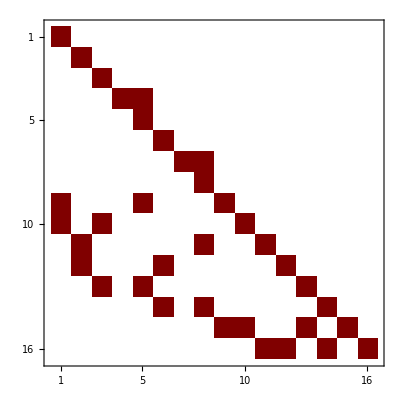

```mathematica
AmatrixNeed=Amatrix[[need,need]];
%//MatrixPlot
```

```mathematica
basisNeed=basis[[need]]
```

{⟨1,3,5,6⟩,⟨2,4,5,6⟩,⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨3,5,7,9⟩,⟨4,5,7,9⟩,⟨1,3,7,9⟩,⟨2,4,7,9⟩}

#### level 0

```mathematica
dRep=Thread[(d/@basisNeed)->Coefficient[AmatrixNeed,e].basisNeed];
```

```mathematica
l0={Log[X1+Y],Log[X2+Y],Log[Y]};(*old letters*)
```

```mathematica
Basis={psi};
```

```mathematica
BasisCount={1};
```

#### level 1

all letters appeared until level 1:

```mathematica
d1=psi/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l1=Cases[%,_Log,Infinity]//Union;
Complement[l1,l0]
```

{Log[X1-Y],Log[X2-Y]}

only add the basis for new letters:

```mathematica
lv2=Coefficient[d1,#]&/@Complement[l1,l0]
%//Length
```

{⟨1,3,5,6⟩,-⟨2,4,5,6⟩}

2

```mathematica
Basis=Join[Basis,lv2];
```

then add the basis for old letters if linearly-independent:

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basisNeed;
sol=Solve[eqn==0,Cases[eqn,_c,Infinity]//Union](*//First*);
Return[If[sol=!={},True,False]]]
```

```mathematica
lv2Old=Coefficient[d1,#]&/@l0//Flatten
```

{-⟨2,4,5,6⟩,⟨1,3,5,6⟩,0}

```mathematica
Do[If[!CheckDependent[lv2Old,i,Basis],Basis=Join[Basis,{lv2Old[[i]]}];],{i,Length[lv2Old]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

```mathematica
Basis//Length
```

3

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,2}

#### level 2

```mathematica
d2=Basis[[(BasisCount[[;;-2]]//Total)+1;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l2=Cases[%,_Log,Infinity]//Union;
Complement[l2,l1]
```

{}

```mathematica
Coefficient[d2,#]&/@Complement[l2,l1];(*new letters*)
(Sort[{#,-#}]&/@Flatten[%])//Union ;(*this seems to be a key step: from 5x4 to 4*)
%//MatrixForm
lv3=%[[All;;,1]]//DeleteCases[0]
```

{}

{}

```mathematica
Do[If[! CheckDependent[lv3, i, Basis], Basis = Join[Basis, {lv3[[i]]}];], {i, Length[lv3]}];
Basis//Length
```

3

```mathematica
lv3Old = Coefficient[d2, #] & /@Join[ l0,l1] // Flatten//DeleteCases[0];
```

```mathematica
lv3Old//Length
```

6

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,vars,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basisNeed;
vars=Union@Cases[eqn,_c,Infinity];
sol=Quiet@Solve[Thread[eqn==0],vars];
sol=!={}]
```

```mathematica
Table[CheckDependent[lv3Old, i, Basis],{i,1,Length[lv3Old]}]
```

{True,True,True,True,True,True}

```mathematica
Do[If[! CheckDependent[lv3Old, i, Basis], Basis = Join[Basis, {lv3Old[[i]]}];], {i, Length[lv3Old]}]
```

```mathematica
Basis//Length
```

3

```mathematica
Position[lv3Old,#]&/@Basis[[{8}]]
```

Part::partw: Part {8} of {⟨1,3,5,6⟩-⟨2,4,5,6⟩,⟨1,3,5,6⟩,-⟨2,4,5,6⟩} does not exist.

{}

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,2,0}

#### close at level 3

```mathematica
d3 = Basis[[(BasisCount[[;; -2]] // Total) + 1 ;;]] /. AngleBracket[a___] -> d[AngleBracket[a]] /. dRep;
l3 = Cases[%, _Log, Infinity] // Union;
Complement[l3, l2]
```

{}

```mathematica
lv4Old = Coefficient[d3, #] & /@ Join[ l0, l1, l2] // Flatten // DeleteCases[0];
```

```mathematica
lv4Old // Length
```

0

```mathematica
Do[If[! CheckDependent[lv4Old, i, Basis], Basis = Join[Basis, {lv4Old[[i]]}];], {i, Length[lv4Old]}]
```

```mathematica
Basis // Length
```

3

#### summary: all physical basis

```mathematica
letters={l0,l1,l2}//Flatten//Union
%//Length
```

{Log[X1-Y],Log[X2-Y],Log[Y],Log[X1+Y],Log[X2+Y]}

5

8 = 1 + (2+1) + (3+1)
7 = 2 + 2 + 3

```mathematica
Basis//MatrixForm
Basis//Length
```

(⟨1,3,5,6⟩-⟨2,4,5,6⟩
⟨1,3,5,6⟩
-⟨2,4,5,6⟩)

3

see how this 6d subspace is embedded in the previous 50d space:

```mathematica
BasisIndex=Basis/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])];
%//MatrixForm
```

(φ_1-φ_2
φ_1
-φ_2)

### Impose symmetry in the basisNeed:

thanks to FRW, we got 2 more basis. Hopefully, this will prevent the X1+X2 from vanishing

```mathematica
basisNeed
toBracket=Thread[(Subscript[φ,#]&/@Range[%//Length])->%]
```

{⟨1,3,5,6⟩,⟨2,4,5,6⟩,⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨3,5,7,9⟩,⟨4,5,7,9⟩,⟨1,3,7,9⟩,⟨2,4,7,9⟩}

{φ_1→⟨1,3,5,6⟩,φ_2→⟨2,4,5,6⟩,φ_3→⟨3,5,6,7⟩,φ_4→⟨3,5,6,8⟩,φ_5→⟨3,5,6,9⟩,φ_6→⟨4,5,6,7⟩,φ_7→⟨4,5,6,8⟩,φ_8→⟨4,5,6,9⟩,φ_9→⟨1,3,5,9⟩,φ_10→⟨1,3,6,7⟩,φ_11→⟨2,4,5,9⟩,φ_12→⟨2,4,6,7⟩,φ_13→⟨3,5,7,9⟩,φ_14→⟨4,5,7,9⟩,φ_15→⟨1,3,7,9⟩,φ_16→⟨2,4,7,9⟩}

```mathematica
symForBasis={⟨4,5,7,9⟩->-⟨3,5,7,9⟩,⟨3,5,6,7⟩->⟨4,5,6,9⟩,⟨4,5,6,7⟩->⟨3,5,6,9⟩,⟨4,5,6,8⟩->-⟨3,5,6,8⟩-⟨3,5,6,9⟩-⟨4,5,6,9⟩}/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])]
```

{φ_14→-φ_13,φ_3→φ_8,φ_6→φ_5,φ_7→-φ_4-φ_5-φ_8}

```mathematica
BasisSym=BasisIndex/.symForBasis//Simplify;
%//MatrixForm
```

(φ_1-φ_2
2 φ_1-φ_2+φ_4-φ_5-φ_10-φ_12
φ_1-2 φ_2-φ_4+φ_5-φ_9-φ_11
φ_1-2 φ_2+φ_4+φ_5+2 φ_8+φ_10+φ_12
2 (2 φ_4+φ_5+φ_8+2 φ_13)
-2 (φ_4+φ_5+4 φ_8-2 φ_13)
2 (2 φ_4+φ_5+φ_8+2 φ_13)
φ_1-4 φ_2+2 φ_4+2 φ_5+2 φ_8-φ_9+φ_10-2 φ_11+2 φ_12+2 φ_13+φ_15-φ_16)

```mathematica
Table[Coefficient[BasisSym[[i]],Subscript[φ,j]],{i,1,8},{j,1,16}]
```

{{1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,-1,0,1,-1,0,0,0,0,-1,0,-1,0,0,0,0},{1,-2,0,-1,1,0,0,0,-1,0,-1,0,0,0,0,0},{1,-2,0,1,1,0,0,2,0,1,0,1,0,0,0,0},{0,0,0,4,2,0,0,2,0,0,0,0,4,0,0,0},{0,0,0,-2,-2,0,0,-8,0,0,0,0,4,0,0,0},{0,0,0,4,2,0,0,2,0,0,0,0,4,0,0,0},{1,-4,0,2,2,0,0,2,-1,1,-2,2,2,0,1,-1}}

```mathematica
%//MatrixRank
```

7

only remove one basis

### reduction history version2: start with 16 basis

#### level 0

```mathematica
dRep=Thread[(d/@basisNeed)->AmatrixNeed.basisNeed];
```

```mathematica
l0={Log[X1+Y],Log[X2+Y]};(*old letters*)
```

```mathematica
Basis={psi};
```

```mathematica
BasisCount={1};
```

#### level 1

all letters appeared until level 1:

```mathematica
d1=psi/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l1=Cases[%,_Log,Infinity]//Union;
Complement[l1,l0]
```

{}

only add the basis for new letters:

```mathematica
lv2=Coefficient[d1,#]&/@Complement[l1,l0]
%//Length
```

{}

0

```mathematica
Basis=Join[Basis,Coefficient[lv2,e]];
```

then add the basis for old letters if linearly-independent:

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basis;
sol=Solve[eqn==0,Cases[eqn,_c,Infinity]//Union](*//First*);
Return[If[sol=!={},True,False]]]
```

```mathematica
lv2Old=Coefficient[d1,#]&/@l0//Flatten
lv2Old=Coefficient[lv2Old,e];
```

{0,0}

```mathematica
Do[If[!CheckDependent[lv2Old,i,Basis],Basis=Join[Basis,{lv2Old[[i]]}];],{i,Length[lv2Old]}]
```

```mathematica
Basis//Length
```

1

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,0}

#### level 2

```mathematica
d2=Basis[[(BasisCount[[;;-2]]//Total)+1;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l2=Cases[%,_Log,Infinity]//Union;
Complement[l2,l1]
```

{}

```mathematica
Coefficient[d2,#]&/@Complement[l2,l1];(*new letters*)
(Sort[{#,-#}]&/@Flatten[%])//Union ;(*this seems to be a key step: from 5x4 to 4*)
%//MatrixForm
lv3=%[[All;;,1]]//DeleteCases[0]
```

{}

{}

```mathematica
Basis=Join[Basis,Coefficient[lv3,e]];
Basis//Length
```

1

```mathematica
Basis
```

{⟨1,3,5,6⟩-⟨2,4,5,6⟩}

```mathematica
(*AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]*)
```

```mathematica
lv3Old = Coefficient[d2, #] & /@Join[ l0,l1] // Flatten//DeleteCases[0]
```

{}

note that there is twist g here.

```mathematica
Do[If[! CheckDependent[lv3Old, i, Basis], Basis = Join[Basis, {lv3Old[[i]]}];], {i, Length[lv3Old]}]
```

#### close at level 3

```mathematica
d3=Basis[[(BasisCount[[;;-2]]//Total)+1;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l3=Cases[%,_Log,Infinity]//Union;
Complement[l3,l2]
```

{}

#### summary: all physical basis

```mathematica
letters={l0,l1,l2}//Flatten//Union
%//Length
```

{Log[X1+Y],Log[X2+Y]}

2

6 = 1 + (2+1) + 1
7 = 2 + 2 + 3

```mathematica
Basis//MatrixForm
Basis//Length
```

(⟨1,3,5,6⟩-⟨2,4,5,6⟩)

1

see how this 6d subspace is embedded in the previous 50d space:

```mathematica
Basis/.Thread[basis->(Subscript[φ,#]&/@Range[basis//Length])]//MatrixForm
```

(φ_13-φ_29)

### reduction history version

#### level 0

```mathematica
dRep=Thread[(d/@basis)->Amatrix.basis];
```

```mathematica
l0={Log[X1+Y],Log[X2+Y]};(*old letters*)
```

```mathematica
Basis={psi};
```

```mathematica
BasisCount={1};
```

#### level 1

all letters appeared until level 1:

```mathematica
d1=psi/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l1=Cases[%,_Log,Infinity]//Union;
Complement[l1,l0]
```

{Log[X1-Y],Log[X2-Y]}

only add the basis for new letters:

```mathematica
lv2=Coefficient[d1,#]&/@Complement[l1,l0]
%//Length
```

{-e ⟨1,3,6,7⟩-e ⟨2,4,5,6⟩-e ⟨2,4,6,7⟩+e ⟨3,5,6,8⟩-e ⟨4,5,6,7⟩,e ⟨1,3,5,6⟩-e ⟨1,3,5,9⟩-e ⟨2,4,5,9⟩+e ⟨3,5,6,9⟩+e ⟨4,5,6,7⟩+e ⟨4,5,6,8⟩+e ⟨4,5,6,9⟩}

2

```mathematica
Basis=Join[Basis,Coefficient[lv2,e]];
```

then add the basis for old letters if linearly-independent:

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basis;
sol=Solve[eqn==0,Cases[eqn,_c,Infinity]//Union](*//First*);
Return[If[sol=!={},True,False]]]
```

```mathematica
lv2Old=Coefficient[d1,#]&/@l0//Flatten
lv2Old=Coefficient[lv2Old,e];
```

{e ⟨1,3,5,6⟩+e ⟨1,3,6,7⟩+e ⟨2,4,6,7⟩+e ⟨3,5,6,7⟩-e ⟨4,5,6,8⟩,e ⟨1,3,5,9⟩-e ⟨2,4,5,6⟩+e ⟨2,4,5,9⟩-e ⟨3,5,6,7⟩-e ⟨3,5,6,8⟩-e ⟨3,5,6,9⟩-e ⟨4,5,6,9⟩}

```mathematica
Do[If[!CheckDependent[lv2Old,i,Basis],Basis=Join[Basis,{lv2Old[[i]]}];],{i,Length[lv2Old]}]
```

```mathematica
Basis//Length
```

4

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,3}

#### level 2

```mathematica
d2=Basis[[(BasisCount[[;;-2]]//Total)+1;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l2=Cases[%,_Log,Infinity]//Union;
Complement[l2,l1]
```

{Log[X1+X2],Log[X1+X2-2 Y],Log[X1+X2+2 Y]}

```mathematica
Coefficient[d2,#]&/@Complement[l2,l1];(*new letters*)
(Sort[{#,-#}]&/@Flatten[%])//Union ;(*this seems to be a key step: from 5x4 to 4*)
%//MatrixForm
lv3=%[[All;;,1]]//DeleteCases[0]
```

(0 | 0
e ⟨3,5,6,7⟩-e ⟨3,5,6,9⟩+2 e ⟨3,5,7,9⟩-e ⟨4,5,6,7⟩+e ⟨4,5,6,9⟩-2 e ⟨4,5,7,9⟩ | -e ⟨3,5,6,7⟩+e ⟨3,5,6,9⟩-2 e ⟨3,5,7,9⟩+e ⟨4,5,6,7⟩-e ⟨4,5,6,9⟩+2 e ⟨4,5,7,9⟩
-e ⟨3,5,6,8⟩-e ⟨3,5,6,9⟩+2 e ⟨3,5,7,9⟩+e ⟨4,5,6,8⟩+e ⟨4,5,6,9⟩-2 e ⟨4,5,7,9⟩ | e ⟨3,5,6,8⟩+e ⟨3,5,6,9⟩-2 e ⟨3,5,7,9⟩-e ⟨4,5,6,8⟩-e ⟨4,5,6,9⟩+2 e ⟨4,5,7,9⟩)

{e ⟨3,5,6,7⟩-e ⟨3,5,6,9⟩+2 e ⟨3,5,7,9⟩-e ⟨4,5,6,7⟩+e ⟨4,5,6,9⟩-2 e ⟨4,5,7,9⟩,-e ⟨3,5,6,8⟩-e ⟨3,5,6,9⟩+2 e ⟨3,5,7,9⟩+e ⟨4,5,6,8⟩+e ⟨4,5,6,9⟩-2 e ⟨4,5,7,9⟩}

```mathematica
Basis=Join[Basis,Coefficient[lv3,e]];
Basis//Length
```

6

```mathematica
Basis
```

{⟨1,3,5,6⟩-⟨2,4,5,6⟩,-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨4,5,6,7⟩,⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩+⟨3,5,6,9⟩+⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩,⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+⟨3,5,6,7⟩-⟨4,5,6,8⟩,⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩,-⟨3,5,6,8⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩}

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,3,2}

lv3Old = Coefficient[d2, #] & /@ l1 // Flatten

{0, -e ⟨1, 3, 6, 7⟩ - e ⟨1, 3, 7, 9⟩ + e ⟨2, 4, 5, 9⟩ - e ⟨2, 4, 7, 9⟩ + e ⟨3, 5, 6, 8⟩ + e ⟨3, 5, 6, 9⟩ - e ⟨3, 5, 7, 9⟩ - e ⟨4, 5, 7, 9⟩, -e ⟨1, 3, 6, 7⟩ + e ⟨2, 4, 5, 6⟩ + e ⟨2, 4, 6, 7⟩ + e ⟨3, 5, 6, 8⟩ + e ⟨4, 5, 6, 7⟩, -e ⟨1, 3, 6, 7⟩ - e ⟨1, 3, 7, 9⟩ + e ⟨2, 4, 5, 9⟩ - e ⟨2, 4, 7, 9⟩ + e ⟨3, 5, 7, 9⟩ + e ⟨4, 5, 6, 7⟩ - g ⟨4, 5, 6, 7⟩ - e ⟨4, 5, 6, 8⟩ - e ⟨4, 5, 6, 9⟩ + e ⟨4, 5, 7, 9⟩, -e ⟨1, 3, 5, 6⟩ + g ⟨1, 3, 5, 6⟩ - e ⟨3, 5, 6, 9⟩ + g ⟨3, 5, 6, 9⟩, e ⟨1, 3, 5, 6⟩ - e ⟨1, 3, 5, 9⟩ + e ⟨1, 3, 6, 7⟩ + e ⟨1, 3, 7, 9⟩ + e ⟨2, 4, 7, 9⟩ + e ⟨3, 5, 6, 9⟩ - e ⟨3, 5, 7, 9⟩ - 2 e ⟨4, 5, 6, 7⟩ + g ⟨4, 5, 6, 7⟩ - e ⟨4, 5, 7, 9⟩, 2 e ⟨1, 3, 5, 6⟩ - g ⟨1, 3, 5, 6⟩ + 2 e ⟨1, 3, 6, 7⟩ - g ⟨1, 3, 6, 7⟩ - e ⟨2, 4, 6, 7⟩ + 2 e ⟨3, 5, 6, 7⟩ - g ⟨3, 5, 6, 7⟩ + e ⟨4, 5, 6, 8⟩, e ⟨1, 3, 5, 6⟩ - e ⟨1, 3, 5, 9⟩ + e ⟨1, 3, 6, 7⟩ + e ⟨1, 3, 7, 9⟩ + e ⟨2, 4, 7, 9⟩ + e ⟨3, 5, 6, 7⟩ + e ⟨3, 5, 7, 9⟩ - 2 e ⟨4, 5, 6, 9⟩ + g ⟨4, 5, 6, 9⟩ + e ⟨4, 5, 7, 9⟩, -e ⟨1, 3, 5, 6⟩ + g ⟨1, 3, 5, 6⟩ - e ⟨1, 3, 6, 7⟩ + g ⟨1, 3, 6, 7⟩ - e ⟨3, 5, 6, 7⟩ + g ⟨3, 5, 6, 7⟩, e ⟨1, 3, 7, 9⟩ + e ⟨2, 4, 5, 6⟩ - e ⟨2, 4, 5, 9⟩ + e ⟨2, 4, 6, 7⟩ + e ⟨2, 4, 7, 9⟩ - e ⟨3, 5, 6, 7⟩ - e ⟨3, 5, 7, 9⟩ + e ⟨4, 5, 6, 9⟩ - e ⟨4, 5, 7, 9⟩, e ⟨1, 3, 5, 9⟩ + e ⟨2, 4, 5, 6⟩ - 2 e ⟨2, 4, 5, 9⟩ + g ⟨2, 4, 5, 9⟩ - e ⟨3, 5, 6, 7⟩ - e ⟨3, 5, 6, 8⟩ - e ⟨3, 5, 6, 9⟩ + e ⟨4, 5, 6, 9⟩, e ⟨1, 3, 5, 9⟩ - e ⟨1, 3, 7, 9⟩ - e ⟨2, 4, 6, 7⟩ - e ⟨2, 4, 7, 9⟩ - e ⟨3, 5, 6, 8⟩ - e ⟨3, 5, 6, 9⟩ + e ⟨3, 5, 7, 9⟩ + e ⟨4, 5, 7, 9⟩}

note that there is twist g here.

lv3Old = Coefficient[lv3Old /. g -> 0, e] // DeleteCases[0]

{-⟨1, 3, 6, 7⟩ - ⟨1, 3, 7, 9⟩ + ⟨2, 4, 5, 9⟩ - ⟨2, 4, 7, 9⟩ + ⟨3, 5, 6, 8⟩ + ⟨3, 5, 6, 9⟩ - ⟨3, 5, 7, 9⟩ - ⟨4, 5, 7, 9⟩, -⟨1, 3, 6, 7⟩ + ⟨2, 4, 5, 6⟩ + ⟨2, 4, 6, 7⟩ + ⟨3, 5, 6, 8⟩ + ⟨4, 5, 6, 7⟩, -⟨1, 3, 6, 7⟩ - ⟨1, 3, 7, 9⟩ + ⟨2, 4, 5, 9⟩ - ⟨2, 4, 7, 9⟩ + ⟨3, 5, 7, 9⟩ + ⟨4, 5, 6, 7⟩ - ⟨4, 5, 6, 8⟩ - ⟨4, 5, 6, 9⟩ + ⟨4, 5, 7, 9⟩, -⟨1, 3, 5, 6⟩ - ⟨3, 5, 6, 9⟩, ⟨1, 3, 5, 6⟩ - ⟨1, 3, 5, 9⟩ + ⟨1, 3, 6, 7⟩ + ⟨1, 3, 7, 9⟩ + ⟨2, 4, 7, 9⟩ + ⟨3, 5, 6, 9⟩ - ⟨3, 5, 7, 9⟩ - 2 ⟨4, 5, 6, 7⟩ - ⟨4, 5, 7, 9⟩, 2 ⟨1, 3, 5, 6⟩ + 2 ⟨1, 3, 6, 7⟩ - ⟨2, 4, 6, 7⟩ + 2 ⟨3, 5, 6, 7⟩ + ⟨4, 5, 6, 8⟩, ⟨1, 3, 5, 6⟩ - ⟨1, 3, 5, 9⟩ + ⟨1, 3, 6, 7⟩ + ⟨1, 3, 7, 9⟩ + ⟨2, 4, 7, 9⟩ + ⟨3, 5, 6, 7⟩ + ⟨3, 5, 7, 9⟩ - 2 ⟨4, 5, 6, 9⟩ + ⟨4, 5, 7, 9⟩, -⟨1, 3, 5, 6⟩ - ⟨1, 3, 6, 7⟩ - ⟨3, 5, 6, 7⟩, ⟨1, 3, 7, 9⟩ + ⟨2, 4, 5, 6⟩ - ⟨2, 4, 5, 9⟩ + ⟨2, 4, 6, 7⟩ + ⟨2, 4, 7, 9⟩ - ⟨3, 5, 6, 7⟩ - ⟨3, 5, 7, 9⟩ + ⟨4, 5, 6, 9⟩ - ⟨4, 5, 7, 9⟩, ⟨1, 3, 5, 9⟩ + ⟨2, 4, 5, 6⟩ - 2 ⟨2, 4, 5, 9⟩ - ⟨3, 5, 6, 7⟩ - ⟨3, 5, 6, 8⟩ - ⟨3, 5, 6, 9⟩ + ⟨4, 5, 6, 9⟩, ⟨1, 3, 5, 9⟩ - ⟨1, 3, 7, 9⟩ - ⟨2, 4, 6, 7⟩ - ⟨2, 4, 7, 9⟩ - ⟨3, 5, 6, 8⟩ - ⟨3, 5, 6, 9⟩ + ⟨3, 5, 7, 9⟩ + ⟨4, 5, 7, 9⟩}

Do[If[! CheckDependent[lv3Old, i, Basis], Basis = Join[Basis, {lv3Old[[i]]}];], {i, Length[lv3Old]}]

Solve::svars: "Equations may not give solutions for all "solve" variables."

Solve::svars: "Equations may not give solutions for all "solve" variables."

Solve::svars: "Equations may not give solutions for all "solve" variables."

General::stop: "Further output of Solve::svars will be suppressed during this calculation."

#### close at level 3

```mathematica
d3=Basis[[(BasisCount[[;;-2]]//Total)+1;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l3=Cases[%,_Log,Infinity]//Union;
Complement[l3,l2]
```

{}

#### summary: all physical basis

```mathematica
letters={l0,l1,l2}//Flatten//Union
%//Length
```

{Log[X1+X2],Log[X1+X2-2 Y],Log[X1-Y],Log[X2-Y],Log[X1+Y],Log[X2+Y],Log[X1+X2+2 Y]}

7

6 = 1 + (2+1) + 1
7 = 2 + 2 + 3

```mathematica
Basis//MatrixForm
Basis//Length
```

(⟨1,3,5,6⟩-⟨2,4,5,6⟩
-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨4,5,6,7⟩
⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩+⟨3,5,6,9⟩+⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩
⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+⟨3,5,6,7⟩-⟨4,5,6,8⟩
⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩
-⟨3,5,6,8⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩)

6

see how this 6d subspace is embedded in the previous 50d space:

```mathematica
Basis/.Thread[basis->(Subscript[φ,#]&/@Range[basis//Length])]//MatrixForm
```

(φ_13-φ_29
φ_2-φ_5-φ_15-φ_29-φ_31
φ_3+φ_5+φ_6+φ_7+φ_13-φ_14-φ_30
φ_1-φ_6+φ_13+φ_15+φ_31
φ_1-φ_3+2 φ_4-φ_5+φ_7-2 φ_8
-φ_2-φ_3+2 φ_4+φ_6+φ_7-2 φ_8)

### A matrix (associated to physical basis)

#### A-matrix

```mathematica
Umatrix=Table[Coefficient[Basis[[i]],basisNeed[[j]]],{i,1,Length[Basis]},{j,1,Length[basisNeed]}];
Uinv=Simplify[PseudoInverse[Umatrix]];
```

```mathematica
Amatrix8=Umatrix.AmatrixNeed.Uinv//Simplify;
%//MatrixForm
```

(-4 e Log[Y]+6 e Log[X2+Y] | e (Log[X1-Y]-Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (Log[X1+Y]-Log[X2+Y]) | 0 | 0 | 0 | 0
18 e (-Log[X1+X2-2 Y]+Log[X2+Y]) | e (6 Log[X1+X2-2 Y]+2 Log[X1-Y]-3 (Log[Y]+Log[X2+Y])) | 3 e (Log[X2-Y]-Log[X2+Y]) | e (6 Log[X1+X2-2 Y]-Log[Y]+Log[X1+Y]-6 Log[X2+Y]) | e (-Log[X1+X2-2 Y]+Log[X2-Y]) | e (Log[X1+X2-2 Y]-Log[X2+Y]) | e (Log[X1+X2]-Log[X1+X2-2 Y]) | e (-Log[X2-Y]+Log[X2+Y])
6 e (3 Log[X1+X2-2 Y]-3 Log[X1-Y]-Log[Y]+Log[X2+Y]) | e (-6 Log[X1+X2-2 Y]+6 Log[X1-Y]+Log[Y]-Log[X2+Y]) | e (3 Log[X1-Y]+2 Log[X2-Y]-2 Log[Y]-Log[X2+Y]) | e (-6 Log[X1+X2-2 Y]+6 Log[X1-Y]+Log[Y]-Log[X2+Y]) | e (-Log[X1+X2]+Log[X1+X2-2 Y]) | e (-Log[X1+X2-2 Y]+Log[X1-Y]) | e (Log[X1+X2-2 Y]-Log[X1-Y]) | e (-Log[X1-Y]+Log[X1+Y])
0 | e (Log[X1-Y]-Log[Y]) | 0 | e (-3 Log[Y]+2 Log[X1+Y]+3 Log[X2+Y]) | e (Log[X1+X2]-Log[X2-Y]) | e (Log[X2+Y]-Log[X1+X2+2 Y]) | 0 | e (Log[X2-Y]-Log[X2+Y])
18 e (-Log[X1+X2-2 Y]+Log[Y]) | 6 e (Log[X1+X2-2 Y]-Log[Y]) | 0 | 6 e (Log[X1+X2-2 Y]-Log[Y]) | e (4 Log[X1+X2]-Log[X1+X2-2 Y]-Log[Y]) | e (Log[X1+X2-2 Y]-Log[X1+X2+2 Y]) | e (-Log[X1+X2-2 Y]+Log[Y]) | 0
0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[Y]) | -2 e (Log[Y]-2 Log[X1+X2+2 Y]) | e (-Log[X1+X2]+Log[Y]) | 0
18 e (-Log[X1+X2-2 Y]+Log[Y]) | 6 e (Log[X1+X2-2 Y]-Log[Y]) | 0 | 6 e (Log[X1+X2-2 Y]-Log[Y]) | e (-Log[X1+X2-2 Y]+Log[Y]) | e (Log[X1+X2-2 Y]-Log[X1+X2+2 Y]) | e (4 Log[X1+X2]-Log[X1+X2-2 Y]-Log[Y]) | 0
18 e (-Log[X1-Y]+Log[Y]) | 6 e (Log[X1-Y]-Log[Y]) | 3 e (Log[X1-Y]-Log[Y]) | 3 e (2 Log[X1-Y]-3 Log[Y]+Log[X2+Y]) | 2 e (Log[X1+X2]-Log[X2-Y]) | e (Log[X1-Y]-Log[Y]+Log[X2+Y]-Log[X1+X2+2 Y]) | e (-Log[X1-Y]+Log[Y]) | -e (Log[X1-Y]-2 Log[X2-Y]-2 Log[X1+Y]+Log[X2+Y]))

```mathematica
Amatrix8//MatrixPlot
```

-Graphics-

the matrix is not upper triangular...
we need to orthogonalize the new basis appearing at each level.

#### check flatness

```mathematica
kin
```

{X1,X2,Y}

```mathematica
Amatrix//Dimensions
```

{50,50}

```mathematica
Amatrix[[1,1]]
```

e (Log[X1+X2]+4 Log[X1+X2+2 Y])

```mathematica
Table[A0[[i]].A0[[j]]-A0[[j]].A0[[i]]//Simplify,{i,1,Length[kin]},{j,i+1,Length[kin]}]//Flatten//DeleteCases[0]//Simplify
```

{}

```mathematica
Amatrix;
Table[D[%,kin[[i]]].D[%,kin[[j]]]-D[%,kin[[j]]].D[%,kin[[i]]]//Simplify,{i,1,Length[kin]},{j,i+1,Length[kin]}]//Flatten//DeleteCases[0]//Simplify
```

{}

```mathematica
Amatrix//MatrixForm
```

(2 e Log[X1+X2+2 Y]+2 g Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 e Log[X1+X2]+2 g Log[X1+X2] | e (2 Log[X1+X2]-2 Log[X1+X2-2 Y])+g (2 Log[X1+X2]-2 Log[X1+X2-2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 e Log[X1+X2-2 Y]+2 g Log[X1+X2-2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+X2]-Log[Y])+g (Log[X1+X2]-Log[Y]) | 0 | e (-Log[X1+X2]+Log[Y])+g (-Log[X1+X2]+Log[Y]) | 2 e Log[X1+X2]+2 g Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 e Log[X1+X2-2 Y]+2 g Log[X1+X2-2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 e Log[X1+X2]+2 g Log[X1+X2] | e (2 Log[X1+X2]-2 Log[X1+X2+2 Y])+g (2 Log[X1+X2]-2 Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 e Log[X1+X2+2 Y]+2 g Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[Y])+g (Log[X1+X2]-Log[Y]) | 0 | e (-Log[X1+X2]+Log[Y])+g (-Log[X1+X2]+Log[Y]) | 2 e Log[X1+X2]+2 g Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]+Log[X2-Y])+g (Log[X1-Y]+Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X2+Y])+g (Log[Y]-Log[X2+Y]) | e (Log[X1-Y]+Log[X2+Y])+g (Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y])+g (-Log[Y]+Log[X1+Y]) | 0 | e (Log[X2-Y]+Log[X1+Y])+g (Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y])+g (Log[Y]-Log[X1+Y]) | e (-Log[Y]+Log[X2+Y])+g (-Log[Y]+Log[X2+Y]) | e (Log[X1+Y]+Log[X2+Y])+g (Log[X1+Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]+Log[X2+Y])+g (Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (Log[X1-Y]-Log[X2-Y])+g (Log[X1-Y]-Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-Y]+Log[Y])+g (-Log[X2-Y]+Log[Y]) | e (Log[X1-Y]+Log[X2-Y])+g (Log[X1-Y]+Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+Y]-Log[X2+Y])+g (Log[X1+Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y])+g (-Log[Y]+Log[X1+Y]) | 0 | e (Log[X1+Y]+Log[X2+Y])+g (Log[X1+Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e (-Log[X2-Y]+Log[X1+Y])+g (-Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y])+g (Log[Y]-Log[X1+Y]) | e (Log[X2-Y]-Log[Y])+g (Log[X2-Y]-Log[Y]) | e (Log[X2-Y]+Log[X1+Y])+g (Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 e Log[2 X1+X2-Y]+2 g Log[2 X1+X2-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[-2 X1-X2-Y])+g (Log[X1-Y]-Log[-2 X1-X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-2 X1-X2-Y]+Log[Y])+g (-Log[-2 X1-X2-Y]+Log[Y]) | e (Log[X1-Y]+Log[-2 X1-X2-Y])+g (Log[X1-Y]+Log[-2 X1-X2-Y]) | 0 | 0 | e (Log[X1-Y]-Log[-2 X1-X2-Y])+g (Log[X1-Y]-Log[-2 X1-X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[X2-3 Y]+Log[X1+Y])+g (-Log[X2-3 Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-3 Y]+Log[X1+Y])+g (-Log[X2-3 Y]+Log[X1+Y]) | 0 | e (Log[X2-3 Y]+Log[X1+Y])+g (Log[X2-3 Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2+Y])+g (Log[X1-Y]-Log[X2+Y]) | e (-Log[X2+Y]+Log[X2+3 Y])+g (-Log[X2+Y]+Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2+Y])+g (Log[X1-Y]-Log[X2+Y]) | e (Log[X2+Y]-Log[X2+3 Y])+g (Log[X2+Y]-Log[X2+3 Y]) | 0 | e (Log[X1-Y]+Log[X2+Y])+g (Log[X1-Y]+Log[X2+Y]) | e (Log[X2+Y]-Log[X2+3 Y])+g (Log[X2+Y]-Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (Log[-2 X1-X2-Y]-Log[X2+3 Y])+g (Log[-2 X1-X2-Y]-Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[-2 X1-X2-Y]-Log[Y])+g (Log[-2 X1-X2-Y]-Log[Y]) | e (-Log[-2 X1-X2-Y]+Log[X2+3 Y])+g (-Log[-2 X1-X2-Y]+Log[X2+3 Y]) | 0 | 0 | e (Log[-2 X1-X2-Y]+Log[X2+3 Y])+g (Log[-2 X1-X2-Y]+Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-Y]+Log[X1+Y])+g (-Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y])+g (Log[Y]-Log[X1+Y]) | e (Log[X2-Y]-Log[Y])+g (Log[X2-Y]-Log[Y]) | 0 | e (-Log[X2-Y]+Log[Y])+g (-Log[X2-Y]+Log[Y]) | e (Log[X2-Y]+Log[X1+Y])+g (Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]+Log[X1+2 X2-Y])+g (Log[X2-Y]+Log[X1+2 X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X1+2 X2+Y]+Log[X1+3 Y])+g (-Log[X1+2 X2+Y]+Log[X1+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+2 X2+Y]+Log[X1+3 Y])+g (-Log[X1+2 X2+Y]+Log[X1+3 Y]) | e (Log[X1+2 X2+Y]+Log[X1+3 Y])+g (Log[X1+2 X2+Y]+Log[X1+3 Y]) | 0 | 0 | e (-Log[X1+2 X2+Y]+Log[X1+3 Y])+g (-Log[X1+2 X2+Y]+Log[X1+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | e (-Log[X1+2 X2-Y]+Log[X1+Y])+g (-Log[X1+2 X2-Y]+Log[X1+Y]) | e (-Log[X1-3 Y]+Log[X1+Y])+g (-Log[X1-3 Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+2 X2-Y]-Log[X1+Y])+g (Log[X1+2 X2-Y]-Log[X1+Y]) | 0 | e (Log[X1+2 X2-Y]+Log[X1+Y])+g (Log[X1+2 X2-Y]+Log[X1+Y]) | e (-Log[X1-3 Y]+Log[X1+Y])+g (-Log[X1-3 Y]+Log[X1+Y]) | e (Log[X1+2 X2-Y]-Log[X1+Y])+g (Log[X1+2 X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (Log[X1-3 Y]-Log[X2+Y])+g (Log[X1-3 Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X2+Y])+g (Log[Y]-Log[X2+Y]) | 0 | 0 | e (Log[X1-3 Y]+Log[X2+Y])+g (Log[X1-3 Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X2-Y]+Log[X1+2 X2+Y])+g (-Log[X2-Y]+Log[X1+2 X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+2 X2+Y])+g (-Log[Y]+Log[X1+2 X2+Y]) | e (Log[X2-Y]-Log[X1+2 X2+Y])+g (Log[X2-Y]-Log[X1+2 X2+Y]) | 0 | 0 | e (Log[X2-Y]+Log[X1+2 X2+Y])+g (Log[X2-Y]+Log[X1+2 X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e (Log[X1-Y]-Log[X2+Y])+g (Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y])+g (Log[X1-Y]-Log[Y]) | 0 | e (-Log[X1-Y]+Log[Y])+g (-Log[X1-Y]+Log[Y]) | e (-Log[Y]+Log[X2+Y])+g (-Log[Y]+Log[X2+Y]) | e (Log[X1-Y]+Log[X2+Y])+g (Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]+Log[X1+Y])+g (Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+Y]-Log[X2+Y])+g (Log[X1+Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X2+Y])+g (Log[Y]-Log[X2+Y]) | e (Log[X1+Y]+Log[X2+Y])+g (Log[X1+Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2-Y])+g (Log[X1-Y]-Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y])+g (Log[X1-Y]-Log[Y]) | 0 | e (Log[X1-Y]+Log[X2-Y])+g (Log[X1-Y]+Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2+Y])+g (Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y])+g (-Log[X1-Y]+Log[Y]) | e (-Log[Y]+Log[X2+Y])+g (-Log[Y]+Log[X2+Y]) | e (Log[X1-Y]+Log[X2+Y])+g (Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+X2]-Log[Y])+g (Log[X1+X2]-Log[Y]) | 0 | 0 | 0 | e (-Log[X1+X2]+Log[Y])+g (-Log[X1+X2]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 e Log[X1+X2]+2 g Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | e Log[X1+X2]+g Log[X1+X2] | e Log[Y]+g Log[Y] | 0 | 0 | -e Log[X1+X2]-g Log[X1+X2] | -e Log[Y]-g Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 e Log[X1+X2]+2 g Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (Log[X1+X2]-Log[Y])+g (Log[X1+X2]-Log[Y]) | 0 | 0 | 0 | e (-Log[X1+X2]+Log[Y])+g (-Log[X1+X2]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 e Log[X1+X2]+2 g Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2]-Log[Y])+g (Log[X2]-Log[Y]) | 0 | 0 | 0 | e (-Log[X2]+Log[Y])+g (-Log[X2]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2]-Log[Y])+g (Log[X2]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2]+Log[X1-Y])+g (Log[X2]+Log[X1-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2]+Log[Y])+g (-Log[X2]+Log[Y]) | 0 | 0 | 0 | e (Log[X2]-Log[Y])+g (Log[X2]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y])+g (Log[Y]-Log[X1+Y]) | 0 | 0 | e (-Log[X2]+Log[Y])+g (-Log[X2]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y])+g (Log[Y]-Log[X1+Y]) | e (Log[X2]+Log[X1+Y])+g (Log[X2]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[Y])+g (-Log[X1]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[X2-Y])+g (Log[X1]-Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[Y])+g (-Log[X1]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]+Log[X2-Y])+g (Log[X1]+Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[Y])+g (-Log[X1]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[Y])+g (Log[X1]-Log[Y]) | 0 | 0 | e (-Log[Y]+Log[X2+Y])+g (-Log[Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[Y])+g (-Log[X1]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X2+Y])+g (Log[Y]-Log[X2+Y]) | e (Log[X1]+Log[X2+Y])+g (Log[X1]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X1-Y])+g (Log[X1+X2]-Log[X1-Y]) | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X1-Y])+g (-Log[X1+X2]+Log[X1-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]+Log[X1-Y])+g (Log[X1+X2]+Log[X1-Y]) | e (-Log[X1+X2]+Log[X1-Y])+g (-Log[X1+X2]+Log[X1-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X2+Y])+g (-Log[X1+X2]+Log[X2+Y]) | 0 | 0 | 0 | e (Log[X1+X2]-Log[X2+Y])+g (Log[X1+X2]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X2+Y])+g (-Log[X1+X2]+Log[X2+Y]) | e (Log[X1+X2]+Log[X2+Y])+g (Log[X1+X2]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-Y]+Log[Y])+g (-Log[X2-Y]+Log[Y]) | 0 | 0 | 0 | e (Log[X2-Y]-Log[Y])+g (Log[X2-Y]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-Log[X1+Y])+g (Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y])+g (Log[Y]-Log[X1+Y]) | e (-Log[X2-Y]+Log[Y])+g (-Log[X2-Y]+Log[Y]) | e (Log[X2-Y]+Log[X1+Y])+g (Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 e Log[X2+Y]+2 g Log[X2+Y] | -e Log[Y]-g Log[Y] | e Log[X2+Y]+g Log[X2+Y] | 0 | 0 | e Log[Y]+g Log[Y] | 0 | e Log[X2+Y]+g Log[X2+Y] | e Log[Y]+g Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X2+Y])+g (-Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | -e Log[X1-Y]-g Log[X1-Y] | -e Log[X2+Y]-g Log[X2+Y] | 0 | e (Log[X1-Y]+Log[X2+Y])+g (Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y])+g (Log[Y]-Log[X1+Y]) | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y])+g (-Log[Y]+Log[X1+Y]) | 0 | 0 | e (Log[X2-Y]-Log[Y])+g (Log[X2-Y]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-Log[X1+Y])+g (Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y])+g (Log[Y]-Log[X1+Y]) | e (-Log[X2-Y]+Log[Y])+g (-Log[X2-Y]+Log[Y]) | 0 | 0 | e (Log[X2-Y]+Log[X1+Y])+g (Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X1+Y])+g (Log[X1+X2]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X1+Y])+g (-Log[X1+X2]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]+Log[X1+Y])+g (Log[X1+X2]+Log[X1+Y]) | e (-Log[X1+X2]+Log[X1+Y])+g (-Log[X1+X2]+Log[X1+Y]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X2-Y])+g (-Log[X1+X2]+Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X2-Y])+g (Log[X1+X2]-Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X2-Y])+g (-Log[X1+X2]+Log[X2-Y]) | e (Log[X1+X2]+Log[X2-Y])+g (Log[X1+X2]+Log[X2-Y]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y])+g (-Log[X1-Y]+Log[Y]) | 0 | 0 | e (Log[Y]-Log[X2+Y])+g (Log[Y]-Log[X2+Y]) | 0 | 0 | 0 | e (-Log[Y]+Log[X2+Y])+g (-Log[Y]+Log[X2+Y]) | 0 | e (-Log[X1-Y]+Log[X2+Y])+g (-Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y])+g (-Log[X1-Y]+Log[Y]) | e (Log[Y]-Log[X2+Y])+g (Log[Y]-Log[X2+Y]) | e (Log[X1-Y]+Log[X2+Y])+g (Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 e Log[X2-Y]+2 g Log[X2-Y] | 0 | -e Log[X1+Y]-g Log[X1+Y] | -e Log[Y]-g Log[Y] | e Log[X2-Y]+g Log[X2-Y] | 0 | -2 e Log[X2-Y]-2 g Log[X2-Y] | e Log[Y]+g Log[Y] | -e Log[X2-Y]-g Log[X2-Y] | 0 | 0 | e (Log[X2-Y]-Log[X1+Y])+g (Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X1+Y]-g Log[X1+Y] | -e Log[X2-Y]-g Log[X2-Y] | 0 | e (Log[X2-Y]+Log[X1+Y])+g (Log[X2-Y]+Log[X1+Y]) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y])+g (-Log[X1-Y]+Log[Y]) | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y])+g (Log[X1-Y]-Log[Y]) | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X2+Y])+g (-Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y])+g (-Log[X1-Y]+Log[Y]) | e (Log[Y]-Log[X2+Y])+g (Log[Y]-Log[X2+Y]) | 0 | 0 | e (Log[X1-Y]+Log[X2+Y])+g (Log[X1-Y]+Log[X2+Y]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[Y])+g (-Log[X1]+Log[Y]) | 0 | e (Log[X2]-Log[Y])+g (Log[X2]-Log[Y]) | 0 | e (-Log[X1]+Log[Y])+g (-Log[X1]+Log[Y]) | e (-Log[X2]+Log[Y])+g (-Log[X2]+Log[Y]) | 0 | 0 | 0 | e (Log[X1]-Log[Y])+g (Log[X1]-Log[Y]) | e (Log[X2]-Log[Y])+g (Log[X2]-Log[Y]) | 0 | 0 | 0 | e (Log[X1]+Log[X2])+g (Log[X1]+Log[X2]))

```mathematica
AmatrixNeed//MatrixForm
```

(e (Log[X1-Y]+Log[X2+Y])+g (Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | e (Log[X2-Y]+Log[X1+Y])+g (Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 e Log[X1+X2+2 Y]+2 g Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 e Log[X1+X2]+2 g Log[X1+X2] | e (2 Log[X1+X2]-2 Log[X1+X2-2 Y])+g (2 Log[X1+X2]-2 Log[X1+X2-2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 e Log[X1+X2-2 Y]+2 g Log[X1+X2-2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 e Log[X1+X2-2 Y]+2 g Log[X1+X2-2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 e Log[X1+X2]+2 g Log[X1+X2] | e (2 Log[X1+X2]-2 Log[X1+X2+2 Y])+g (2 Log[X1+X2]-2 Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 e Log[X1+X2+2 Y]+2 g Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X2-Y]+Log[Y])+g (-Log[X2-Y]+Log[Y]) | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2-Y])+g (Log[X1-Y]-Log[X2-Y]) | 0 | 0 | 0 | e (Log[X1-Y]+Log[X2-Y])+g (Log[X1-Y]+Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[Y]+Log[X1+Y])+g (-Log[Y]+Log[X1+Y]) | 0 | e (Log[X1+Y]-Log[X2+Y])+g (Log[X1+Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+Y]+Log[X2+Y])+g (Log[X1+Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0
0 | e (Log[Y]-Log[X2+Y])+g (Log[Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | e (Log[X1+Y]-Log[X2+Y])+g (Log[X1+Y]-Log[X2+Y]) | 0 | 0 | e (Log[X1+Y]+Log[X2+Y])+g (Log[X1+Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0
0 | e (Log[X1-Y]-Log[Y])+g (Log[X1-Y]-Log[Y]) | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2-Y])+g (Log[X1-Y]-Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]+Log[X2-Y])+g (Log[X1-Y]+Log[X2-Y]) | 0 | 0 | 0 | 0
0 | 0 | e (Log[X1+X2]-Log[Y])+g (Log[X1+X2]-Log[Y]) | 0 | e (-Log[X1+X2]+Log[Y])+g (-Log[X1+X2]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 e Log[X1+X2]+2 g Log[X1+X2] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[Y])+g (Log[X1+X2]-Log[Y]) | 0 | e (-Log[X1+X2]+Log[Y])+g (-Log[X1+X2]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 2 e Log[X1+X2]+2 g Log[X1+X2] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y])+g (Log[Y]-Log[X1+Y]) | e (Log[X2-Y]-Log[Y])+g (Log[X2-Y]-Log[Y]) | 0 | 0 | e (-Log[X2-Y]+Log[X1+Y])+g (-Log[X2-Y]+Log[X1+Y]) | 0 | e (Log[X2-Y]+Log[X1+Y])+g (Log[X2-Y]+Log[X1+Y]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y])+g (-Log[X1-Y]+Log[Y]) | e (-Log[Y]+Log[X2+Y])+g (-Log[Y]+Log[X2+Y]) | 0 | e (Log[X1-Y]-Log[X2+Y])+g (Log[X1-Y]-Log[X2+Y]) | 0 | e (Log[X1-Y]+Log[X2+Y])+g (Log[X1-Y]+Log[X2+Y]))

```mathematica
AmatrixNeed;
Table[D[%,kin[[i]]].D[%,kin[[j]]]-D[%,kin[[j]]].D[%,kin[[i]]]//Simplify,{i,1,Length[kin]},{j,i+1,Length[kin]}]//Flatten//DeleteCases[0]//Simplify
```

{}

#### recover A matrix in kinematic flow

here we use Hayden’s basis

```mathematica
basisKinematic={⟨1,2,3⟩-⟨1,2,6⟩-⟨1,3,4⟩+⟨1,3,5⟩+⟨1,3,6⟩-⟨1,4,5⟩-⟨2,3,5⟩+⟨2,4,5⟩-⟨2,4,6⟩+⟨3,4,6⟩,-⟨2,3,5⟩+⟨2,3,7⟩+⟨2,4,5⟩-⟨2,4,6⟩-⟨2,6,7⟩+⟨3,4,6⟩-⟨3,4,7⟩+⟨3,5,7⟩+⟨3,6,7⟩-⟨4,5,7⟩,-⟨1,2,6⟩+⟨1,2,9⟩-⟨1,4,5⟩+⟨1,4,9⟩-⟨1,5,9⟩-⟨1,6,9⟩+⟨2,4,5⟩-⟨2,4,6⟩+⟨2,5,9⟩+⟨4,6,9⟩,⟨1,3,5⟩-⟨1,3,8⟩-⟨1,4,5⟩+⟨1,4,8⟩-⟨3,5,8⟩+⟨4,5,8⟩,-⟨1,3,4⟩+⟨1,3,8⟩-⟨1,4,8⟩+⟨3,4,8⟩,⟨1,3,6⟩-⟨1,3,8⟩+⟨1,6,8⟩+⟨3,4,6⟩-⟨3,4,8⟩-⟨4,6,8⟩,⟨2,4,5⟩-⟨2,4,6⟩+⟨2,5,9⟩-⟨2,6,7⟩-⟨2,7,9⟩-⟨4,5,7⟩+⟨4,6,9⟩-⟨4,7,9⟩+⟨5,7,9⟩+⟨6,7,9⟩,⟨3,5,7⟩-⟨3,5,8⟩+⟨3,7,8⟩-⟨4,5,7⟩+⟨4,5,8⟩-⟨4,7,8⟩,-⟨3,4,7⟩+⟨3,4,8⟩-⟨3,7,8⟩+⟨4,7,8⟩,⟨3,4,6⟩-⟨3,4,8⟩+⟨3,6,7⟩+⟨3,7,8⟩-⟨4,6,8⟩-⟨6,7,8⟩,-⟨1,4,5⟩+⟨1,4,8⟩-⟨1,5,9⟩+⟨1,8,9⟩+⟨4,5,8⟩-⟨5,8,9⟩,-⟨1,4,8⟩+⟨1,4,9⟩-⟨1,8,9⟩+⟨4,8,9⟩,⟨1,6,8⟩-⟨1,6,9⟩+⟨1,8,9⟩-⟨4,6,8⟩+⟨4,6,9⟩-⟨4,8,9⟩,-⟨4,5,7⟩+⟨4,5,8⟩-⟨4,7,8⟩+⟨5,7,9⟩-⟨5,8,9⟩+⟨7,8,9⟩,⟨4,7,8⟩-⟨4,7,9⟩+⟨4,8,9⟩-⟨7,8,9⟩,-⟨4,6,8⟩+⟨4,6,9⟩-⟨4,8,9⟩-⟨6,7,8⟩+⟨6,7,9⟩+⟨7,8,9⟩};
```

we should do a composition : 16x26 times 26x16 to obtain this 16x16 U matrix, as we need to use the 26d quotient space.

```mathematica
UmatrixK0=Table[Coefficient[basisKinematic[[i]]/.sol,basis[[j]]],{i,1,Length[basisKinematic]},{j,1,Length[basis]}];
UK0inv=Simplify[PseudoInverse[UmatrixK0]];
```

```mathematica
UmatrixK0//Dimensions
UK0inv//Dimensions
```

{16,50}

{50,16}

```mathematica
UmatrixK//Dimensions
```

{16,6}

```mathematica
UmatrixK=UmatrixK0.Uinv;
UKinv=Simplify[Inverse[UmatrixK]];
```

Inverse::matsq: Argument {{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},«6»} at position 1 is not a non-empty square matrix.

```mathematica
AmatrixK=UmatrixK.Amatrix16.UKinv//Simplify;
%//MatrixForm
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}.Amatrix16.Inverse[{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}]

```mathematica
AmatrixK//MatrixPlot
```

MatrixPlot::mat0: Argument {{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},«6»}.Amatrix16.Inverse[{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},«4»,{0,0,0,0,0,0},{0,0,0,0,0,0},«6»}] at position 1 is not a matrix.

MatrixPlot[{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}.Amatrix16.Inverse[{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}]]

matches the known result (difference due to a change of order in basisKinematic)

```mathematica
(*-Graphics-*)
```

### ODE for ψ

Translate A-matrix to ODE of the correlator:

```mathematica
ClearAll[A]
```

```mathematica
log[a_ b_]:=log[a]+log[b];
log[a__^b__]:=b log[a];
log[a_]:=Log[a];
dlkin[a_]:= Table[D[log[a],y[i]]dy[i],{i,KinDim}]//Total;

initiate[]:=(
ClearAll[dA,M,MI,MIFirstRowCoeff];
dA[0]:=A; 
dA[i_]:=dA[i]= D[dA[i-1],y[kN]]+dA[i-1].A(*//Simplify*);
dAI[i_]:=dAI[i]=dA[i].IVec//Simplify;
M[Ddeg_]:=M[Ddeg]=dA[Ddeg-1]+( Table[a[i]dA[i-1],{i,1,Ddeg-1}]//Total)+a[0]IdentityMatrix[Adim];
MI[Ddeg_]:=M[Ddeg].IVec;
MIFirstRowCoeff[Ddeg_]:= Coefficient[MI[Ddeg][[1]],#]&/@IVec;
(*MIGeneralCoeff[Ddeg_,ψ_]:=Coefficient[MI[Ddeg].Overlap[ψ],#]&/@IVec;*)
)
```

```mathematica
initiate[];
```

ODE for X_1:

```mathematica
kN=1; 
dim=3;
KinDim=Length[kin];
dlog[a_]:=D[Log[a],y[kN]] ;
```

```mathematica
A=AmatrixK/.Thread[{X1,X2,X3,Y12,Y23}->(y/@Range[KinDim])]/.Log[a_]:>dlog[a];
Adim=A//Length;
```

```mathematica
Ddeg=5;
EchoTiming[aSol=Solve[MIFirstRowCoeff[Ddeg]==0,Table[a[i],{i,0,Ddeg-1}]]//FullSimplify]
aSoldS=aSol/.e->0//FullSimplify
```

1.29945

{{a[0]→-((2 (-1+e)^2 e (2+e (-7+6 e)))/((y[1]+y[2]+y[3]) (y[1]-y[4]) (y[1]+y[4]) (y[1]+y[2]-y[5]) (y[1]+y[2]+y[5]))),a[1]→(2 (-1+e)^2 ((18+e (-37+20 e)) y[1]+(-2+e) ((-7+8 e) y[2]+(-3+2 e) y[3])))/((y[1]+y[2]+y[3]) (y[1]-y[4]) (y[1]+y[4]) (y[1]+y[2]-y[5]) (y[1]+y[2]+y[5])),a[2]→((108+e (-248+(193-51 e) e)) y[1]^2-(-3+e) (-2+e) (-8+7 e) y[2]^2-2 (-3+e) (-2+e) (-3+2 e) y[2] y[3]-2 (-2+e) y[1] ((38+e (-59+23 e)) y[2]+(-3+2 e) (-5+3 e) y[3])+(-2+3 e) (2 (-1+e) (-1+2 e) y[4]^2+(-3+e) (-2+e) y[5]^2))/((y[1]+y[2]+y[3]) (y[1]-y[4]) (y[1]+y[4]) (y[1]+y[2]-y[5]) (y[1]+y[2]+y[5])),a[3]→((74+e (-95+31 e)) y[1]^3+(-4+e) (-3+e) y[2]^3+(-4+e) (-3+e) y[2]^2 y[3]+(-2+e) y[1]^2 ((-73+47 e) y[2]+(-27+13 e) y[3])+y[3] (-2 (-1+e) (-3+2 e) y[4]^2-(-4+e) (-3+e) y[5]^2)+y[2] (-2 (-1+e) (-7+8 e) y[4]^2-(-4+e) (-3+e) y[5]^2)+y[1] ((-3+e) (-28+17 e) y[2]^2+10 (-3+e) (-2+e) y[2] y[3]-2 (-1+e) (-7+8 e) y[4]^2-(-3+e) (-8+7 e) y[5]^2))/((y[1]+y[2]+y[3]) (y[1]-y[4]) (y[1]+y[4]) (y[1]+y[2]-y[5]) (y[1]+y[2]+y[5])),a[4]→(2-3 e)/(y[1]+y[2]+y[3])+(-4+e)/(-y[1]+y[4])+(4-e)/(y[1]+y[4])+(3-2 e)/(y[1]+y[2]-y[5])+(3-2 e)/(y[1]+y[2]+y[5])}}

{{a[0]→0,a[1]→(4 (9 y[1]+7 y[2]+3 y[3]))/((y[1]+y[2]+y[3]) (y[1]^2-y[4]^2) ((y[1]+y[2])^2-y[5]^2)),a[2]→(4 (27 y[1]^2+12 y[2]^2+9 y[2] y[3]+y[1] (38 y[2]+15 y[3])-y[4]^2-3 y[5]^2))/((y[1]+y[2]+y[3]) (y[1]^2-y[4]^2) ((y[1]+y[2])^2-y[5]^2)),a[3]→(2 (37 y[1]^3+6 y[2]^3+6 y[2]^2 y[3]+y[1]^2 (73 y[2]+27 y[3])-7 y[2] y[4]^2-3 y[3] y[4]^2-6 (y[2]+y[3]) y[5]^2+y[1] (6 y[2] (7 y[2]+5 y[3])-7 y[4]^2-12 y[5]^2)))/((y[1]+y[2]+y[3]) (y[1]-y[4]) (y[1]+y[4]) (y[1]+y[2]-y[5]) (y[1]+y[2]+y[5])),a[4]→2/(y[1]+y[2]+y[3])+4/(y[1]-y[4])+4/(y[1]+y[4])+3/(y[1]+y[2]-y[5])+3/(y[1]+y[2]+y[5])}}

## single massive exchange (dS)

### Definitions

```mathematica
dim=4;
nkin=3;
kin={X1,X2,Y};
```

Untwisted hyperplanes:

```mathematica
nBplane=4;
B[1]={1,0,Y,0,X1+Y};
B[2]={0,1,0,Y,X2+Y};
B[3]={1,1,Y,-Y,X1+X2};
B[4]={1,1,-Y,Y,X1+X2};
```

Twisted hyperplanes:

```mathematica
nTplane=6;
T[1]={1,0,0,0,0};
T[2]={0,1,0,0,0};
T[3]={0,0,1,0,0};
T[4]={0,0,1,0,2};
T[5]={0,0,0,1,0};
T[6]={0,0,0,1,2};
(*powers={g-e,g-e,e,e,e,e};*)
powers={-e,-e,e,e,e,e};
twists={e};
```

two twists, one for mass and the other for FRW

```mathematica
(*Could be better;
T[1]={1,0,0,0,0};
T[2]={0,1,0,0,0};
T[3]={0,0,1,0,0};
T[4]={0,0,0,1,0};
T[5]={0,0,1,0,2};
T[6]={0,0,0,1,2};*)
```

Wavefunction:

let’s deal with the inhomogeneous part: (anti-)time-ordered

```mathematica
psi=⟨1,3,5,6⟩-⟨2,4,5,6⟩;
```

Initialize the intermediate variables for computing

```mathematica
initialize[];
```

### (Overcomplete) basis functions and the associated A matrix

```mathematica
verticesList;
%//Length
```

116

```mathematica
sol=Sol[]
```

{⟨1,2,3,8⟩→⟨1,2,3,5⟩-⟨1,2,3,7⟩,⟨1,2,4,10⟩→⟨1,2,4,6⟩-⟨1,2,4,9⟩,⟨1,2,5,10⟩→⟨1,2,5,6⟩-⟨1,2,5,9⟩,⟨1,2,6,8⟩→-⟨1,2,5,6⟩-⟨1,2,6,7⟩,⟨1,2,7,10⟩→-⟨1,2,6,7⟩-⟨1,2,7,9⟩,⟨1,2,8,9⟩→⟨1,2,5,9⟩-⟨1,2,7,9⟩,⟨1,2,8,10⟩→⟨1,2,5,6⟩-⟨1,2,5,9⟩+⟨1,2,6,7⟩+⟨1,2,7,9⟩,⟨1,3,4,6⟩→-⟨1,3,4,5⟩-⟨1,3,7,9⟩-⟨1,3,8,10⟩-⟨1,4,7,9⟩-⟨1,4,8,10⟩,⟨1,3,4,9⟩→-⟨1,3,4,7⟩-⟨1,3,7,9⟩-⟨1,4,7,9⟩,⟨1,3,4,10⟩→-⟨1,3,4,8⟩-⟨1,3,8,10⟩-⟨1,4,8,10⟩,⟨1,3,5,10⟩→⟨1,3,5,6⟩-⟨1,3,5,9⟩,⟨1,3,6,7⟩→-⟨1,3,5,6⟩+⟨1,3,5,9⟩-⟨1,3,7,9⟩+⟨1,3,8,10⟩,⟨1,3,6,8⟩→-⟨1,3,5,9⟩+⟨1,3,7,9⟩-⟨1,3,8,10⟩,⟨1,3,7,10⟩→⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨1,3,8,10⟩,⟨1,3,8,9⟩→⟨1,3,5,9⟩-⟨1,3,7,9⟩,⟨1,4,5,10⟩→⟨1,4,5,6⟩-⟨1,4,5,9⟩,⟨1,4,6,9⟩→-⟨1,4,5,9⟩-⟨1,4,6,8⟩+⟨1,4,7,9⟩-⟨1,4,8,10⟩,⟨1,4,6,10⟩→-⟨1,4,5,6⟩+⟨1,4,5,9⟩-⟨1,4,6,7⟩-⟨1,4,7,9⟩+⟨1,4,8,10⟩,⟨1,4,7,10⟩→-⟨1,4,6,7⟩-⟨1,4,7,9⟩,⟨1,4,8,9⟩→-⟨1,4,6,8⟩-⟨1,4,8,10⟩,⟨1,5,6,9⟩→0,⟨1,5,6,10⟩→0,⟨1,6,7,9⟩→0,⟨1,6,7,10⟩→0,⟨1,6,8,9⟩→0,⟨1,6,8,10⟩→0,⟨2,3,4,6⟩→-⟨2,3,4,5⟩-⟨2,3,7,9⟩-⟨2,3,8,10⟩-⟨2,4,7,9⟩-⟨2,4,8,10⟩,⟨2,3,4,9⟩→-⟨2,3,4,7⟩-⟨2,3,7,9⟩-⟨2,4,7,9⟩,⟨2,3,4,10⟩→-⟨2,3,4,8⟩-⟨2,3,8,10⟩-⟨2,4,8,10⟩,⟨2,3,5,10⟩→⟨2,3,5,6⟩-⟨2,3,5,7⟩-⟨2,3,5,8⟩-⟨2,3,5,9⟩,⟨2,3,6,7⟩→-⟨2,3,5,6⟩+⟨2,3,5,8⟩+⟨2,3,5,9⟩-⟨2,3,7,9⟩+⟨2,3,8,10⟩,⟨2,3,6,8⟩→-⟨2,3,5,8⟩-⟨2,3,5,9⟩+⟨2,3,7,9⟩-⟨2,3,8,10⟩,⟨2,3,7,10⟩→⟨2,3,5,6⟩-⟨2,3,5,7⟩-⟨2,3,5,8⟩-⟨2,3,5,9⟩-⟨2,3,8,10⟩,⟨2,3,8,9⟩→⟨2,3,5,9⟩-⟨2,3,7,9⟩,⟨2,4,5,10⟩→⟨2,4,5,6⟩-⟨2,4,5,9⟩,⟨2,4,6,7⟩→-⟨2,4,5,6⟩+⟨2,4,5,9⟩-⟨2,4,7,9⟩+⟨2,4,8,10⟩,⟨2,4,6,8⟩→-⟨2,4,5,9⟩+⟨2,4,7,9⟩-⟨2,4,8,10⟩,⟨2,4,7,10⟩→⟨2,4,5,6⟩-⟨2,4,5,9⟩-⟨2,4,8,10⟩,⟨2,4,8,9⟩→⟨2,4,5,9⟩-⟨2,4,7,9⟩,⟨2,5,6,7⟩→0,⟨2,5,6,8⟩→0,⟨2,5,7,9⟩→0,⟨2,5,7,10⟩→0,⟨2,5,8,9⟩→0,⟨2,5,8,10⟩→0,⟨3,4,5,9⟩→-⟨3,4,5,7⟩-⟨3,5,7,9⟩-⟨4,5,7,9⟩,⟨3,4,5,10⟩→-⟨3,4,5,8⟩+⟨3,5,7,9⟩+⟨4,5,7,9⟩,⟨3,4,6,7⟩→-⟨3,4,5,7⟩,⟨3,4,6,8⟩→-⟨3,4,5,8⟩,⟨3,4,6,9⟩→⟨3,4,5,7⟩+⟨3,5,7,9⟩+⟨4,5,7,9⟩,⟨3,4,6,10⟩→⟨3,4,5,8⟩-⟨3,5,7,9⟩-⟨4,5,7,9⟩,⟨3,5,6,9⟩→-⟨3,5,6,8⟩+⟨3,5,7,9⟩-⟨3,5,8,10⟩,⟨3,5,6,10⟩→-⟨3,5,6,7⟩-⟨3,5,7,9⟩+⟨3,5,8,10⟩,⟨3,5,7,10⟩→-⟨3,5,6,7⟩-⟨3,5,7,9⟩,⟨3,5,8,9⟩→-⟨3,5,6,8⟩-⟨3,5,8,10⟩,⟨3,6,7,9⟩→-⟨3,5,7,9⟩,⟨3,6,7,10⟩→⟨3,5,6,7⟩+⟨3,5,7,9⟩,⟨3,6,8,9⟩→⟨3,5,6,8⟩+⟨3,5,8,10⟩,⟨3,6,8,10⟩→-⟨3,5,8,10⟩,⟨4,5,6,9⟩→⟨3,5,7,9⟩+⟨3,5,8,10⟩-⟨4,5,6,8⟩+2 ⟨4,5,7,9⟩,⟨4,5,6,10⟩→-⟨3,5,7,9⟩-⟨3,5,8,10⟩-⟨4,5,6,7⟩-2 ⟨4,5,7,9⟩,⟨4,5,7,10⟩→-⟨4,5,6,7⟩-⟨4,5,7,9⟩,⟨4,5,8,9⟩→⟨3,5,7,9⟩+⟨3,5,8,10⟩-⟨4,5,6,8⟩+⟨4,5,7,9⟩,⟨4,5,8,10⟩→-⟨3,5,7,9⟩-⟨3,5,8,10⟩-⟨4,5,7,9⟩,⟨4,6,7,9⟩→-⟨4,5,7,9⟩,⟨4,6,7,10⟩→⟨4,5,6,7⟩+⟨4,5,7,9⟩,⟨4,6,8,9⟩→-⟨3,5,7,9⟩-⟨3,5,8,10⟩+⟨4,5,6,8⟩-⟨4,5,7,9⟩,⟨4,6,8,10⟩→⟨3,5,7,9⟩+⟨3,5,8,10⟩+⟨4,5,7,9⟩,⟨5,6,7,9⟩→0,⟨5,6,7,10⟩→0,⟨5,6,8,9⟩→0,⟨5,6,8,10⟩→0}

```mathematica
bdyBasis=BdyBasis[0];
%//Transpose//MatrixForm
```

({3} | {⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,7,9⟩}
{4} | {⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨4,5,7,9⟩}
{1,2} | {⟨1,2,5,6⟩,⟨1,2,5,9⟩,⟨1,2,6,7⟩,⟨1,2,7,9⟩}
{1,3} | {⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨1,3,7,9⟩}
{1,4} | {⟨1,4,5,6⟩,⟨1,4,5,9⟩,⟨1,4,6,7⟩,⟨1,4,6,8⟩,⟨1,4,6,9⟩,⟨1,4,7,9⟩}
{2,3} | {⟨2,3,5,6⟩,⟨2,3,5,7⟩,⟨2,3,5,8⟩,⟨2,3,5,9⟩,⟨2,3,6,7⟩,⟨2,3,7,9⟩}
{2,4} | {⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨2,4,7,9⟩}
{3,4} | {⟨3,4,5,7⟩,⟨3,4,5,8⟩,⟨3,4,5,9⟩}
{1,2,3} | {⟨1,2,3,5⟩,⟨1,2,3,7⟩}
{1,2,4} | {⟨1,2,4,6⟩,⟨1,2,4,9⟩}
{1,3,4} | {⟨1,3,4,5⟩,⟨1,3,4,6⟩,⟨1,3,4,7⟩,⟨1,3,4,8⟩,⟨1,3,4,9⟩}
{2,3,4} | {⟨2,3,4,5⟩,⟨2,3,4,6⟩,⟨2,3,4,7⟩,⟨2,3,4,8⟩,⟨2,3,4,9⟩}
{1,2,3,4} | {⟨1,2,3,4⟩})

```mathematica
Bdy=bdyBasis[[1]];
funcTree@Bdy
```

-Graphics-

# codimension | 0 | 1 | 2 | 3 | 4
# boundaries | 0 | 2 | 6 | 4 | 1

```mathematica
basis=bdyBasis[[2]]//Flatten
```

{⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,7,9⟩,⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨4,5,7,9⟩,⟨1,2,5,6⟩,⟨1,2,5,9⟩,⟨1,2,6,7⟩,⟨1,2,7,9⟩,⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨1,3,7,9⟩,⟨1,4,5,6⟩,⟨1,4,5,9⟩,⟨1,4,6,7⟩,⟨1,4,6,8⟩,⟨1,4,6,9⟩,⟨1,4,7,9⟩,⟨2,3,5,6⟩,⟨2,3,5,7⟩,⟨2,3,5,8⟩,⟨2,3,5,9⟩,⟨2,3,6,7⟩,⟨2,3,7,9⟩,⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨2,4,7,9⟩,⟨3,4,5,7⟩,⟨3,4,5,8⟩,⟨3,4,5,9⟩,⟨1,2,3,5⟩,⟨1,2,3,7⟩,⟨1,2,4,6⟩,⟨1,2,4,9⟩,⟨1,3,4,5⟩,⟨1,3,4,6⟩,⟨1,3,4,7⟩,⟨1,3,4,8⟩,⟨1,3,4,9⟩,⟨2,3,4,5⟩,⟨2,3,4,6⟩,⟨2,3,4,7⟩,⟨2,3,4,8⟩,⟨2,3,4,9⟩,⟨1,2,3,4⟩}

```mathematica
basis//Length
```

50

```mathematica
EchoTiming[A = AMatrix[]];
A[[1]] // MatrixForm
```

10.8539

(e/(X1+X2) | e/(X1+X2) | e/(X1+X2)-e/(X1+X2+2 Y) | e/(X1+X2)-e/(X1+X2+2 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e/(X1+X2) | e/(X1+X2) | e/(X1+X2)+e/(-X1-X2+2 Y) | e/(X1+X2)+e/(-X1-X2+2 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-e/(X1+X2) | -e/(X1+X2) | -e/(X1+X2) | -e/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-e/(X1+X2) | -e/(X1+X2) | -e/(X1+X2) | -e/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -e/(X1+X2)-e/(-X1-X2+2 Y) | -e/(X1+X2)-e/(-X1-X2+2 Y) | e/(X1+X2) | e/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -e/(X1+X2)+e/(X1+X2+2 Y) | -e/(X1+X2)+e/(X1+X2+2 Y) | e/(X1+X2) | e/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e/(X1+X2) | e/(X1+X2) | -e/(X1+X2) | -e/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | 0 | e/(-X1+Y)+e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | 0 | -e/(-X1+Y)-e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(X1+Y) | 0 | -e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | 0 | -e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e/(X1+Y) | -e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y) | e/(-X1+Y)+e/(X1+Y) | -e/(-X1+Y)-e/(X1+Y) | e/(-X1+Y)+e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -e/(-X1+Y) | -e/(X1+Y) | -e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | -e/(-X1+Y)-e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | -e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y) | e/(-X1+Y) | 0 | e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (2 e)/(-2 X1-X2+Y)+(2 e)/(2 X1+X2+Y) | (2 e)/(-2 X1-X2+Y)+(2 e)/(2 X1+X2+Y) | e/(X1+Y)+(2 e)/(-2 X1-X2+Y) | -e/(-X1+Y)-(2 e)/(2 X1+X2+Y) | (4 e)/(-2 X1-X2+Y)+(4 e)/(2 X1+X2+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y)+e/(X1+Y)+(2 e)/(-2 X1-X2+Y)+(2 e)/(2 X1+X2+Y) | -(4 e)/(-2 X1-X2+Y)-(4 e)/(2 X1+X2+Y) | e/(X1+Y)+(2 e)/(-2 X1-X2+Y) | -e/(-X1+Y)-(2 e)/(2 X1+X2+Y) | (2 e)/(-2 X1-X2+Y)+(2 e)/(2 X1+X2+Y) | -(2 e)/(-2 X1-X2+Y)-(2 e)/(2 X1+X2+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e/(-X1+Y)+(2 e)/(2 X1+X2+Y) | e/(-X1+Y)+(2 e)/(2 X1+X2+Y) | 0 | -e/(-X1+Y)-(2 e)/(2 X1+X2+Y) | e/(-X1+Y)-e/(X1+Y)+(4 e)/(2 X1+X2+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 e)/(2 X1+X2+Y) | -e/(-X1+Y)+e/(X1+Y)-(4 e)/(2 X1+X2+Y) | 0 | -e/(-X1+Y)-(2 e)/(2 X1+X2+Y) | -e/(X1+Y)+(2 e)/(2 X1+X2+Y) | -e/(-X1+Y)-(2 e)/(2 X1+X2+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(X1+Y) | 0 | -e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(-X1+Y) | 0 | 0 | e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | 0 | 0 | -e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -e/(-X1+Y) | -e/(-X1+Y) | 0 | 0 | -e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y) | e/(-X1+Y) | 0 | 0 | 0 | e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e/(X1+2 X2+Y) | -e/(-X1-2 X2+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1-2 X2+Y) | -e/(X1+2 X2+Y) | (2 e)/(-X1-2 X2+Y)+e/(X1+2 X2+Y) | e/(-X1-2 X2+Y)+e/(X1+2 X2+Y) | -e/(-X1-2 X2+Y)-e/(X1+2 X2+Y) | e/(-X1-2 X2+Y)+e/(X1+2 X2+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e/(X1+2 X2+Y)-e/(X1+3 Y) | 0 | -e/(-X1+Y)-e/(X1+3 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y)-e/(X1+2 X2+Y)+e/(X1+3 Y) | e/(X1+2 X2+Y) | e/(-X1+Y)+e/(X1+2 X2+Y) | -e/(-X1+Y)-e/(X1+2 X2+Y) | e/(X1+2 X2+Y)-e/(X1+3 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -e/(-X1-2 X2+Y)+e/(-X1+3 Y) | 0 | e/(X1+Y)+e/(-X1+3 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(X1+Y)-e/(-X1-2 X2+Y) | e/(X1+Y) | (2 e)/(X1+Y)+(2 e)/(-X1-2 X2+Y)-e/(-X1+3 Y) | e/(X1+Y)+e/(-X1-2 X2+Y) | -e/(-X1-2 X2+Y)+e/(-X1+3 Y) | e/(X1+Y)+e/(-X1-2 X2+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -e/(-X1+3 Y) | e/(-X1+Y) | -e/(-X1+3 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(-X1+Y) | e/(-X1+3 Y) | -e/(-X1+Y) | e/(-X1+Y)-e/(-X1+3 Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(-X1+Y) | 0 | -e/(-X1+Y) | e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | -e/(X1+Y) | -(2 e)/(X1+Y) | -e/(X1+Y) | 0 | -e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -e/(-X1+Y) | e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | -e/(-X1+Y)-e/(X1+Y) | e/(-X1+Y)+e/(X1+Y) | -e/(-X1+Y)-e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -e/(X1+Y) | -e/(X1+Y) | 0 | e/(X1+Y) | e/(-X1+Y)-e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y) | e/(-X1+Y)+e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y) | e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e/(X1+Y) | e/(X1+Y) | 0 | 0 | e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | -e/(X1+Y) | 0 | -e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-e/(X1+X2) | 0 | 0 | 0 | e/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 e)/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -e/(X1+X2) | 0 | 0 | 0 | e/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 e)/(X1+X2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | -e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | -e/(-X1+Y)-e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | -e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | e/X1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/X1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/X1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/X1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/X1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/X1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/X1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/X1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -e/(-X1+Y)-e/(X1+Y) | 0 | 0 | 0 | -e/(-X1+Y)-e/(X1+Y) | 0 | 0 | 0 | 0 | -e/(X1+X2)-e/(-X1+Y) | e/(-X1+Y)+e/(X1+Y) | -e/(X1+X2)+e/(X1+Y) | -e/(X1+X2)-e/(-X1+Y) | e/(X1+X2)+e/(-X1+Y) | -e/(-X1+Y)-e/(X1+Y) | 0 | 0 | -e/(X1+X2)+e/(X1+Y) | -e/(X1+X2)-e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 e)/(X1+X2)-(2 e)/(-X1+Y)+(2 e)/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | -e/(X1+Y) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y) | 0 | 0 | 0 | 0 | -e/(-X1+Y) | 0 | e/(-X1+Y) | 0 | 0 | 0 | 0
0 | 0 | e/(-X1+Y)+e/(X1+Y) | 0 | 0 | 0 | e/(-X1+Y)+e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(X1+X2)+e/(X1+Y) | -e/(-X1+Y)-e/(X1+Y) | 0 | -e/(-X1+Y)-e/(X1+Y) | -e/(X1+X2)-e/(-X1+Y) | -e/(X1+X2)+e/(X1+Y) | e/(X1+X2)-e/(X1+Y) | e/(-X1+Y)+e/(X1+Y) | -e/(X1+X2)-e/(-X1+Y) | -e/(X1+X2)+e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(2 e)/(X1+X2)-(2 e)/(-X1+Y)+(2 e)/(X1+Y) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e/(-X1+Y) | e/(-X1+Y) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/(X1+Y) | 0 | -e/(X1+Y) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e/X1 | 0 | 0 | 0 | e/X1 | 0 | 0 | -e/X1 | 0 | 0 | -e/X1)

```mathematica
EchoTiming[A0 = AMatrix[0]];
A0[[1]] // MatrixPlot
```

18.2607

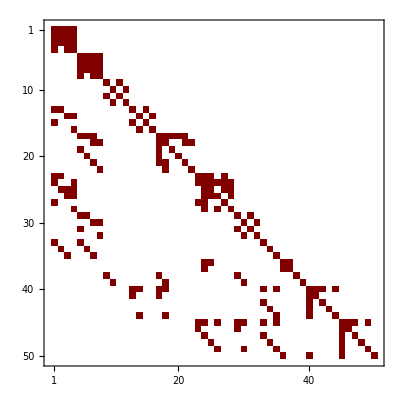

### Basis reduction: filtering

#### start

The stored A-matrix from previous overcomplete set of basis functions:

ClearAll[basis, A0, A];
Get[FileNameJoin[{NotebookDirectory[], "storage", "basis_single-massive-exchange"}]];
Get[FileNameJoin[{NotebookDirectory[], "storage", "A_single-massive-exchange"}]];
Get[FileNameJoin[{NotebookDirectory[], "storage", "A0_single-massive-exchange"}]];

basis // Length
A0[[1]] // Length
A[[1]] // Length

50

50

44

```mathematica
Amatrix=ATotal[A0,twists];
%//MatrixForm
```

(e (Log[X1+X2]-3 Log[Y]) | e (-Log[Y]+Log[X1+X2+2 Y]) | e (-Log[X1+X2]+Log[X1+X2+2 Y]) | e (2 Log[X1+X2]-2 Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+X2]-Log[Y]) | e (Log[X1+X2-2 Y]-3 Log[Y]) | e (-Log[X1+X2]+Log[X1+X2-2 Y]) | e (2 Log[X1+X2]-2 Log[X1+X2-2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X1+X2]+Log[Y]) | e (-Log[X1+X2-2 Y]+Log[Y]) | e (Log[X1+X2]-Log[X1+X2-2 Y]-2 Log[Y]) | e (-2 Log[X1+X2]+2 Log[X1+X2-2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X1+X2]+Log[Y]) | 0 | e (Log[X1+X2]-Log[Y]) | -2 e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X1+X2]-3 Log[Y]) | e (Log[X1+X2-2 Y]-Log[Y]) | e (-Log[X1+X2]+Log[X1+X2-2 Y]) | e (2 Log[X1+X2]-2 Log[X1+X2-2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[Y]) | e (-3 Log[Y]+Log[X1+X2+2 Y]) | e (-Log[X1+X2]+Log[X1+X2+2 Y]) | e (2 Log[X1+X2]-2 Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[Y]) | e (Log[Y]-Log[X1+X2+2 Y]) | e (Log[X1+X2]-2 Log[Y]-Log[X1+X2+2 Y]) | e (-2 Log[X1+X2]+2 Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[Y]) | 0 | e (Log[X1+X2]-Log[Y]) | -2 e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-4 Log[Y]+Log[X1+Y]+Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X2+Y]) | e (-2 Log[Y]+Log[X1+Y]-Log[X2+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y]) | 0 | e (-2 Log[Y]-Log[X1+Y]+Log[X2+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (Log[Y]-Log[X2+Y]) | e (-Log[X1+Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+Y]-Log[X2+Y]) | e (Log[X1-Y]-Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-4 Log[Y]+Log[X1+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (-Log[X1-Y]+Log[X2-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-Log[Y]) | e (-Log[X2-Y]-2 Log[Y]+Log[X1+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X1+Y]+Log[X2+Y]) | 0 | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y]) | 0 | e (Log[X2-Y]-2 Log[Y]-Log[X1+Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e (Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (-Log[X2-Y]+Log[Y]) | e (-Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[2 X1+X2-Y]+Log[X1+Y]) | e (Log[X1-Y]-Log[2 X1+X2-Y]) | e (Log[-2 X1-X2-Y]-Log[2 X1+X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]+Log[-2 X1-X2-Y]-Log[2 X1+X2-Y]-4 Log[Y]+Log[X1+Y]) | e (-Log[-2 X1-X2-Y]+Log[2 X1+X2-Y]) | e (-Log[2 X1+X2-Y]+Log[X1+Y]) | e (Log[X1-Y]-Log[2 X1+X2-Y]) | e (Log[-2 X1-X2-Y]-Log[2 X1+X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[-2 X1-X2-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[-2 X1-X2-Y]-Log[Y]) | e (-Log[-2 X1-X2-Y]-2 Log[Y]+Log[X1+Y]) | 0 | 0 | e (-Log[X1-Y]+Log[-2 X1-X2-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X2-3 Y]-Log[X1+Y]) | 0 | 0 | e (Log[X2-3 Y]-Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-3 Y]-Log[X1+Y]) | 0 | e (Log[X2-3 Y]+Log[X2-Y]-3 Log[Y]-Log[X1+Y]) | e (Log[X2-3 Y]-Log[Y]) | e (Log[X2-3 Y]-Log[X2-Y]) | e (-Log[X2-3 Y]+Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X2+Y]) | e (Log[X2+Y]-Log[X2+3 Y]) | e (-Log[X2+Y]+Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X2+Y]) | e (-Log[X2+Y]+Log[X2+3 Y]) | e (-Log[Y]+Log[X2+Y]) | e (-Log[X1-Y]-3 Log[Y]+Log[X2+Y]+Log[X2+3 Y]) | 0 | e (Log[X2+Y]-Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-2 X1-X2-Y]+Log[X2+3 Y]) | e (Log[X2-Y]-Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-2 X1-X2-Y]+Log[Y]) | e (Log[-2 X1-X2-Y]-Log[X2+3 Y]) | e (-Log[X2-Y]+Log[Y]) | e (Log[Y]-Log[X2+3 Y]) | e (-Log[-2 X1-X2-Y]+Log[X2-Y]-2 Log[Y]) | e (-Log[X2-Y]+Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (-Log[X2-Y]+Log[Y]) | 0 | e (Log[X2-Y]-Log[Y]) | e (-Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X2-Y]+Log[X1+2 X2+Y]) | e (-Log[X2-Y]+Log[X1+2 X2-Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-4 Log[Y]+Log[X2+Y]+Log[X1+2 X2+Y]) | e (Log[X2-Y]-Log[X1+2 X2+Y]) | e (Log[X2-Y]-Log[X1+2 X2-Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (-Log[X1+2 X2-Y]+Log[X1+2 X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+2 X2+Y]-Log[X1+3 Y]) | 0 | 0 | e (Log[X1-Y]-Log[X1+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+2 X2+Y]-Log[X1+3 Y]) | e (Log[X1-Y]-3 Log[Y]-Log[X1+2 X2+Y]+Log[X1+3 Y]) | e (-Log[Y]+Log[X1+3 Y]) | e (-Log[X1-Y]+Log[X1+3 Y]) | e (Log[X1+2 X2+Y]-Log[X1+3 Y]) | e (Log[X1-Y]-Log[X1+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | e (Log[X1+2 X2-Y]-Log[X1+Y]) | e (Log[X1-3 Y]-Log[X1+Y]) | e (-Log[X1-3 Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (Log[X1-3 Y]-Log[X1+2 X2-Y]-3 Log[Y]+Log[X1+Y]) | 0 | e (-Log[X1+2 X2-Y]+Log[X1+Y]) | e (-Log[X1-3 Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (-Log[X1-3 Y]+Log[X2+Y]) | e (Log[X1-3 Y]-Log[X1-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X2+Y]) | e (-Log[X1-Y]+Log[Y]) | e (-Log[X1-3 Y]+Log[Y]) | e (Log[X1-Y]-2 Log[Y]-Log[X2+Y]) | 0 | e (Log[X1-3 Y]-Log[X1-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X2-Y]-Log[X1+2 X2+Y]) | 0 | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+2 X2+Y]) | e (-Log[X2-Y]+Log[X1+2 X2+Y]) | 0 | 0 | e (-2 Log[Y]+Log[X2+Y]-Log[X1+2 X2+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e (-Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y]) | 0 | e (Log[X1-Y]-Log[Y]) | e (Log[Y]-Log[X2+Y]) | e (-Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2-Y]) | e (-Log[X2-Y]+Log[X1+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-4 Log[Y]+Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+Y]+Log[X2+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X2+Y]) | e (Log[X1-Y]-2 Log[Y]-Log[X2+Y]) | 0 | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X2-Y]) | 0 | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y]) | 0 | e (-Log[X1-Y]-2 Log[Y]+Log[X2+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y]) | e (Log[Y]-Log[X2+Y]) | e (-Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X1+X2]+Log[Y]) | 0 | 0 | e Log[Y] | e (Log[X1+X2]-Log[Y]) | 0 | 0 | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-2 Log[X1+X2]-Log[Y]) | 0 | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -e Log[X1+X2] | -e Log[Y] | e Log[Y] | 0 | e Log[X1+X2] | e Log[Y] | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[Y] | e (-2 Log[X1+X2]-2 Log[Y]) | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (-Log[X1+X2]+Log[Y]) | -e Log[Y] | 0 | 0 | e (Log[X1+X2]-Log[Y]) | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[Y] | 0 | e (-2 Log[X1+X2]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2]+Log[Y]) | 0 | 0 | 0 | e (Log[X2]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2]+Log[Y]) | e (-Log[Y]+Log[X1+Y]) | e (Log[X1-Y]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2]-2 Log[Y]+Log[X1+Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2]-Log[Y]) | 0 | 0 | 0 | e (-Log[X2]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | 0 | 0 | e (Log[X2]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (-Log[X2]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[X2-Y]) | 0 | e (Log[X2-Y]-Log[Y]) | e (Log[X2-Y]-Log[Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]-2 Log[Y]+Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[Y]) | 0 | 0 | e (Log[Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X2+Y]) | e (-Log[X1]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X1-Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | e (Log[X1+X2]-Log[X1-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X1+Y]) | 0 | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X1-Y]-4 Log[Y]+2 Log[X1+Y]) | e (Log[X1+X2]-Log[X1-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | e (-Log[X1+X2]+Log[X2+Y]) | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X2+Y]) | e (-Log[X1+X2]+2 Log[X2-Y]-4 Log[Y]+Log[X2+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-Log[Y]) | -e Log[Y] | 0 | 0 | e (-Log[X2-Y]+Log[Y]) | 0 | 0 | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (Log[X2-Y]-Log[Y]) | e (-Log[X2-Y]-Log[Y]-Log[X1+Y]) | 0 | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X2+Y] | e Log[Y] | -e Log[X2+Y] | -e Log[Y] | 0 | -e Log[Y] | 0 | -e Log[X2+Y] | -e Log[Y] | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | e Log[X1-Y] | e Log[X2+Y] | -e Log[Y] | e (-Log[X1-Y]-2 Log[Y]-Log[X2+Y]) | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | 0 | e Log[Y] | 0 | e (Log[Y]-Log[X1+Y]) | 0 | 0 | e (-Log[X2-Y]+Log[Y]) | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (Log[X2-Y]-Log[Y]) | e Log[Y] | 0 | e (-Log[X2-Y]-Log[Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X1+Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | e (Log[X1+X2]-Log[X1+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+2 Log[X1-Y]-4 Log[Y]+Log[X1+Y]) | e (Log[X1+X2]-Log[X1+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | e (-Log[X1-Y]+Log[X1+Y]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X2-Y]) | 0 | 0 | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | e (-Log[X1+X2]+Log[X2-Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X2-Y]) | e (-Log[X1+X2]+Log[X2-Y]-4 Log[Y]+2 Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y]) | 0 | 0 | e (-Log[Y]+Log[X2+Y]) | -e Log[Y] | 0 | 0 | e (Log[Y]-Log[X2+Y]) | e Log[Y] | e (Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y]) | e (-Log[Y]+Log[X2+Y]) | e (-Log[X1-Y]-Log[Y]-Log[X2+Y]) | 0 | e Log[Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X2-Y] | 0 | e Log[X1+Y] | e Log[Y] | -e Log[X2-Y] | -e Log[Y] | e Log[X2-Y] | -e Log[Y] | e Log[X2-Y] | e Log[Y] | 0 | e (-Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1+Y] | e Log[X2-Y] | -e Log[Y] | e (-Log[X2-Y]-2 Log[Y]-Log[X1+Y]) | -e Log[Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y]) | 0 | e Log[Y] | 0 | e (-Log[X1-Y]+Log[Y]) | 0 | -e Log[Y] | 0 | 0 | e (Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y]) | e (-Log[Y]+Log[X2+Y]) | e Log[Y] | 0 | e (-Log[X1-Y]-Log[Y]-Log[X2+Y]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[Y]) | 0 | e (-Log[X2]+Log[Y]) | 0 | e (Log[X1]-Log[Y]) | e (Log[X2]-Log[Y]) | 0 | 0 | 0 | e (-Log[X1]+Log[Y]) | e (-Log[X2]+Log[Y]) | 0 | 0 | 0 | e (-Log[X1]-Log[X2]))

```mathematica
Amatrix//Letter
%//Length
```

{X1,X2,X1+X2,X1-3 Y,X2-3 Y,X1+X2-2 Y,X1-Y,-2 X1-X2-Y,X2-Y,2 X1+X2-Y,X1+2 X2-Y,Y,X1+Y,X2+Y,X1+2 X2+Y,X1+X2+2 Y,X1+3 Y,X2+3 Y}

18

```mathematica
Coefficient[Amatrix,e]//MatrixForm
```

(Log[X1+X2]-3 Log[Y] | -Log[Y]+Log[X1+X2+2 Y] | -Log[X1+X2]+Log[X1+X2+2 Y] | 2 Log[X1+X2]-2 Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[X1+X2]-Log[Y] | Log[X1+X2-2 Y]-3 Log[Y] | -Log[X1+X2]+Log[X1+X2-2 Y] | 2 Log[X1+X2]-2 Log[X1+X2-2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+X2]+Log[Y] | -Log[X1+X2-2 Y]+Log[Y] | Log[X1+X2]-Log[X1+X2-2 Y]-2 Log[Y] | -2 Log[X1+X2]+2 Log[X1+X2-2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+X2]+Log[Y] | 0 | Log[X1+X2]-Log[Y] | -2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X1+X2]-3 Log[Y] | Log[X1+X2-2 Y]-Log[Y] | -Log[X1+X2]+Log[X1+X2-2 Y] | 2 Log[X1+X2]-2 Log[X1+X2-2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X1+X2]-Log[Y] | -3 Log[Y]+Log[X1+X2+2 Y] | -Log[X1+X2]+Log[X1+X2+2 Y] | 2 Log[X1+X2]-2 Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[X1+X2]+Log[Y] | Log[Y]-Log[X1+X2+2 Y] | Log[X1+X2]-2 Log[Y]-Log[X1+X2+2 Y] | -2 Log[X1+X2]+2 Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[X1+X2]+Log[Y] | 0 | Log[X1+X2]-Log[Y] | -2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 Log[Y]+Log[X1+Y]+Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X2+Y] | -2 Log[Y]+Log[X1+Y]-Log[X2+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X1+Y] | 0 | -2 Log[Y]-Log[X1+Y]+Log[X2+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | Log[Y]-Log[X2+Y] | -Log[X1+Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[X1+Y]-Log[X2+Y] | Log[X1-Y]-Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2-Y]-4 Log[Y]+Log[X1+Y] | -Log[X2-Y]+Log[X2+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Log[X1-Y]+Log[X2-Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2-Y]-Log[Y] | -Log[X2-Y]-2 Log[Y]+Log[X1+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+Y]+Log[X2+Y] | 0 | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X1+Y] | 0 | Log[X2-Y]-2 Log[Y]-Log[X1+Y] | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | Log[X2-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | -Log[X2-Y]+Log[Y] | -Log[X2-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[2 X1+X2-Y]+Log[X1+Y] | Log[X1-Y]-Log[2 X1+X2-Y] | Log[-2 X1-X2-Y]-Log[2 X1+X2-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]+Log[-2 X1-X2-Y]-Log[2 X1+X2-Y]-4 Log[Y]+Log[X1+Y] | -Log[-2 X1-X2-Y]+Log[2 X1+X2-Y] | -Log[2 X1+X2-Y]+Log[X1+Y] | Log[X1-Y]-Log[2 X1+X2-Y] | Log[-2 X1-X2-Y]-Log[2 X1+X2-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[-2 X1-X2-Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-2 X1-X2-Y]-Log[Y] | -Log[-2 X1-X2-Y]-2 Log[Y]+Log[X1+Y] | 0 | 0 | -Log[X1-Y]+Log[-2 X1-X2-Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X2-3 Y]-Log[X1+Y] | 0 | 0 | Log[X2-3 Y]-Log[X2-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2-3 Y]-Log[X1+Y] | 0 | Log[X2-3 Y]+Log[X2-Y]-3 Log[Y]-Log[X1+Y] | Log[X2-3 Y]-Log[Y] | Log[X2-3 Y]-Log[X2-Y] | -Log[X2-3 Y]+Log[X2-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[X2+Y] | Log[X2+Y]-Log[X2+3 Y] | -Log[X2+Y]+Log[X2+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[X2+Y] | -Log[X2+Y]+Log[X2+3 Y] | -Log[Y]+Log[X2+Y] | -Log[X1-Y]-3 Log[Y]+Log[X2+Y]+Log[X2+3 Y] | 0 | Log[X2+Y]-Log[X2+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -Log[-2 X1-X2-Y]+Log[X2+3 Y] | Log[X2-Y]-Log[X2+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-2 X1-X2-Y]+Log[Y] | Log[-2 X1-X2-Y]-Log[X2+3 Y] | -Log[X2-Y]+Log[Y] | Log[Y]-Log[X2+3 Y] | -Log[-2 X1-X2-Y]+Log[X2-Y]-2 Log[Y] | -Log[X2-Y]+Log[X2+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | -Log[X2-Y]+Log[Y] | 0 | Log[X2-Y]-Log[Y] | -Log[X2-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X2-Y]+Log[X1+2 X2+Y] | -Log[X2-Y]+Log[X1+2 X2-Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 Log[Y]+Log[X2+Y]+Log[X1+2 X2+Y] | Log[X2-Y]-Log[X1+2 X2+Y] | Log[X2-Y]-Log[X1+2 X2-Y] | Log[X2-Y]-Log[X2+Y] | -Log[X1+2 X2-Y]+Log[X1+2 X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[X1+2 X2+Y]-Log[X1+3 Y] | 0 | 0 | Log[X1-Y]-Log[X1+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1+2 X2+Y]-Log[X1+3 Y] | Log[X1-Y]-3 Log[Y]-Log[X1+2 X2+Y]+Log[X1+3 Y] | -Log[Y]+Log[X1+3 Y] | -Log[X1-Y]+Log[X1+3 Y] | Log[X1+2 X2+Y]-Log[X1+3 Y] | Log[X1-Y]-Log[X1+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Log[X1+2 X2-Y]-Log[X1+Y] | Log[X1-3 Y]-Log[X1+Y] | -Log[X1-3 Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | Log[X1-3 Y]-Log[X1+2 X2-Y]-3 Log[Y]+Log[X1+Y] | 0 | -Log[X1+2 X2-Y]+Log[X1+Y] | -Log[X1-3 Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Log[X1-3 Y]+Log[X2+Y] | Log[X1-3 Y]-Log[X1-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X2+Y] | -Log[X1-Y]+Log[Y] | -Log[X1-3 Y]+Log[Y] | Log[X1-Y]-2 Log[Y]-Log[X2+Y] | 0 | Log[X1-3 Y]-Log[X1-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[X2-Y]-Log[X1+2 X2+Y] | 0 | 0 | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X1+2 X2+Y] | -Log[X2-Y]+Log[X1+2 X2+Y] | 0 | 0 | -2 Log[Y]+Log[X2+Y]-Log[X1+2 X2+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -Log[X1-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[Y] | 0 | Log[X1-Y]-Log[Y] | Log[Y]-Log[X2+Y] | -Log[X1-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X1-Y]-Log[X2-Y] | -Log[X2-Y]+Log[X1+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-4 Log[Y]+Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -Log[X1+Y]+Log[X2+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X2+Y] | Log[X1-Y]-2 Log[Y]-Log[X2+Y] | 0 | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[X1-Y]+Log[X2-Y] | 0 | 0 | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[Y] | 0 | -Log[X1-Y]-2 Log[Y]+Log[X2+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[Y] | Log[Y]-Log[X2+Y] | -Log[X1-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+X2]+Log[Y] | 0 | 0 | Log[Y] | Log[X1+X2]-Log[Y] | 0 | 0 | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 Log[X1+X2]-Log[Y] | 0 | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -Log[X1+X2] | -Log[Y] | Log[Y] | 0 | Log[X1+X2] | Log[Y] | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y] | -2 Log[X1+X2]-2 Log[Y] | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Log[X1+X2]+Log[Y] | -Log[Y] | 0 | 0 | Log[X1+X2]-Log[Y] | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y] | 0 | -2 Log[X1+X2]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2]+Log[Y] | 0 | 0 | 0 | Log[X2]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2]+Log[Y] | -Log[Y]+Log[X1+Y] | Log[X1-Y]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2]-2 Log[Y]+Log[X1+Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2]-Log[Y] | 0 | 0 | 0 | -Log[X2]+Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | 0 | 0 | Log[X2]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | -Log[X2]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1]+Log[X2-Y] | 0 | Log[X2-Y]-Log[Y] | Log[X2-Y]-Log[Y] | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1]-2 Log[Y]+Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1]+Log[Y] | 0 | 0 | Log[Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X2+Y] | -Log[X1]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1+X2]+Log[X1-Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | Log[X1+X2]-Log[X1-Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[X1+Y] | 0 | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | -Log[X1+X2]+Log[X1-Y]-4 Log[Y]+2 Log[X1+Y] | Log[X1+X2]-Log[X1-Y] | Log[X1-Y]-Log[X1+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1+X2]-Log[X2+Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0 | -Log[X1+X2]+Log[X2+Y] | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | Log[X1+X2]-Log[X2+Y] | -Log[X1+X2]+2 Log[X2-Y]-4 Log[Y]+Log[X2+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2-Y]-Log[Y] | -Log[Y] | 0 | 0 | -Log[X2-Y]+Log[Y] | 0 | 0 | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | Log[X2-Y]-Log[Y] | -Log[X2-Y]-Log[Y]-Log[X1+Y] | 0 | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2+Y] | Log[Y] | -Log[X2+Y] | -Log[Y] | 0 | -Log[Y] | 0 | -Log[X2+Y] | -Log[Y] | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | Log[X1-Y] | Log[X2+Y] | -Log[Y] | -Log[X1-Y]-2 Log[Y]-Log[X2+Y] | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | 0 | Log[Y] | 0 | Log[Y]-Log[X1+Y] | 0 | 0 | -Log[X2-Y]+Log[Y] | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | Log[X2-Y]-Log[Y] | Log[Y] | 0 | -Log[X2-Y]-Log[Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1+X2]+Log[X1+Y] | Log[X1-Y]-Log[X1+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | Log[X1+X2]-Log[X1+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | Log[X1-Y]-Log[X1+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1+X2]+2 Log[X1-Y]-4 Log[Y]+Log[X1+Y] | Log[X1+X2]-Log[X1+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | -Log[X1-Y]+Log[X1+Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1+X2]-Log[X2-Y] | 0 | 0 | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | -Log[X1+X2]+Log[X2-Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1+X2]-Log[X2-Y] | -Log[X1+X2]+Log[X2-Y]-4 Log[Y]+2 Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[Y] | 0 | 0 | -Log[Y]+Log[X2+Y] | -Log[Y] | 0 | 0 | Log[Y]-Log[X2+Y] | Log[Y] | Log[X1-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[Y] | -Log[Y]+Log[X2+Y] | -Log[X1-Y]-Log[Y]-Log[X2+Y] | 0 | Log[Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2-Y] | 0 | Log[X1+Y] | Log[Y] | -Log[X2-Y] | -Log[Y] | Log[X2-Y] | -Log[Y] | Log[X2-Y] | Log[Y] | 0 | -Log[X2-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1+Y] | Log[X2-Y] | -Log[Y] | -Log[X2-Y]-2 Log[Y]-Log[X1+Y] | -Log[Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[Y] | 0 | Log[Y] | 0 | -Log[X1-Y]+Log[Y] | 0 | -Log[Y] | 0 | 0 | Log[X1-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[Y] | -Log[Y]+Log[X2+Y] | Log[Y] | 0 | -Log[X1-Y]-Log[Y]-Log[X2+Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1]-Log[Y] | 0 | -Log[X2]+Log[Y] | 0 | Log[X1]-Log[Y] | Log[X2]-Log[Y] | 0 | 0 | 0 | -Log[X1]+Log[Y] | -Log[X2]+Log[Y] | 0 | 0 | 0 | -Log[X1]-Log[X2])

we can pick

```mathematica
need=Position[basis,#]&/@{⟨1,3,5,6⟩,⟨2,4,5,6⟩,⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨3,5,7,9⟩,⟨4,5,7,9⟩,⟨1,3,7,9⟩,⟨2,4,7,9⟩}//Flatten
```

{13,29,1,2,3,5,6,7,14,15,30,31,4,8,16,32}

```mathematica
AmatrixNeed=Amatrix[[need,need]];
%//MatrixPlot
```

-Graphics-

```mathematica
basisNeed=basis[[need]]
```

{⟨1,3,5,6⟩,⟨2,4,5,6⟩,⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨3,5,7,9⟩,⟨4,5,7,9⟩,⟨1,3,7,9⟩,⟨2,4,7,9⟩}

#### level 0

```mathematica
dRep=Thread[(d/@basisNeed)->Coefficient[AmatrixNeed,e].basisNeed];
```

```mathematica
l0={Log[X1+Y],Log[X2+Y],Log[Y]};(*old letters*)
```

```mathematica
Basis={psi};
```

```mathematica
BasisCount={1};
```

#### level 1

all letters appeared until level 1:

```mathematica
d1=psi/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l1=Cases[%,_Log,Infinity]//Union;
Complement[l1,l0]
```

{Log[X1-Y],Log[X2-Y]}

only add the basis for new letters:

```mathematica
lv2=Coefficient[d1,#]&/@Complement[l1,l0]
%//Length
```

{-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨4,5,6,7⟩,⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩+⟨3,5,6,9⟩+⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩}

2

```mathematica
Basis=Join[Basis,lv2];
```

then add the basis for old letters if linearly-independent:

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basisNeed;
sol=Solve[eqn==0,Cases[eqn,_c,Infinity]//Union](*//First*);
Return[If[sol=!={},True,False]]]
```

```mathematica
lv2Old=Coefficient[d1,#]&/@l0//Flatten
```

{⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+⟨3,5,6,7⟩-⟨4,5,6,8⟩,⟨1,3,5,9⟩-⟨2,4,5,6⟩+⟨2,4,5,9⟩-⟨3,5,6,7⟩-⟨3,5,6,8⟩-⟨3,5,6,9⟩-⟨4,5,6,9⟩,-4 ⟨1,3,5,6⟩+4 ⟨2,4,5,6⟩}

```mathematica
Do[If[!CheckDependent[lv2Old,i,Basis],Basis=Join[Basis,{lv2Old[[i]]}];],{i,Length[lv2Old]}]
```

```mathematica
Basis//Length
```

4

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,3}

#### level 2

```mathematica
d2=Basis[[(BasisCount[[;;-2]]//Total)+1;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l2=Cases[%,_Log,Infinity]//Union;
Complement[l2,l1]
```

{Log[X1+X2],Log[X1+X2-2 Y],Log[X1+X2+2 Y]}

```mathematica
Coefficient[d2,#]&/@Complement[l2,l1];(*new letters*)
(Sort[{#,-#}]&/@Flatten[%])//Union ;(*this seems to be a key step: from 5x4 to 4*)
%//MatrixForm
lv3=%[[All;;,1]]//DeleteCases[0]
```

(0 | 0
⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩ | -⟨3,5,6,7⟩+⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩+⟨4,5,6,7⟩-⟨4,5,6,9⟩+2 ⟨4,5,7,9⟩
-⟨3,5,6,8⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩ | ⟨3,5,6,8⟩+⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩-⟨4,5,6,8⟩-⟨4,5,6,9⟩+2 ⟨4,5,7,9⟩)

{⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩,-⟨3,5,6,8⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩}

```mathematica
Do[If[! CheckDependent[lv3, i, Basis], Basis = Join[Basis, {lv3[[i]]}];], {i, Length[lv3]}];
Basis//Length
```

5

```mathematica
lv3Old = Coefficient[d2, #] & /@Join[ l0,l1] // Flatten//DeleteCases[0];
```

```mathematica
lv3Old//Length
```

20

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,vars,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basisNeed;
vars=Union@Cases[eqn,_c,Infinity];
sol=Quiet@Solve[Thread[eqn==0],vars];
sol=!={}]
```

```mathematica
Table[CheckDependent[lv3Old, i, Basis],{i,1,Length[lv3Old]}]
```

{True,False,False,True,False,True,True,True,False,True,False,False,True,True,True,True,False,False,True,False}

```mathematica
Do[If[! CheckDependent[lv3Old, i, Basis], Basis = Join[Basis, {lv3Old[[i]]}];], {i, Length[lv3Old]}]
```

```mathematica
Basis//Length
```

6

```mathematica
Position[lv3Old,#]&/@Basis[[{6}]]
```

{{{2},{17}}}

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,3,2}

#### close at level 3

```mathematica
d3 = Basis[[(BasisCount[[;; -2]] // Total) + 1 ;;]] /. AngleBracket[a___] -> d[AngleBracket[a]] /. dRep;
l3 = Cases[%, _Log, Infinity] // Union;
Complement[l3, l2]
```

{}

```mathematica
lv4Old = Coefficient[d3, #] & /@ Join[ l0, l1, l2] // Flatten // DeleteCases[0];
```

```mathematica
lv4Old // Length
```

14

```mathematica
Do[If[! CheckDependent[lv4Old, i, Basis], Basis = Join[Basis, {lv4Old[[i]]}];], {i, Length[lv4Old]}]
```

```mathematica
Basis // Length
```

6

#### summary: all physical basis

```mathematica
letters={l0,l1,l2}//Flatten//Union
%//Length
```

{Log[X1+X2],Log[X1+X2-2 Y],Log[X1-Y],Log[X2-Y],Log[Y],Log[X1+Y],Log[X2+Y],Log[X1+X2+2 Y]}

8

6 = 1 + (2+1) + (1+1)
7 = 3 + 2 + 3

```mathematica
Basis//MatrixForm
Basis//Length
```

(⟨1,3,5,6⟩-⟨2,4,5,6⟩
-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨4,5,6,7⟩
⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩+⟨3,5,6,9⟩+⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩
⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+⟨3,5,6,7⟩-⟨4,5,6,8⟩
⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩
⟨1,3,5,6⟩-⟨1,3,5,9⟩+⟨1,3,6,7⟩+⟨1,3,7,9⟩-⟨2,4,7,9⟩+⟨3,5,6,7⟩+⟨3,5,7,9⟩+⟨4,5,6,9⟩-⟨4,5,7,9⟩)

6

see how this 6d subspace is embedded in the previous 50d space:

```mathematica
BasisIndex=Basis/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])];
%//MatrixForm
```

(φ_1-φ_2
-φ_2+φ_4-φ_6-φ_10-φ_12
φ_1+φ_5+φ_6+φ_7+φ_8-φ_9-φ_11
φ_1+φ_3-φ_7+φ_10+φ_12
φ_3-φ_5-φ_6+φ_8+2 φ_13-2 φ_14
φ_1+φ_3+φ_8-φ_9+φ_10+φ_13-φ_14+φ_15-φ_16)

```mathematica
psi/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])]
```

φ_1-φ_2

so psi is just the new basis 1.

### Impose symmetry in the basisNeed:

thanks to FRW, we got 2 more basis. Hopefully, this will prevent the X1+X2 from vanishing

```mathematica
basisNeed
toBracket=Thread[(Subscript[φ,#]&/@Range[%//Length])->%]
```

{⟨1,3,5,6⟩,⟨2,4,5,6⟩,⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨3,5,7,9⟩,⟨4,5,7,9⟩,⟨1,3,7,9⟩,⟨2,4,7,9⟩}

{φ_1→⟨1,3,5,6⟩,φ_2→⟨2,4,5,6⟩,φ_3→⟨3,5,6,7⟩,φ_4→⟨3,5,6,8⟩,φ_5→⟨3,5,6,9⟩,φ_6→⟨4,5,6,7⟩,φ_7→⟨4,5,6,8⟩,φ_8→⟨4,5,6,9⟩,φ_9→⟨1,3,5,9⟩,φ_10→⟨1,3,6,7⟩,φ_11→⟨2,4,5,9⟩,φ_12→⟨2,4,6,7⟩,φ_13→⟨3,5,7,9⟩,φ_14→⟨4,5,7,9⟩,φ_15→⟨1,3,7,9⟩,φ_16→⟨2,4,7,9⟩}

```mathematica
symForBasis={⟨4,5,7,9⟩->-⟨3,5,7,9⟩,⟨3,5,6,7⟩->⟨4,5,6,9⟩,⟨4,5,6,7⟩->⟨3,5,6,9⟩,⟨4,5,6,8⟩->-⟨3,5,6,8⟩-⟨3,5,6,9⟩-⟨4,5,6,9⟩}/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])]
```

{φ_14→-φ_13,φ_3→φ_8,φ_6→φ_5,φ_7→-φ_4-φ_5-φ_8}

```mathematica
BasisSym=BasisIndex/.symForBasis//Simplify;
%//MatrixForm
```

(φ_1-φ_2
2 φ_1-φ_2+φ_4-φ_5-φ_10-φ_12
φ_1-2 φ_2-φ_4+φ_5-φ_9-φ_11
φ_1-2 φ_2+φ_4+φ_5+2 φ_8+φ_10+φ_12
2 (2 φ_4+φ_5+φ_8+2 φ_13)
-2 (φ_4+φ_5+4 φ_8-2 φ_13)
2 (2 φ_4+φ_5+φ_8+2 φ_13)
φ_1-4 φ_2+2 φ_4+2 φ_5+2 φ_8-φ_9+φ_10-2 φ_11+2 φ_12+2 φ_13+φ_15-φ_16)

```mathematica
Table[Coefficient[BasisSym[[i]],Subscript[φ,j]],{i,1,8},{j,1,16}]
```

{{1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,-1,0,1,-1,0,0,0,0,-1,0,-1,0,0,0,0},{1,-2,0,-1,1,0,0,0,-1,0,-1,0,0,0,0,0},{1,-2,0,1,1,0,0,2,0,1,0,1,0,0,0,0},{0,0,0,4,2,0,0,2,0,0,0,0,4,0,0,0},{0,0,0,-2,-2,0,0,-8,0,0,0,0,4,0,0,0},{0,0,0,4,2,0,0,2,0,0,0,0,4,0,0,0},{1,-4,0,2,2,0,0,2,-1,1,-2,2,2,0,1,-1}}

```mathematica
%//MatrixRank
```

7

only remove one basis

### A matrix (associated to physical basis)

```mathematica
Umatrix=Table[Coefficient[Basis[[i]],basisNeed[[j]]],{i,1,Length[Basis]},{j,1,Length[basisNeed]}];
Uinv=Simplify[PseudoInverse[Umatrix]];
```

```mathematica
Amatrix6=Umatrix.AmatrixNeed.Uinv//Simplify;
%//MatrixForm
```

(2 e (-2 Log[Y]+Log[X2+Y]) | e (Log[X1-Y]-Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (Log[X1+Y]-Log[X2+Y]) | 0 | 0
e (-Log[X1+X2-2 Y]+Log[X2+Y]) | e (Log[X1+X2-2 Y]-3 Log[Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (Log[X1+X2-2 Y]-Log[Y]+Log[X1+Y]-Log[X2+Y]) | e (Log[X1+X2]-Log[X1+X2-2 Y]+Log[X2-Y]-Log[X2+Y]) | e (-Log[X2-Y]+Log[X2+Y])
e (Log[X1+X2-2 Y]-Log[X1-Y]-2 Log[Y]+2 Log[X2+Y]) | e (-Log[X1+X2-2 Y]+Log[X1-Y]+Log[Y]-Log[X2+Y]) | e (Log[X1-Y]-2 Log[Y]-Log[X2+Y]) | e (-Log[X1+X2-2 Y]+Log[X1-Y]+Log[Y]-Log[X2+Y]) | e (-Log[X1+X2]+Log[X1+X2-2 Y]) | e (-Log[X1-Y]+Log[X1+Y])
e (Log[X2+Y]-Log[X1+X2+2 Y]) | e (Log[X1-Y]-Log[Y]-Log[X2+Y]+Log[X1+X2+2 Y]) | 0 | e (-3 Log[Y]+Log[X1+X2+2 Y]) | e (Log[X1+X2]-Log[X2-Y]+Log[X2+Y]-Log[X1+X2+2 Y]) | e (Log[X2-Y]-Log[X2+Y])
-e (Log[X1+X2-2 Y]-2 Log[Y]+Log[X1+X2+2 Y]) | e (Log[X1+X2-2 Y]-2 Log[Y]+Log[X1+X2+2 Y]) | 0 | e (Log[X1+X2-2 Y]-2 Log[Y]+Log[X1+X2+2 Y]) | -e (Log[X1+X2-2 Y]+Log[X1+X2+2 Y]) | 0
e (-Log[X1-Y]+Log[Y]+Log[X2+Y]-Log[X1+X2+2 Y]) | e (Log[X1-Y]-Log[Y]-Log[X2+Y]+Log[X1+X2+2 Y]) | e (Log[X1-Y]-Log[Y]) | e (Log[X1-Y]-2 Log[Y]+Log[X1+X2+2 Y]) | e (Log[X2+Y]-Log[X1+X2+2 Y]) | -e (Log[X1-Y]+Log[X2+Y]))

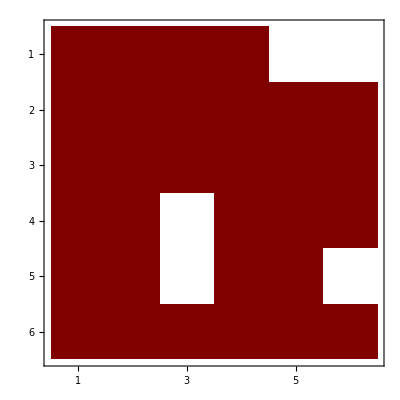

```mathematica
Amatrix6//MatrixPlot
```

```mathematica
Basis//MatrixForm
```

(⟨1,3,5,6⟩-⟨2,4,5,6⟩
-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨4,5,6,7⟩
⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩+⟨3,5,6,9⟩+⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩
⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+⟨3,5,6,7⟩-⟨4,5,6,8⟩
⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩
⟨1,3,5,6⟩-⟨1,3,5,9⟩+⟨1,3,6,7⟩+⟨1,3,7,9⟩-⟨2,4,7,9⟩+⟨3,5,6,7⟩+⟨3,5,7,9⟩+⟨4,5,6,9⟩-⟨4,5,7,9⟩)

turn the basis into 1/(l_i1 l_i2 l_i3 l_i4)

```mathematica
Amatrix6//MatrixForm
```

(2 e (-2 Log[Y]+Log[X2+Y]) | e (Log[X1-Y]-Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (Log[X1+Y]-Log[X2+Y]) | 0 | 0
e (-Log[X1+X2-2 Y]+Log[X2+Y]) | e (Log[X1+X2-2 Y]-3 Log[Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (Log[X1+X2-2 Y]-Log[Y]+Log[X1+Y]-Log[X2+Y]) | e (Log[X1+X2]-Log[X1+X2-2 Y]+Log[X2-Y]-Log[X2+Y]) | e (-Log[X2-Y]+Log[X2+Y])
e (Log[X1+X2-2 Y]-Log[X1-Y]-2 Log[Y]+2 Log[X2+Y]) | e (-Log[X1+X2-2 Y]+Log[X1-Y]+Log[Y]-Log[X2+Y]) | e (Log[X1-Y]-2 Log[Y]-Log[X2+Y]) | e (-Log[X1+X2-2 Y]+Log[X1-Y]+Log[Y]-Log[X2+Y]) | e (-Log[X1+X2]+Log[X1+X2-2 Y]) | e (-Log[X1-Y]+Log[X1+Y])
e (Log[X2+Y]-Log[X1+X2+2 Y]) | e (Log[X1-Y]-Log[Y]-Log[X2+Y]+Log[X1+X2+2 Y]) | 0 | e (-3 Log[Y]+Log[X1+X2+2 Y]) | e (Log[X1+X2]-Log[X2-Y]+Log[X2+Y]-Log[X1+X2+2 Y]) | e (Log[X2-Y]-Log[X2+Y])
-e (Log[X1+X2-2 Y]-2 Log[Y]+Log[X1+X2+2 Y]) | e (Log[X1+X2-2 Y]-2 Log[Y]+Log[X1+X2+2 Y]) | 0 | e (Log[X1+X2-2 Y]-2 Log[Y]+Log[X1+X2+2 Y]) | -e (Log[X1+X2-2 Y]+Log[X1+X2+2 Y]) | 0
e (-Log[X1-Y]+Log[Y]+Log[X2+Y]-Log[X1+X2+2 Y]) | e (Log[X1-Y]-Log[Y]-Log[X2+Y]+Log[X1+X2+2 Y]) | e (Log[X1-Y]-Log[Y]) | e (Log[X1-Y]-2 Log[Y]+Log[X1+X2+2 Y]) | e (Log[X2+Y]-Log[X1+X2+2 Y]) | -e (Log[X1-Y]+Log[X2+Y]))

```mathematica
Coefficient[Amatrix6,e]/.Thread[lett->Table[Subscript[l, i],{i,1,Length[letters]}]]//Simplify
%//MatrixForm
```

{{2 (l_2-2 l_3),-l_2+l_4,-l_2+l_5,l_1-l_2,0,0},{l_2-l_7,-3 l_3+l_7,-l_2+l_5,l_1-l_2-l_3+l_7,-l_2+l_5+l_6-l_7,l_2-l_5},{2 l_2-2 l_3-l_4+l_7,-l_2+l_3+l_4-l_7,-l_2-2 l_3+l_4,-l_2+l_3+l_4-l_7,-l_6+l_7,l_1-l_4},{l_2-l_8,-l_2-l_3+l_4+l_8,0,-3 l_3+l_8,l_2-l_5+l_6-l_8,-l_2+l_5},{2 l_3-l_7-l_8,-2 l_3+l_7+l_8,0,-2 l_3+l_7+l_8,-l_7-l_8,0},{l_2+l_3-l_4-l_8,-l_2-l_3+l_4+l_8,-l_3+l_4,-2 l_3+l_4+l_8,l_2-l_8,-l_2-l_4}}

(2 (l_2-2 l_3) | -l_2+l_4 | -l_2+l_5 | l_1-l_2 | 0 | 0
l_2-l_7 | -3 l_3+l_7 | -l_2+l_5 | l_1-l_2-l_3+l_7 | -l_2+l_5+l_6-l_7 | l_2-l_5
2 l_2-2 l_3-l_4+l_7 | -l_2+l_3+l_4-l_7 | -l_2-2 l_3+l_4 | -l_2+l_3+l_4-l_7 | -l_6+l_7 | l_1-l_4
l_2-l_8 | -l_2-l_3+l_4+l_8 | 0 | -3 l_3+l_8 | l_2-l_5+l_6-l_8 | -l_2+l_5
2 l_3-l_7-l_8 | -2 l_3+l_7+l_8 | 0 | -2 l_3+l_7+l_8 | -l_7-l_8 | 0
l_2+l_3-l_4-l_8 | -l_2-l_3+l_4+l_8 | -l_3+l_4 | -2 l_3+l_4+l_8 | l_2-l_8 | -l_2-l_4)

```mathematica
({{2 (-2 Subscript[l, 5]+Subscript[l, 7]), Subscript[l, 3]-Subscript[l, 7], Subscript[l, 4]-Subscript[l, 7], Subscript[l, 6]-Subscript[l, 7], 0, 0}, {-Subscript[l, 2]+Subscript[l, 7], Subscript[l, 2]-3 Subscript[l, 5], Subscript[l, 4]-Subscript[l, 7], Subscript[l, 2]-Subscript[l, 5]+Subscript[l, 6]-Subscript[l, 7], Subscript[l, 1]-Subscript[l, 2]+Subscript[l, 4]-Subscript[l, 7], -Subscript[l, 4]+Subscript[l, 7]}, {Subscript[l, 2]-Subscript[l, 3]-2 Subscript[l, 5]+2 Subscript[l, 7], -Subscript[l, 2]+Subscript[l, 3]+Subscript[l, 5]-Subscript[l, 7], Subscript[l, 3]-2 Subscript[l, 5]-Subscript[l, 7], -Subscript[l, 2]+Subscript[l, 3]+Subscript[l, 5]-Subscript[l, 7], -Subscript[l, 1]+Subscript[l, 2], -Subscript[l, 3]+Subscript[l, 6]}, {Subscript[l, 7]-Subscript[l, 8], Subscript[l, 3]-Subscript[l, 5]-Subscript[l, 7]+Subscript[l, 8], 0, -3 Subscript[l, 5]+Subscript[l, 8], Subscript[l, 1]-Subscript[l, 4]+Subscript[l, 7]-Subscript[l, 8], Subscript[l, 4]-Subscript[l, 7]}, {-Subscript[l, 2]+2 Subscript[l, 5]-Subscript[l, 8], Subscript[l, 2]-2 Subscript[l, 5]+Subscript[l, 8], 0, Subscript[l, 2]-2 Subscript[l, 5]+Subscript[l, 8], -Subscript[l, 2]-Subscript[l, 8], 0}, {-Subscript[l, 3]+Subscript[l, 5]+Subscript[l, 7]-Subscript[l, 8], Subscript[l, 3]-Subscript[l, 5]-Subscript[l, 7]+Subscript[l, 8], Subscript[l, 3]-Subscript[l, 5], Subscript[l, 3]-2 Subscript[l, 5]+Subscript[l, 8], Subscript[l, 7]-Subscript[l, 8], -Subscript[l, 3]-Subscript[l, 7]}})//MatrixRank
```

6

```mathematica
A6=Coefficient[Amatrix6,e]/. Thread[lett->Table[ToExpression["L"<>ToString[i]],{i,1,Length[letters]}]]//Simplify
```

{{2 (L2-2 L3),-L2+L4,-L2+L5,L1-L2,0,0},{L2-L7,-3 L3+L7,-L2+L5,L1-L2-L3+L7,-L2+L5+L6-L7,L2-L5},{2 L2-2 L3-L4+L7,-L2+L3+L4-L7,-L2-2 L3+L4,-L2+L3+L4-L7,-L6+L7,L1-L4},{L2-L8,-L2-L3+L4+L8,0,-3 L3+L8,L2-L5+L6-L8,-L2+L5},{2 L3-L7-L8,-2 L3+L7+L8,0,-2 L3+L7+L8,-L7-L8,0},{L2+L3-L4-L8,-L2-L3+L4+L8,-L3+L4,-2 L3+L4+L8,L2-L8,-L2-L4}}

```mathematica
%//MatrixForm
```

(2 (L2-2 L3) | -L2+L4 | -L2+L5 | L1-L2 | 0 | 0
L2-L7 | -3 L3+L7 | -L2+L5 | L1-L2-L3+L7 | -L2+L5+L6-L7 | L2-L5
2 L2-2 L3-L4+L7 | -L2+L3+L4-L7 | -L2-2 L3+L4 | -L2+L3+L4-L7 | -L6+L7 | L1-L4
L2-L8 | -L2-L3+L4+L8 | 0 | -3 L3+L8 | L2-L5+L6-L8 | -L2+L5
2 L3-L7-L8 | -2 L3+L7+L8 | 0 | -2 L3+L7+L8 | -L7-L8 | 0
L2+L3-L4-L8 | -L2-L3+L4+L8 | -L3+L4 | -2 L3+L4+L8 | L2-L8 | -L2-L4)

{1,2,3} {4,5} {6,7,8}
notice that l7, l8 are suspicious poles. To eliminate the spurious poles, we may further reduce the size. (there is further redundancy in the integral repr. of Hankel function)
6 = 1 + (2+1) + (1+1)

```mathematica
letters
```

{Log[X1+X2],Log[X1+X2-2 Y],Log[X1-Y],Log[X2-Y],Log[Y],Log[X1+Y],Log[X2+Y],Log[X1+X2+2 Y]}

```mathematica
l0
```

{Log[X1+Y],Log[X2+Y],Log[Y]}

```mathematica
Complement[l1,l0]
```

{Log[X1-Y],Log[X2-Y]}

```mathematica
Complement[l2,l1]
```

{Log[X1+X2],Log[X1+X2-2 Y],Log[X1+X2+2 Y]}

```mathematica
lett=Join[l0,Complement[l1,l0],Complement[l2,l1]]
```

{Log[X1+Y],Log[X2+Y],Log[Y],Log[X1-Y],Log[X2-Y],Log[X1+X2],Log[X1+X2-2 Y],Log[X1+X2+2 Y]}

the matrix is not upper triangular...
we need to orthogonalize the new basis appearing at each level.

```mathematica
A6x1=A6/.{L2->0,L3->0,L5->0};
%//MatrixForm
%%//MatrixRank
```

(0 | L4 | 0 | L1 | 0 | 0
-L7 | L7 | 0 | L1+L7 | L6-L7 | 0
-L4+L7 | L4-L7 | L4 | L4-L7 | -L6+L7 | L1-L4
-L8 | L4+L8 | 0 | L8 | L6-L8 | 0
-L7-L8 | L7+L8 | 0 | L7+L8 | -L7-L8 | 0
-L4-L8 | L4+L8 | L4 | L4+L8 | -L8 | -L4)

6

```mathematica
A6x1//Det
```

-2 L1^2 L4^2 L6 (L7+L8)

```mathematica
A6x2//Det
```

-2 L2^2 L5^2 L6 (L7+L8)

```mathematica
A6x2=A6/.{L1->0,L3->0,L4->0};
%//MatrixForm
%%//MatrixRank
```

(2 L2 | -L2 | -L2+L5 | -L2 | 0 | 0
L2-L7 | L7 | -L2+L5 | -L2+L7 | -L2+L5+L6-L7 | L2-L5
2 L2+L7 | -L2-L7 | -L2 | -L2-L7 | -L6+L7 | 0
L2-L8 | -L2+L8 | 0 | L8 | L2-L5+L6-L8 | -L2+L5
-L7-L8 | L7+L8 | 0 | L7+L8 | -L7-L8 | 0
L2-L8 | -L2+L8 | 0 | L8 | L2-L8 | -L2)

6

```mathematica
A6y=A6/.{L6->0};
%//MatrixForm
%%//MatrixRank
```

(2 (L2-2 L3) | -L2+L4 | -L2+L5 | L1-L2 | 0 | 0
L2-L7 | -3 L3+L7 | -L2+L5 | L1-L2-L3+L7 | -L2+L5-L7 | L2-L5
2 L2-2 L3-L4+L7 | -L2+L3+L4-L7 | -L2-2 L3+L4 | -L2+L3+L4-L7 | L7 | L1-L4
L2-L8 | -L2-L3+L4+L8 | 0 | -3 L3+L8 | L2-L5-L8 | -L2+L5
2 L3-L7-L8 | -2 L3+L7+L8 | 0 | -2 L3+L7+L8 | -L7-L8 | 0
L2+L3-L4-L8 | -L2-L3+L4+L8 | -L3+L4 | -2 L3+L4+L8 | L2-L8 | -L2-L4)

6

#### convert to 1/(l...l)

```mathematica
Basis=({{⟨1,3,5,6⟩-⟨2,4,5,6⟩}, {-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨4,5,6,7⟩}, {⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩+⟨3,5,6,9⟩+⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩}, {⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+⟨3,5,6,7⟩-⟨4,5,6,8⟩}, {⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩}, {⟨1,3,5,6⟩-⟨1,3,5,9⟩+⟨1,3,6,7⟩+⟨1,3,7,9⟩-⟨2,4,7,9⟩+⟨3,5,6,7⟩+⟨3,5,7,9⟩+⟨4,5,6,9⟩-⟨4,5,7,9⟩}});
```

```mathematica
initialize[] := (
nplane = nBplane+nTplane;
X = Append[Table[z[i] = Symbol["z" <> ToString[i]], {i, 1, dim}],1];
Lplanes = Join[Table[Global`B[i] . X, {i, nBplane}], Table[Global`T[i] . X, {i, nTplane}]];
perm=Permutations[Range[dim]];
Jac =Table[D[Lplanes[[i]],z[j]],{j,1,dim},{i,1,Length[Lplanes]}];

replaceTplane=Table[i->(i+nBplane),{i,1,nTplane}];
power=Join[ConstantArray[0,{nBplane}],powers];
dkin = Map[Symbol["d" <> ToString[#]] &, kin];
);
initialize[]
```

```mathematica
X
```

{z1,z2,z3,z4,1}

```mathematica
Lplanes
```

{X1+Y+z1+Y z3,X2+Y+z2+Y z4,X1+X2+z1+z2+Y z3-Y z4,X1+X2+z1+z2-Y z3+Y z4,z1,z2,z3,2+z3,z4,2+z4}

```mathematica
EiVertex[Vertex_List]:=Sum[Signature[perm[[i]]](1/ Product[Subscript[l, Vertex[[j]]],{j,1,dim}]) Product[Jac[[perm[[i,k]],Vertex[[k]]]],{k,1,dim}],
		{i,1,Length[perm]}];
```

```mathematica
BasisL=Basis/.⟨a__⟩:>(EiVertex[{a}])
```

{-Y^2/(l_1 l_3 l_5 l_6)-Y^2/(l_2 l_4 l_5 l_6),-Y^2/(l_2 l_4 l_5 l_6)+Y/(l_1 l_3 l_6 l_7)+Y/(l_2 l_4 l_6 l_7)+Y/(l_4 l_5 l_6 l_7)+Y/(l_3 l_5 l_6 l_8),-Y^2/(l_1 l_3 l_5 l_6)-Y/(l_4 l_5 l_6 l_7)-Y/(l_4 l_5 l_6 l_8)+Y/(l_1 l_3 l_5 l_9)+Y/(l_2 l_4 l_5 l_9)+Y/(l_3 l_5 l_6 l_9)-Y/(l_4 l_5 l_6 l_9),-Y^2/(l_1 l_3 l_5 l_6)-Y/(l_1 l_3 l_6 l_7)-Y/(l_2 l_4 l_6 l_7)+Y/(l_3 l_5 l_6 l_7)+Y/(l_4 l_5 l_6 l_8),Y/(l_3 l_5 l_6 l_7)+Y/(l_4 l_5 l_6 l_7)-Y/(l_3 l_5 l_6 l_9)-Y/(l_4 l_5 l_6 l_9)-2/(l_3 l_5 l_7 l_9)+2/(l_4 l_5 l_7 l_9),-Y^2/(l_1 l_3 l_5 l_6)-Y/(l_1 l_3 l_6 l_7)+Y/(l_3 l_5 l_6 l_7)+Y/(l_1 l_3 l_5 l_9)-Y/(l_4 l_5 l_6 l_9)+1/(l_1 l_3 l_7 l_9)+1/(l_2 l_4 l_7 l_9)-1/(l_3 l_5 l_7 l_9)+1/(l_4 l_5 l_7 l_9)}

```mathematica
Lplanes
```

{X1+Y+z1+Y z3,X2+Y+z2+Y z4,X1+X2+z1+z2+Y z3-Y z4,X1+X2+z1+z2-Y z3+Y z4,z1,z2,z3,2+z3,z4,2+z4}

```mathematica
BasisZ=BasisL/.Thread[Table[Subscript[l, i],{i,1,Length[Lplanes]}]->Lplanes];
```

量纲分析：[z1]=[z2]=[X1]=[X2]=[Y]=+1, [z3]=[z4]=0. 
So [Integrand]=-2.

```mathematica
BasisZ[[-1]]
```

Y/(z1 z2 z3 (X1+X2+z1+z2+Y z3-Y z4))-Y^2/(z1 z2 (X1+Y+z1+Y z3) (X1+X2+z1+z2+Y z3-Y z4))-Y/(z2 z3 (X1+Y+z1+Y z3) (X1+X2+z1+z2+Y z3-Y z4))-1/(z1 z3 z4 (X1+X2+z1+z2+Y z3-Y z4))+Y/(z1 (X1+Y+z1+Y z3) z4 (X1+X2+z1+z2+Y z3-Y z4))+1/(z3 (X1+Y+z1+Y z3) z4 (X1+X2+z1+z2+Y z3-Y z4))-Y/(z1 z2 z4 (X1+X2+z1+z2-Y z3+Y z4))+1/(z1 z3 z4 (X1+X2+z1+z2-Y z3+Y z4))+1/(z3 z4 (X2+Y+z2+Y z4) (X1+X2+z1+z2-Y z3+Y z4))

```mathematica
BasisZ[[1]]
```

-Y^2/(z1 z2 (X1+Y+z1+Y z3) (X1+X2+z1+z2+Y z3-Y z4))-Y^2/(z1 z2 (X2+Y+z2+Y z4) (X1+X2+z1+z2-Y z3+Y z4))

```mathematica
BasisZ[[1]]//Apart
```

-Y^2/(z1 z2 (X1-Y+z1-Y z3) (X2+Y+z2+Y z4))+Y^2/(z1 z2 (X1+Y+z1+Y z3) (-X1-X2-z1-z2-Y z3+Y z4))+Y^2/(z1 z2 (X1-Y+z1-Y z3) (X1+X2+z1+z2-Y z3+Y z4))

```mathematica
BasisZ[[2]]
```

Y/(z1 z2 (2+z3) (X1+X2+z1+z2+Y z3-Y z4))+Y/(z2 z3 (X1+Y+z1+Y z3) (X1+X2+z1+z2+Y z3-Y z4))+Y/(z1 z2 z3 (X1+X2+z1+z2-Y z3+Y z4))-Y^2/(z1 z2 (X2+Y+z2+Y z4) (X1+X2+z1+z2-Y z3+Y z4))+Y/(z2 z3 (X2+Y+z2+Y z4) (X1+X2+z1+z2-Y z3+Y z4))

#### DEQ

can we directly derive the PDE with the above 6x6 A-matrix?

we need to also convert the ODE to PDE.

#### lower-triangular

```mathematica
(*Convert string symbols like "L3" to symbols L3*)toSymbols[m_]:=m/. s_String:>ToExpression[s];

(*Conjugation by S=I+α E_{pq} on a sub-block (indices'rest'),embedded into the full matrix,keeping index 1 fixed.*)
conjugateElementary[m_,rest_List,p_,q_,α_]:=Module[{n=Length[m],k=Length[rest],Sblk,Sfull},Sblk=IdentityMatrix[k];Sblk[[p,q]]=α;
Sfull=IdentityMatrix[n];
Sfull[[rest,rest]]=Sblk;
Inverse[Sfull].m.Sfull  (*since Sblk is unitriangular,Inverse is I-α E_{pq}*)];

(*Try to zero A[[i,j]] (i<j) inside sub-block by similarity using pivot A[[i,i]].*)
killAbove[m_,rest_List,i_,j_]:=Module[{A=m[[rest,rest]],aii,aij,α},aii=A[[i,i]];aij=A[[i,j]];
If[aij===0,m,If[aii=!=0&&FreeQ[aii,0],α=-aij/aii;
conjugateElementary[m,rest,j,i,α],(*pivot zero:skip;could also try swapping inside subspace if allowed*)m]]];

(*Drive last 5×5 block toward lower triangular by wiping strictly upper triangle.*)
LowerTriangularizeLast5Symbolic[m0_?MatrixQ]:=Module[{m=toSymbols[m0],n,rest,k,i,j,S=IdentityMatrix[Length[m0]],Sstep,A},n=Length[m];
If[n<6,Return[$Failed]];
rest=Range[n-4,n];(*indices of the last 5 coordinates*)k=Length[rest];
(*Perform elimination column by column,row by row:i=1..k,j=k..i+1*)Do[Do[(*one similarity step on (i,j) inside the sub-block*)m=killAbove[m,rest,i,j];,{j,k,i+1,-1}],{i,1,k-1}];
m];
```

```mathematica
Mout=LowerTriangularizeLast5Symbolic[A6];
```

```mathematica
Mout[[1,1]]
```

2 (L2-2 L3)

```mathematica
Mout[[1,2]]//Simplify
```

-L2+L4+((L1-L2) (-L1+L2+L3-L7))/(-3 L3+(L2-L5)^2/(3 L3-L7)+L7+((-3 L3+L7) (L2-L5-L6+L7)^2)/(L2^2-9 L3^2-2 L2 L5+L5^2+6 L3 L7-L7^2))+((L2-L5) (-L2+L5))/(-3 L3+(L2-L5)^2/(3 L3-L7)+L7+((-3 L3+L7) (L2-L5-L6+L7)^2)/(L2^2-9 L3^2-2 L2 L5+L5^2+6 L3 L7-L7^2)+((-L1+L2+L3-L7) (L1-L2-L3+L7))/(-3 L3+(L2-L5)^2/(3 L3-L7)+L7+((-3 L3+L7) (L2-L5-L6+L7)^2)/(L2^2-9 L3^2-2 L2 L5+L5^2+6 L3 L7-L7^2)))

```mathematica
Mout//Simplify
```

$Aborted

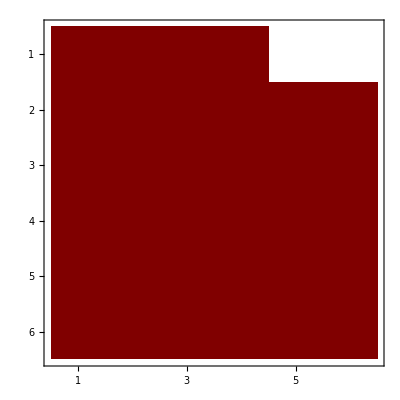

```mathematica
Mout//MatrixPlot
```

#### check flatness

```mathematica
kin
```

{X1,X2,Y}

```mathematica
Amatrix//Dimensions
```

{50,50}

```mathematica
Amatrix[[1,1]]
```

e (Log[X1+X2]-3 Log[Y])

```mathematica
Amatrix//Dimensions
```

{50,50}

```mathematica
AmatrixNeed//Dimensions
```

{16,16}

```mathematica
AmatrixNeed//MatrixForm
```

(e (Log[X2-Y]-4 Log[Y]+Log[X1+Y]) | 0 | e (Log[X1+Y]-Log[X2+Y]) | e (Log[X1-Y]-Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | e (-Log[X2-Y]+Log[X2+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0
0 | e (Log[X1-Y]-4 Log[Y]+Log[X2+Y]) | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2-Y]) | e (-Log[X2-Y]+Log[X1+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | e (Log[X2-Y]-Log[X2+Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0
0 | 0 | e (Log[X1+X2]-3 Log[Y]) | e (-Log[Y]+Log[X1+X2+2 Y]) | e (-Log[X1+X2]+Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (2 Log[X1+X2]-2 Log[X1+X2+2 Y]) | 0 | 0 | 0
0 | 0 | e (Log[X1+X2]-Log[Y]) | e (Log[X1+X2-2 Y]-3 Log[Y]) | e (-Log[X1+X2]+Log[X1+X2-2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (2 Log[X1+X2]-2 Log[X1+X2-2 Y]) | 0 | 0 | 0
0 | 0 | e (-Log[X1+X2]+Log[Y]) | e (-Log[X1+X2-2 Y]+Log[Y]) | e (Log[X1+X2]-Log[X1+X2-2 Y]-2 Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-2 Log[X1+X2]+2 Log[X1+X2-2 Y]) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-3 Log[Y]) | e (Log[X1+X2-2 Y]-Log[Y]) | e (-Log[X1+X2]+Log[X1+X2-2 Y]) | 0 | 0 | 0 | 0 | 0 | e (2 Log[X1+X2]-2 Log[X1+X2-2 Y]) | 0 | 0
0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[Y]) | e (-3 Log[Y]+Log[X1+X2+2 Y]) | e (-Log[X1+X2]+Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | e (2 Log[X1+X2]-2 Log[X1+X2+2 Y]) | 0 | 0
0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[Y]) | e (Log[Y]-Log[X1+X2+2 Y]) | e (Log[X1+X2]-2 Log[Y]-Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | e (-2 Log[X1+X2]+2 Log[X1+X2+2 Y]) | 0 | 0
e (Log[X2-Y]-Log[Y]) | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X2-Y]) | 0 | 0 | 0 | e (-Log[X2-Y]-2 Log[Y]+Log[X1+Y]) | 0 | 0 | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0
e (Log[Y]-Log[X1+Y]) | 0 | e (-Log[X1+Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-2 Log[Y]-Log[X1+Y]) | 0 | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0
0 | e (-Log[Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+Y]+Log[X2+Y]) | 0 | 0 | e (Log[X1-Y]-2 Log[Y]-Log[X2+Y]) | 0 | 0 | e (-Log[X1-Y]+Log[X1+Y]) | 0 | e (-Log[X1-Y]+Log[X1+Y])
0 | e (-Log[X1-Y]+Log[Y]) | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]-2 Log[Y]+Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | e (-Log[X2-Y]+Log[X2+Y])
0 | 0 | e (-Log[X1+X2]+Log[Y]) | 0 | e (Log[X1+X2]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 e Log[X1+X2] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[Y]) | 0 | e (Log[X1+X2]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | -2 e Log[X1+X2] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (-Log[X2-Y]+Log[Y]) | 0 | 0 | e (Log[X2-Y]-Log[X1+Y]) | 0 | e (-Log[X2-Y]-Log[X1+Y]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y]) | e (Log[Y]-Log[X2+Y]) | 0 | e (-Log[X1-Y]+Log[X2+Y]) | 0 | e (-Log[X1-Y]-Log[X2+Y]))

```mathematica
AmatrixNeed;
Table[D[%,kin[[i]]].D[%,kin[[j]]]-D[%,kin[[j]]].D[%,kin[[i]]]//Simplify,{i,1,Length[kin]},{j,i+1,Length[kin]}]//Flatten//DeleteCases[0]
```

{}

```mathematica
Table[A0[[i]].A0[[j]]-A0[[j]].A0[[i]]//Simplify,{i,1,Length[kin]},{j,i+1,Length[kin]}]//Flatten//DeleteCases[0]//Simplify
```

{}

```mathematica
Amatrix6//MatrixForm
```

(2 e (-2 Log[Y]+Log[X2+Y]) | e (Log[X1-Y]-Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (Log[X1+Y]-Log[X2+Y]) | 0 | 0
e (-Log[X1+X2-2 Y]+Log[X2+Y]) | e (Log[X1+X2-2 Y]-3 Log[Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (Log[X1+X2-2 Y]-Log[Y]+Log[X1+Y]-Log[X2+Y]) | e (Log[X1+X2]-Log[X1+X2-2 Y]+Log[X2-Y]-Log[X2+Y]) | e (-Log[X2-Y]+Log[X2+Y])
e (Log[X1+X2-2 Y]-Log[X1-Y]-2 Log[Y]+2 Log[X2+Y]) | e (-Log[X1+X2-2 Y]+Log[X1-Y]+Log[Y]-Log[X2+Y]) | e (Log[X1-Y]-2 Log[Y]-Log[X2+Y]) | e (-Log[X1+X2-2 Y]+Log[X1-Y]+Log[Y]-Log[X2+Y]) | e (-Log[X1+X2]+Log[X1+X2-2 Y]) | e (-Log[X1-Y]+Log[X1+Y])
e (Log[X2+Y]-Log[X1+X2+2 Y]) | e (Log[X1-Y]-Log[Y]-Log[X2+Y]+Log[X1+X2+2 Y]) | 0 | e (-3 Log[Y]+Log[X1+X2+2 Y]) | e (Log[X1+X2]-Log[X2-Y]+Log[X2+Y]-Log[X1+X2+2 Y]) | e (Log[X2-Y]-Log[X2+Y])
-e (Log[X1+X2-2 Y]-2 Log[Y]+Log[X1+X2+2 Y]) | e (Log[X1+X2-2 Y]-2 Log[Y]+Log[X1+X2+2 Y]) | 0 | e (Log[X1+X2-2 Y]-2 Log[Y]+Log[X1+X2+2 Y]) | -e (Log[X1+X2-2 Y]+Log[X1+X2+2 Y]) | 0
e (-Log[X1-Y]+Log[Y]+Log[X2+Y]-Log[X1+X2+2 Y]) | e (Log[X1-Y]-Log[Y]-Log[X2+Y]+Log[X1+X2+2 Y]) | e (Log[X1-Y]-Log[Y]) | e (Log[X1-Y]-2 Log[Y]+Log[X1+X2+2 Y]) | e (Log[X2+Y]-Log[X1+X2+2 Y]) | -e (Log[X1-Y]+Log[X2+Y]))

```mathematica
Amatrix6;
Table[D[%,kin[[i]]].D[%,kin[[j]]]-D[%,kin[[j]]].D[%,kin[[i]]]//Simplify,{i,1,Length[kin]},{j,i+1,Length[kin]}]//Flatten//DeleteCases[0]
```

{}

#### recover A matrix in kinematic flow

here we use Hayden’s basis

```mathematica
basisKinematic={⟨1,2,3⟩-⟨1,2,6⟩-⟨1,3,4⟩+⟨1,3,5⟩+⟨1,3,6⟩-⟨1,4,5⟩-⟨2,3,5⟩+⟨2,4,5⟩-⟨2,4,6⟩+⟨3,4,6⟩,-⟨2,3,5⟩+⟨2,3,7⟩+⟨2,4,5⟩-⟨2,4,6⟩-⟨2,6,7⟩+⟨3,4,6⟩-⟨3,4,7⟩+⟨3,5,7⟩+⟨3,6,7⟩-⟨4,5,7⟩,-⟨1,2,6⟩+⟨1,2,9⟩-⟨1,4,5⟩+⟨1,4,9⟩-⟨1,5,9⟩-⟨1,6,9⟩+⟨2,4,5⟩-⟨2,4,6⟩+⟨2,5,9⟩+⟨4,6,9⟩,⟨1,3,5⟩-⟨1,3,8⟩-⟨1,4,5⟩+⟨1,4,8⟩-⟨3,5,8⟩+⟨4,5,8⟩,-⟨1,3,4⟩+⟨1,3,8⟩-⟨1,4,8⟩+⟨3,4,8⟩,⟨1,3,6⟩-⟨1,3,8⟩+⟨1,6,8⟩+⟨3,4,6⟩-⟨3,4,8⟩-⟨4,6,8⟩,⟨2,4,5⟩-⟨2,4,6⟩+⟨2,5,9⟩-⟨2,6,7⟩-⟨2,7,9⟩-⟨4,5,7⟩+⟨4,6,9⟩-⟨4,7,9⟩+⟨5,7,9⟩+⟨6,7,9⟩,⟨3,5,7⟩-⟨3,5,8⟩+⟨3,7,8⟩-⟨4,5,7⟩+⟨4,5,8⟩-⟨4,7,8⟩,-⟨3,4,7⟩+⟨3,4,8⟩-⟨3,7,8⟩+⟨4,7,8⟩,⟨3,4,6⟩-⟨3,4,8⟩+⟨3,6,7⟩+⟨3,7,8⟩-⟨4,6,8⟩-⟨6,7,8⟩,-⟨1,4,5⟩+⟨1,4,8⟩-⟨1,5,9⟩+⟨1,8,9⟩+⟨4,5,8⟩-⟨5,8,9⟩,-⟨1,4,8⟩+⟨1,4,9⟩-⟨1,8,9⟩+⟨4,8,9⟩,⟨1,6,8⟩-⟨1,6,9⟩+⟨1,8,9⟩-⟨4,6,8⟩+⟨4,6,9⟩-⟨4,8,9⟩,-⟨4,5,7⟩+⟨4,5,8⟩-⟨4,7,8⟩+⟨5,7,9⟩-⟨5,8,9⟩+⟨7,8,9⟩,⟨4,7,8⟩-⟨4,7,9⟩+⟨4,8,9⟩-⟨7,8,9⟩,-⟨4,6,8⟩+⟨4,6,9⟩-⟨4,8,9⟩-⟨6,7,8⟩+⟨6,7,9⟩+⟨7,8,9⟩};
```

we should do a composition : 16x26 times 26x16 to obtain this 16x16 U matrix, as we need to use the 26d quotient space.

```mathematica
UmatrixK0=Table[Coefficient[basisKinematic[[i]]/.sol,basis[[j]]],{i,1,Length[basisKinematic]},{j,1,Length[basis]}];
UK0inv=Simplify[PseudoInverse[UmatrixK0]];
```

```mathematica
UmatrixK0//Dimensions
UK0inv//Dimensions
```

{16,50}

{50,16}

```mathematica
UmatrixK//Dimensions
```

{}

```mathematica
UmatrixK=UmatrixK0.Uinv;
UKinv=Simplify[Inverse[UmatrixK]];
```

Dot::dotsh: Tensors {{0,0,0,0,0,0,0,0,0,0,«40»},{0,0,0,0,0,0,0,0,0,0,«40»},{0,0,0,0,0,0,0,0,0,0,«40»},{0,0,0,0,0,0,0,0,0,0,«40»},{0,0,0,0,0,0,0,0,0,0,«40»},{0,0,0,0,0,0,0,0,0,0,«40»},{0,0,0,0,0,0,0,0,0,0,«40»},{0,0,0,0,0,0,0,0,0,0,«40»},{0,0,0,0,0,0,0,0,0,0,«40»},{0,0,0,0,0,0,0,0,0,0,«40»},«6»} and {{8/19,-1/38,3/38,2/19,0,0},{-11/19,-1/38,3/38,2/19,0,0},{-64/209,42/209,3/38,139/418,1/22,0},{-79/209,169/418,2/19,103/418,-1/22,0},{-48/209,63/418,7/38,26/209,-1/11,0},{31/209,-53/209,3/38,-51/418,-1/22,0},{35/209,-59/418,2/19,-125/418,1/22,0},{-29/209,25/418,7/38,7/209,1/11,0},{7/38,-2/19,-23/228,1/228,1/12,-1/6},{1/38,-3/19,-25/228,11/228,-1/12,1/6},«6»} have incompatible shapes.

```mathematica
AmatrixK=UmatrixK.Amatrix16.UKinv//Simplify;
%//MatrixForm
```

Dot::dotsh: Tensors {{0,0,0,0,0,0,0,0,0,0,«40»},{0,0,0,0,0,0,0,0,0,0,«40»},{0,0,0,0,0,0,0,0,0,0,«40»},{0,0,0,0,0,0,0,0,0,0,«40»},{0,0,0,0,0,0,0,0,0,0,«40»},{0,0,0,0,0,0,0,0,0,0,«40»},{0,0,0,0,0,0,0,0,0,0,«40»},{0,0,0,0,0,0,0,0,0,0,«40»},{0,0,0,0,0,0,0,0,0,0,«40»},{0,0,0,0,0,0,0,0,0,0,«40»},«6»} and {{8/19,-1/38,3/38,2/19,0,0},{-11/19,-1/38,3/38,2/19,0,0},{-64/209,42/209,3/38,139/418,1/22,0},{-79/209,169/418,2/19,103/418,-1/22,0},{-48/209,63/418,7/38,26/209,-1/11,0},{31/209,-53/209,3/38,-51/418,-1/22,0},{35/209,-59/418,2/19,-125/418,1/22,0},{-29/209,25/418,7/38,7/209,1/11,0},{7/38,-2/19,-23/228,1/228,1/12,-1/6},{1/38,-3/19,-25/228,11/228,-1/12,1/6},«6»} have incompatible shapes.

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}.{{8/19,-1/38,3/38,2/19,0,0},{-11/19,-1/38,3/38,2/19,0,0},{-64/209,42/209,3/38,139/418,1/22,0},{-79/209,169/418,2/19,103/418,-1/22,0},{-48/209,63/418,7/38,26/209,-1/11,0},{31/209,-53/209,3/38,-51/418,-1/22,0},{35/209,-59/418,2/19,-125/418,1/22,0},{-29/209,25/418,7/38,7/209,1/11,0},{7/38,-2/19,-23/228,1/228,1/12,-1/6},{1/38,-3/19,-25/228,11/228,-1/12,1/6},{7/38,-2/19,-61/228,-37/228,-1/12,1/6},{1/38,-3/19,13/228,49/228,1/12,-1/6},{1/11,-1/11,0,-1/11,2/11,0},{-1/11,1/11,0,1/11,-2/11,0},{0,0,-1/6,-1/6,-1/6,1/3},{0,0,1/6,1/6,1/6,-1/3}}.Amatrix16.Inverse[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}.{{8/19,-1/38,3/38,2/19,0,0},{-11/19,-1/38,3/38,2/19,0,0},{-64/209,42/209,3/38,139/418,1/22,0},{-79/209,169/418,2/19,103/418,-1/22,0},{-48/209,63/418,7/38,26/209,-1/11,0},{31/209,-53/209,3/38,-51/418,-1/22,0},{35/209,-59/418,2/19,-125/418,1/22,0},{-29/209,25/418,7/38,7/209,1/11,0},{7/38,-2/19,-23/228,1/228,1/12,-1/6},{1/38,-3/19,-25/228,11/228,-1/12,1/6},{7/38,-2/19,-61/228,-37/228,-1/12,1/6},{1/38,-3/19,13/228,49/228,1/12,-1/6},{1/11,-1/11,0,-1/11,2/11,0},{-1/11,1/11,0,1/11,-2/11,0},{0,0,-1/6,-1/6,-1/6,1/3},{0,0,1/6,1/6,1/6,-1/3}}]

```mathematica
AmatrixK//MatrixPlot
```

MatrixPlot::mat0: Argument «1» at position 1 is not a matrix.

MatrixPlot[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}.{{8/19,-1/38,3/38,2/19,0,0},{-11/19,-1/38,3/38,2/19,0,0},{-64/209,42/209,3/38,139/418,1/22,0},{-79/209,169/418,2/19,103/418,-1/22,0},{-48/209,63/418,7/38,26/209,-1/11,0},{31/209,-53/209,3/38,-51/418,-1/22,0},{35/209,-59/418,2/19,-125/418,1/22,0},{-29/209,25/418,7/38,7/209,1/11,0},{7/38,-2/19,-23/228,1/228,1/12,-1/6},{1/38,-3/19,-25/228,11/228,-1/12,1/6},{7/38,-2/19,-61/228,-37/228,-1/12,1/6},{1/38,-3/19,13/228,49/228,1/12,-1/6},{1/11,-1/11,0,-1/11,2/11,0},{-1/11,1/11,0,1/11,-2/11,0},{0,0,-1/6,-1/6,-1/6,1/3},{0,0,1/6,1/6,1/6,-1/3}}.Amatrix16.Inverse[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}.{{8/19,-1/38,3/38,2/19,0,0},{-11/19,-1/38,3/38,2/19,0,0},{-64/209,42/209,3/38,139/418,1/22,0},{-79/209,169/418,2/19,103/418,-1/22,0},{-48/209,63/418,7/38,26/209,-1/11,0},{31/209,-53/209,3/38,-51/418,-1/22,0},{35/209,-59/418,2/19,-125/418,1/22,0},{-29/209,25/418,7/38,7/209,1/11,0},{7/38,-2/19,-23/228,1/228,1/12,-1/6},{1/38,-3/19,-25/228,11/228,-1/12,1/6},{7/38,-2/19,-61/228,-37/228,-1/12,1/6},{1/38,-3/19,13/228,49/228,1/12,-1/6},{1/11,-1/11,0,-1/11,2/11,0},{-1/11,1/11,0,1/11,-2/11,0},{0,0,-1/6,-1/6,-1/6,1/3},{0,0,1/6,1/6,1/6,-1/3}}]]

matches the known result (difference due to a change of order in basisKinematic)

```mathematica
(*-Graphics-*)
```

### ODE for ψ

Translate A-matrix to ODE of the correlator:

```mathematica
ClearAll[A]
```

```mathematica
log[a_ b_]:=log[a]+log[b];
log[a__^b__]:=b log[a];
log[a_]:=Log[a];
dlkin[a_]:= Table[D[log[a],y[i]]dy[i],{i,KinDim}]//Total;

initiate[]:=(
ClearAll[dA,M,MI,MIFirstRowCoeff];
dA[0]:=A; 
dA[i_]:=dA[i]= D[dA[i-1],y[kN]]+dA[i-1].A(*//Simplify*);
dAI[i_]:=dAI[i]=dA[i].IVec//Simplify;
M[Ddeg_]:=M[Ddeg]=dA[Ddeg-1]+( Table[a[i]dA[i-1],{i,1,Ddeg-1}]//Total)+a[0]IdentityMatrix[Adim];
MI[Ddeg_]:=M[Ddeg].IVec;
MIFirstRowCoeff[Ddeg_]:= Coefficient[MI[Ddeg][[1]],#]&/@IVec;
(*MIGeneralCoeff[Ddeg_,ψ_]:=Coefficient[MI[Ddeg].Overlap[ψ],#]&/@IVec;*)
)
```

```mathematica
initiate[];
```

ODE for X_1:

```mathematica
kN=1; 
dim=3;
KinDim=Length[kin];
dlog[a_]:=D[Log[a],y[kN]] ;
```

```mathematica
A=AmatrixK/.Thread[{X1,X2,X3,Y12,Y23}->(y/@Range[KinDim])]/.Log[a_]:>dlog[a];
Adim=A//Length;
```

```mathematica
Ddeg=5;
EchoTiming[aSol=Solve[MIFirstRowCoeff[Ddeg]==0,Table[a[i],{i,0,Ddeg-1}]]//FullSimplify]
aSoldS=aSol/.e->0//FullSimplify
```

1.29945

{{a[0]→-((2 (-1+e)^2 e (2+e (-7+6 e)))/((y[1]+y[2]+y[3]) (y[1]-y[4]) (y[1]+y[4]) (y[1]+y[2]-y[5]) (y[1]+y[2]+y[5]))),a[1]→(2 (-1+e)^2 ((18+e (-37+20 e)) y[1]+(-2+e) ((-7+8 e) y[2]+(-3+2 e) y[3])))/((y[1]+y[2]+y[3]) (y[1]-y[4]) (y[1]+y[4]) (y[1]+y[2]-y[5]) (y[1]+y[2]+y[5])),a[2]→((108+e (-248+(193-51 e) e)) y[1]^2-(-3+e) (-2+e) (-8+7 e) y[2]^2-2 (-3+e) (-2+e) (-3+2 e) y[2] y[3]-2 (-2+e) y[1] ((38+e (-59+23 e)) y[2]+(-3+2 e) (-5+3 e) y[3])+(-2+3 e) (2 (-1+e) (-1+2 e) y[4]^2+(-3+e) (-2+e) y[5]^2))/((y[1]+y[2]+y[3]) (y[1]-y[4]) (y[1]+y[4]) (y[1]+y[2]-y[5]) (y[1]+y[2]+y[5])),a[3]→((74+e (-95+31 e)) y[1]^3+(-4+e) (-3+e) y[2]^3+(-4+e) (-3+e) y[2]^2 y[3]+(-2+e) y[1]^2 ((-73+47 e) y[2]+(-27+13 e) y[3])+y[3] (-2 (-1+e) (-3+2 e) y[4]^2-(-4+e) (-3+e) y[5]^2)+y[2] (-2 (-1+e) (-7+8 e) y[4]^2-(-4+e) (-3+e) y[5]^2)+y[1] ((-3+e) (-28+17 e) y[2]^2+10 (-3+e) (-2+e) y[2] y[3]-2 (-1+e) (-7+8 e) y[4]^2-(-3+e) (-8+7 e) y[5]^2))/((y[1]+y[2]+y[3]) (y[1]-y[4]) (y[1]+y[4]) (y[1]+y[2]-y[5]) (y[1]+y[2]+y[5])),a[4]→(2-3 e)/(y[1]+y[2]+y[3])+(-4+e)/(-y[1]+y[4])+(4-e)/(y[1]+y[4])+(3-2 e)/(y[1]+y[2]-y[5])+(3-2 e)/(y[1]+y[2]+y[5])}}

{{a[0]→0,a[1]→(4 (9 y[1]+7 y[2]+3 y[3]))/((y[1]+y[2]+y[3]) (y[1]^2-y[4]^2) ((y[1]+y[2])^2-y[5]^2)),a[2]→(4 (27 y[1]^2+12 y[2]^2+9 y[2] y[3]+y[1] (38 y[2]+15 y[3])-y[4]^2-3 y[5]^2))/((y[1]+y[2]+y[3]) (y[1]^2-y[4]^2) ((y[1]+y[2])^2-y[5]^2)),a[3]→(2 (37 y[1]^3+6 y[2]^3+6 y[2]^2 y[3]+y[1]^2 (73 y[2]+27 y[3])-7 y[2] y[4]^2-3 y[3] y[4]^2-6 (y[2]+y[3]) y[5]^2+y[1] (6 y[2] (7 y[2]+5 y[3])-7 y[4]^2-12 y[5]^2)))/((y[1]+y[2]+y[3]) (y[1]-y[4]) (y[1]+y[4]) (y[1]+y[2]-y[5]) (y[1]+y[2]+y[5])),a[4]→2/(y[1]+y[2]+y[3])+4/(y[1]-y[4])+4/(y[1]+y[4])+3/(y[1]+y[2]-y[5])+3/(y[1]+y[2]+y[5])}}